## Extracting info from 1904.07265

## One data set only

### Data

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.,21.1111,22.2222,23.3333,24.4444,25.5556,26.6667,27.7778,28.8889,30.,31.1111,32.2222,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,40.,41.1111,42.2222,43.3333,44.4444}

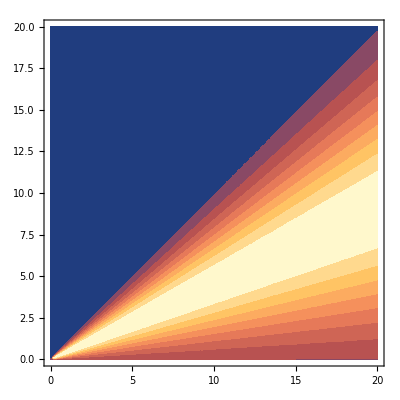

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

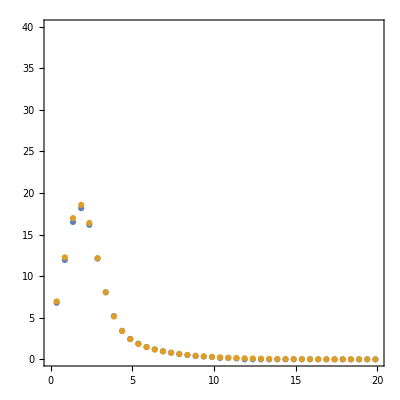

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
```

```mathematica
ratio[epS_,ee_]=(-1.3417950781553514+ee (63.6110167803427+(-11.335620650792169+0.48602694541668334 ee) ee)-26.253111607723554 epS+ee (653.3344894860501+ee (-102.78730074393953+4.450961331828265 ee)) epS+(525.5392109465565+ee (50842.27469116989+ee (-8729.640428648672+374.686356791237 ee))) epS^2+(1.3417950781553512+ee (-63.61101678034271+(11.335620650792173-0.48602694541668334 ee) ee)-47.198323815726795 epS+ee (-627.2311837169866+(102.78730074393945-4.450961331828264 ee) ee) epS+(377.44952730016934+ee (47657.51492975174+ee (-8263.66745442748+354.3136432087616 ee))) epS^2) Cos[8.323065282815573/ee]+(-10.918891490242757+ee (3.916905079979295+(-0.17249070990867868-2.1684043449710455*^-19 ee) ee)-59.87086539190307 epS+ee (-21.189965718249404+(-0.7854585909514353-0.06547117846490069 ee) ee) epS+(7086.844664530483+ee (-1565.9397835413793+125.74572752342468 ee)) epS^2) Sin[8.323065282815573/ee])/(-1.3417950781553516+ee (63.61101678034271+(-11.33562065079217+0.48602694541668334 ee) ee)+(1.3417950781553507+ee (-63.611016780342716+(11.335620650792173-0.4860269454166834 ee) ee)) Cos[8.323065282815573/ee]+(-10.918891490242876+ee (3.916905079979277+(-0.17249070990867785-2.1684043449710344*^-19 ee) ee)) Sin[8.323065282815573/ee]);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

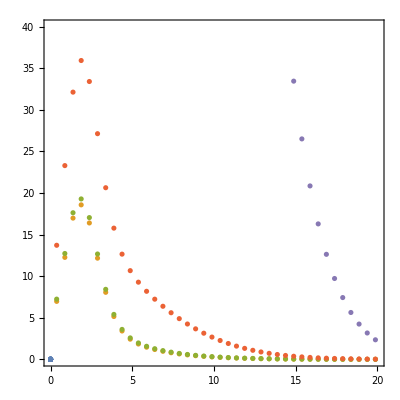

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data*0,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.97108,7.24059},{12.2612,12.7273},{16.9807,17.6248},{18.5749,19.2868},{16.398,17.0425},{12.1658,12.6663},{8.06067,8.41777},{5.15012,5.40323},{3.41041,3.59934},{2.42756,2.57819},{1.84576,1.97171},{1.46299,1.57092},{1.18441,1.27779},{0.968088,1.04902},{0.794312,0.864338},{0.65239,0.71278},{0.535537,0.587395},{0.438937,0.483254},{0.358948,0.396624},{0.292705,0.324558},{0.237899,0.264676},{0.192641,0.215017},{0.155364,0.173949},{0.124757,0.140098},{0.0997192,0.112303},{0.0793215,0.0895775},{0.0627787,0.0710833},{0.0494268,0.0561073},{0.0387054,0.0440439},{0.0301422,0.0343799},{0.0233408,0.0266819},{0.0179696,0.0205861},{0.0137529,0.0157878},{0.0104624,0.0120341},{0.00791051,0.00911601},{0.00594381,0.00686191},{0.00443777,0.005132},{0.00329194,0.00381313},{0.00242592,0.00281434},{0.00177576,0.0020631}}

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi,.5*i]//Chop,ratio[nsi,.5*i]/NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi2,.5*i]//Chop,ratio[nsi2,.5*i]/NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi3,.5*i]//Chop,ratio[nsi3,.5*i]/NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.96499,1.032,1.06944},{1.11857,1.03541,0.925658},{1.16206,1.0709,0.921556},{1.04411,1.03588,0.992111},{1.03437,1.03356,0.999219},{1.03343,1.03349,1.00005},{1.03379,1.03419,1.00038},{1.03473,1.03534,1.00059},{1.03606,1.03683,1.00074},{1.03769,1.0386,1.00088},{1.0396,1.04064,1.001},{1.04176,1.04292,1.00111},{1.04416,1.04543,1.00122},{1.04679,1.04818,1.00133},{1.04965,1.05116,1.00144},{1.05274,1.05436,1.00154},{1.05605,1.05778,1.00164},{1.05958,1.06142,1.00174},{1.06333,1.06528,1.00183},{1.0673,1.06936,1.00193},{1.07149,1.07365,1.00202},{1.07589,1.07816,1.00211},{1.08051,1.08289,1.0022},{1.08534,1.08783,1.00229},{1.09039,1.09299,1.00238},{1.09566,1.09836,1.00247},{1.10114,1.10395,1.00255},{1.10683,1.10975,1.00264},{1.11274,1.11577,1.00272},{1.11887,1.122,1.0028},{1.1252,1.12844,1.00288},{1.13176,1.1351,1.00296},{1.13852,1.14198,1.00303},{1.1455,1.14906,1.00311},{1.1527,1.15636,1.00318},{1.1601,1.16388,1.00325},{1.16772,1.1716,1.00332},{1.17556,1.17955,1.00339},{1.18361,1.1877,1.00346},{1.19187,1.19607,1.00353}}

{{-0.0429542,1.40816,-32.7828},{13.4957,1.70903,0.126636},{16.0094,5.26588,0.328924},{2.40293,1.55673,0.647846},{1.42396,1.36176,0.956324},{1.36602,1.38727,1.01556},{1.43127,1.48343,1.03644},{1.54882,1.61982,1.04584},{1.70087,1.78655,1.05037},{1.88096,1.97954,1.05241},{2.0862,2.1968,1.05301},{2.31513,2.43727,1.05276},{2.56693,2.70032,1.05197},{2.84111,2.98558,1.05085},{3.13737,3.2928,1.04954},{3.4555,3.62181,1.04813},{3.79535,3.9725,1.04667},{4.15684,4.34478,1.04521},{4.53989,4.73858,1.04377},{4.94444,5.15388,1.04236},{5.37047,5.59062,1.04099},{5.81793,6.0488,1.03968},{6.2868,6.52837,1.03843},{6.77707,7.02933,1.03722},{7.28872,7.55167,1.03608},{7.82174,8.09537,1.03498},{8.37612,8.66043,1.03394},{8.95186,9.24684,1.03295},{9.54894,9.85459,1.03201},{10.1674,10.4837,1.03111},{10.8071,11.1341,1.03026},{11.4682,11.8058,1.02944},{12.1506,12.4989,1.02867},{12.8543,13.2133,1.02793},{13.5794,13.949,1.02722},{14.3258,14.7061,1.02655},{15.0935,15.4844,1.0259},{15.8825,16.2841,1.02529},{16.6928,17.1051,1.0247},{17.5245,17.9474,1.02413}}

{{-45.3577,13.8956,-0.306355},{1256.95,43.58,0.0346711},{1489.97,399.342,0.26802},{111.209,26.3645,0.237071},{13.2696,7.23657,0.545348},{7.82947,10.1108,1.29137},{14.6461,19.9878,1.36472},{26.6371,33.8402,1.27042},{42.0383,50.6939,1.2059},{60.2143,70.1485,1.16498},{80.8847,92.0121,1.13757},{103.908,116.182,1.11813},{129.206,142.601,1.10367},{156.732,171.231,1.0925},{186.458,202.049,1.08362},{218.365,235.041,1.07637},{252.439,270.196,1.07034},{288.671,307.505,1.06524},{327.056,346.964,1.06087},{367.588,388.569,1.05708},{410.265,432.317,1.05375},{455.082,478.205,1.05081},{502.04,526.231,1.04819},{551.135,576.394,1.04583},{602.366,628.694,1.04371},{655.733,683.128,1.04178},{711.235,739.697,1.04002},{768.871,798.4,1.03841},{828.64,859.236,1.03692},{890.542,922.204,1.03555},{954.577,987.306,1.03429},{1020.74,1054.54,1.03311},{1089.04,1123.9,1.03201},{1159.48,1195.4,1.03098},{1232.04,1269.03,1.03003},{1306.73,1344.79,1.02912},{1383.56,1422.68,1.02828},{1462.52,1502.71,1.02748},{1543.61,1584.86,1.02673},{1626.83,1669.15,1.02601}}

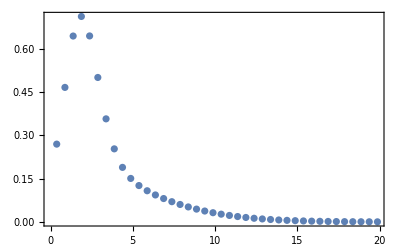

```mathematica
ListPlot[Transpose@{dataT[[All,1]],-dataT[[All,2]]+dataNSI[[All,2]]},Frame->True]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

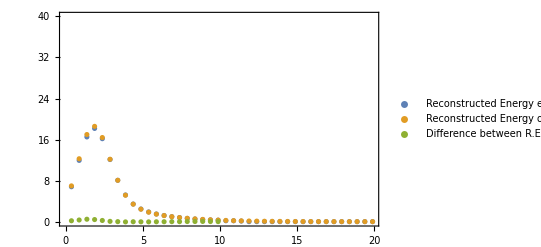

```mathematica
ListPlot[{data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},PlotRange->{All,range}]
```

The NSI modulus is 0.003

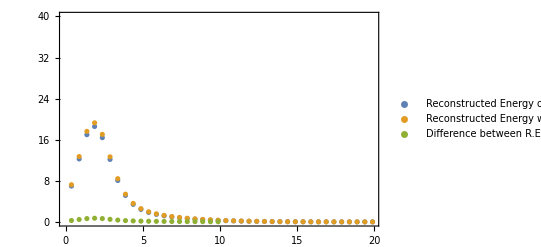

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.03

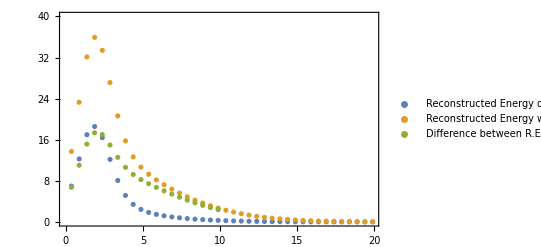

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI2[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.3

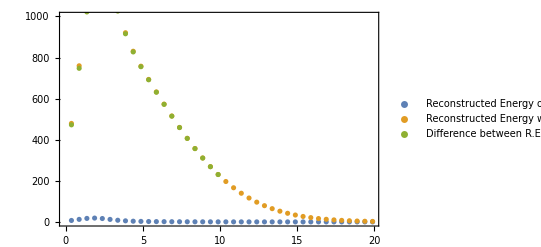

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI3,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI3[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,{0,1000}}]
```

### General Probabilitly ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passo=.4/10;
dataGen={};dataGenNSI={};dataGenNSI2={};dataGenNSIp={};dataGenNSI2p={};ls23={};
Do[ss23=(0.582)-.2+passo*i;delta=-2.5;AppendTo[ls23,ss23];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi2,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSIp,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2p,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi2,.5*i],{i,40}]},{j,40}]],{i,0,10}];
```

0.003

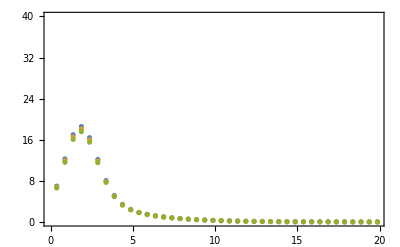
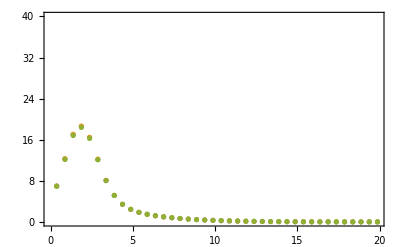
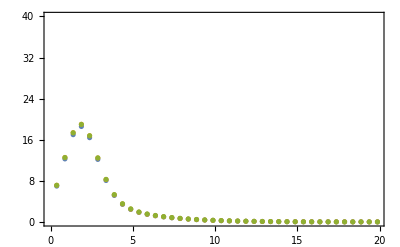
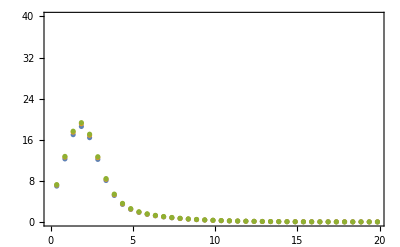
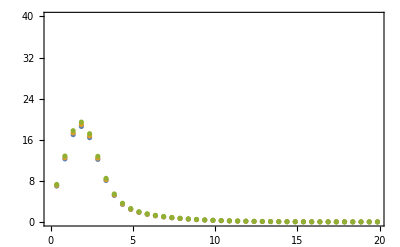
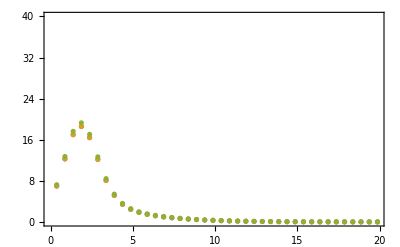
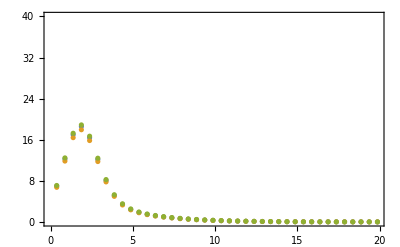
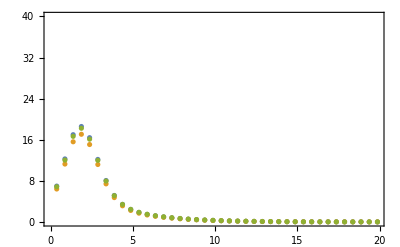

0.03

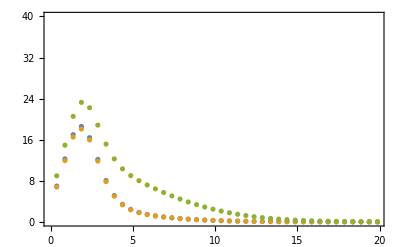
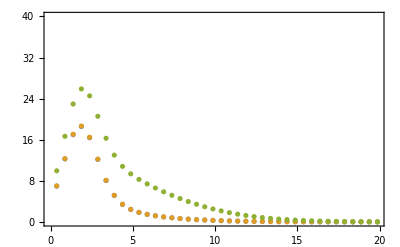
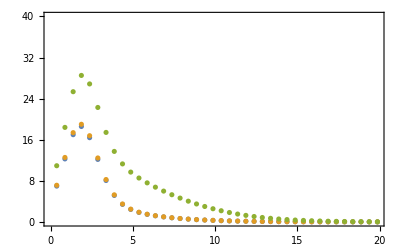
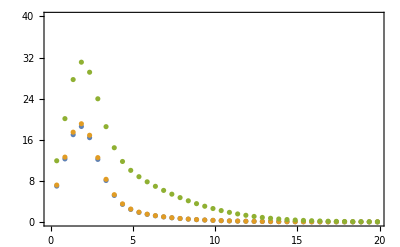
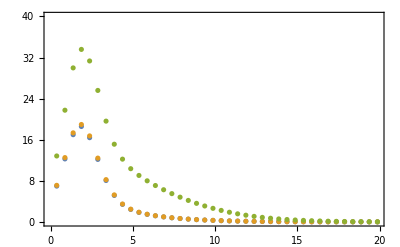
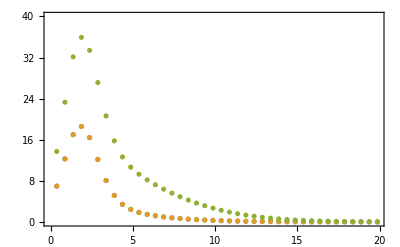
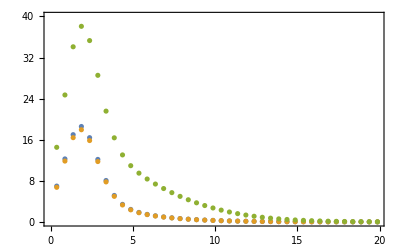
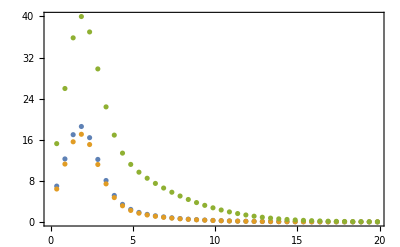

-0.003

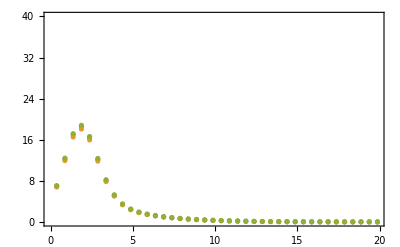
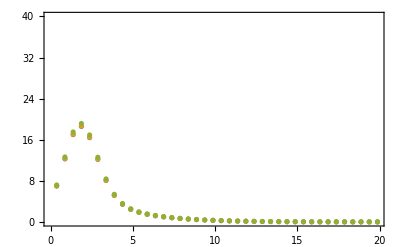
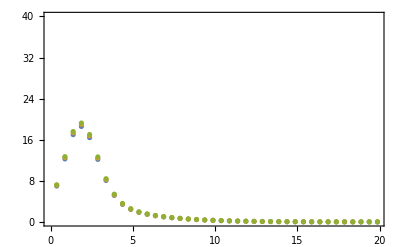
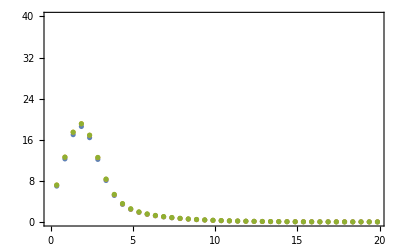
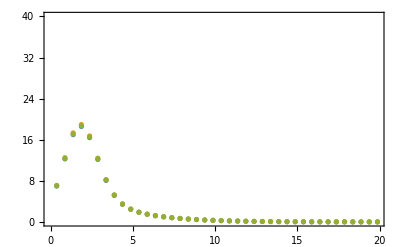
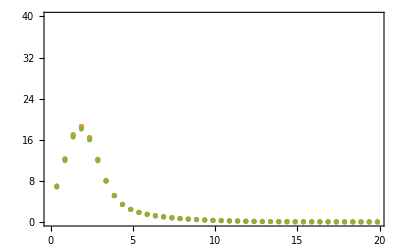
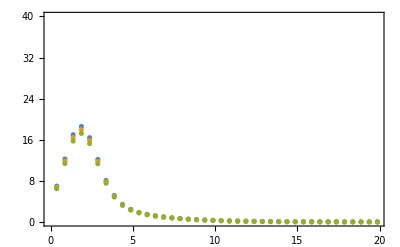
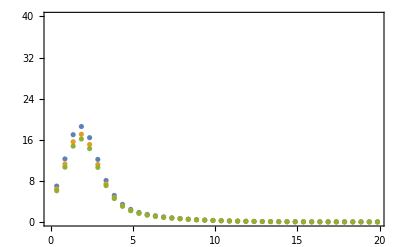

```mathematica
Print[nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[nsi2]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI2[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[-nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSIp[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
```

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.877206,0.962429,1.09715},{1.02851,1.03866,1.00988},{1.20426,0.84678,0.703154},{0.916722,0.953288,1.03989},{0.970634,0.984752,1.01455},{0.995329,1.00489,1.00961},{1.01309,1.02082,1.00763},{1.02787,1.03465,1.0066},{1.04103,1.04724,1.00597},{1.0532,1.05905,1.00555},{1.06471,1.0703,1.00525},{1.07576,1.08117,1.00502},{1.08647,1.09174,1.00485},{1.09693,1.10208,1.0047},{1.10718,1.11226,1.00458},{1.11728,1.12229,1.00448},{1.12725,1.1322,1.00439},{1.13712,1.14202,1.00431},{1.1469,1.15176,1.00424},{1.1566,1.16144,1.00418},{1.16625,1.17105,1.00412},{1.17584,1.18062,1.00407},{1.18539,1.19015,1.00402},{1.19489,1.19963,1.00397},{1.20436,1.20909,1.00392},{1.21381,1.21852,1.00388},{1.22322,1.22792,1.00384},{1.23261,1.2373,1.0038},{1.24198,1.24666,1.00377},{1.25133,1.256,1.00373},{1.26066,1.26532,1.0037},{1.26998,1.27463,1.00366},{1.27928,1.28393,1.00363},{1.28857,1.29321,1.0036},{1.29785,1.30248,1.00357},{1.30711,1.31174,1.00354},{1.31637,1.321,1.00351},{1.32562,1.33024,1.00349},{1.33486,1.33948,1.00346},{1.34409,1.34871,1.00343}}

{{0.655419,0.748632,1.14222},{0.810253,0.818672,1.01039},{0.967969,0.646053,0.667431},{0.708962,0.741793,1.04631},{0.757298,0.769893,1.01663},{0.779296,0.787785,1.01089},{0.795048,0.801892,1.00861},{0.808115,0.814106,1.00741},{0.819732,0.825215,1.00669},{0.830462,0.835613,1.0062},{0.840604,0.845526,1.00586},{0.850332,0.855088,1.00559},{0.859758,0.86439,1.00539},{0.868956,0.873492,1.00522},{0.877976,0.882437,1.00508},{0.886856,0.891257,1.00496},{0.895623,0.899974,1.00486},{0.904297,0.908607,1.00477},{0.912894,0.91717,1.00468},{0.921426,0.925674,1.00461},{0.929904,0.934126,1.00454},{0.938334,0.942536,1.00448},{0.946725,0.950907,1.00442},{0.95508,0.959246,1.00436},{0.963404,0.967557,1.00431},{0.971701,0.975841,1.00426},{0.979974,0.984104,1.00421},{0.988226,0.992346,1.00417},{0.99646,1.00057,1.00413},{1.00468,1.00878,1.00408},{1.01288,1.01697,1.00404},{1.02106,1.02515,1.004},{1.02924,1.03332,1.00397},{1.0374,1.04148,1.00393},{1.04555,1.04963,1.0039},{1.0537,1.05777,1.00386},{1.06183,1.0659,1.00383},{1.06996,1.07402,1.0038},{1.07808,1.08213,1.00376},{1.08619,1.09024,1.00373}}

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0417651,0.00127844,0.0302018,0.045592,0.0243565,0,0.0669707,0.393879,1.24978,3.05311,6.46513}

InterpolatingFunction[…]

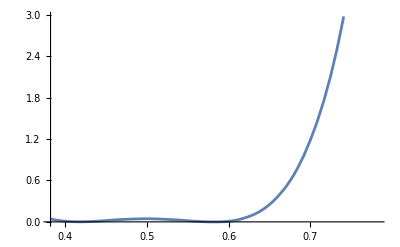

```mathematica
Table[{ls23[[i]],{chis23[[i]]}},{i,Length@ls23}];
Interpolation@%
Plot[%[x],{x,ls23[[1]],ls23[[-1]]}]
```

```mathematica
chiNSI=Table[Sum[dataGenNSI[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0380715,0.016042,0.013119,0.0295052,0.0653829,0.120937,0.196377,0.291966,0.408066,0.545208,0.704232}

{50.2196,54.2052,59.5398,66.2571,74.3762,83.9034,94.8329,107.147,120.815,135.788,151.994}

{0.134069,0.0747352,0.0353852,0.0157527,0.015595,0.0346672,0.0726948,0.129339,0.204146,0.296455,0.405233}

{86.171,76.2318,67.7091,60.5938,54.8634,50.4804,47.3902,45.5207,44.7887,45.1249,46.5518}

```mathematica
chis23NSI=Table[Sum[dataGenNSI[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.145607,0.0130478,0.0557808,0.131812,0.161555,0.120936,0.0418771,0.0205965,0.236567,0.98918,2.76826}

{48.6736,54.5243,61.267,68.6088,76.2534,83.9034,91.2583,98.01,103.835,108.383,111.258}

{0.0344902,0.0938085,0.117281,0.0831128,0.0254034,0.0346676,0.265912,0.956332,2.45797,5.29697,10.2857}

{83.5249,76.6689,69.6468,62.7507,56.268,50.4804,45.6579,42.0428,39.8182,39.049,39.5855}

```mathematica
Join[Table[{ls23[[i]],nsi,{chis23NSI[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi2,{chis23NSI2[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi,{chis23NSIp[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi2,{chis23NSI2p[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi*0,{chis23[[i]]}},{i,Length@ls23}]];
func=Interpolation@%
```

InterpolatingFunction[…]

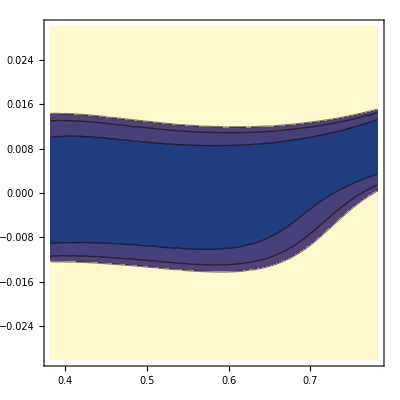

```mathematica
ContourPlot[func[s23,nsii],{s23,ls23[[1]],ls23[[-1]]},{nsii,-.03,.03},Contours->{2.3,4.6,6.}]
```

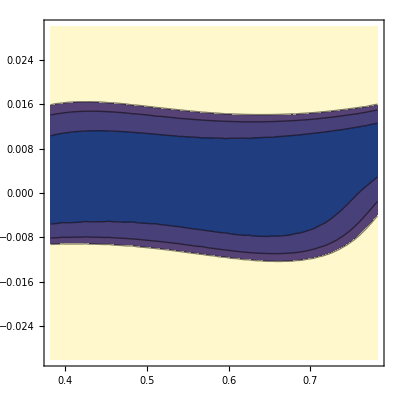

```mathematica
-
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=-2.5-1.+passodelta*k;AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

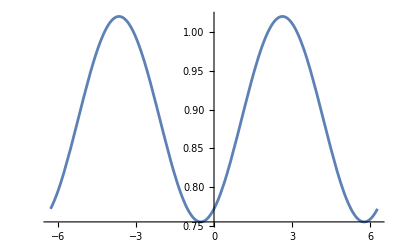

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

35

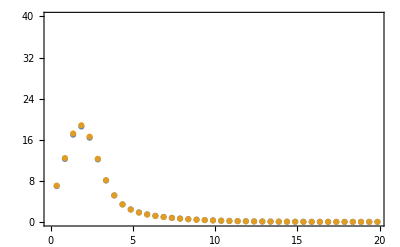

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.388688,0.128467,0.0204679,0.015481,0.0653107,0.12983,0.182048,0.211072,0.222916,0.239223,0.294002,0.168682,0.0213053,0.00806994,0.0776656,0.180342,0.274922,0.333861,0.346207,0.318417,0.273087,0.245708,0.0895912,0.0073862,0.0489266,0.161663,0.294925,0.406915,0.469759,0.472466,0.421752,0.340776,0.265897,0.0724878,0.0102742,0.0686238,0.194604,0.337258,0.454595,0.51864,0.518389,0.460639,0.368721,0.279264,0.0938652,0.00720276,0.0449956,0.15478,0.285949,0.396747,0.459323,0.462689,0.413544,0.335007,0.263379,0.182515,0.0260575,0.00519212,0.0687802,0.167198,0.259355,0.317752,0.33144,0.306842,0.266477,0.245714,0.423364,0.14908,0.0292794,0.0150083,0.0582625,0.119043,0.170427,0.201529,0.218307,0.242287,0.307296,0.969389,0.524375,0.26142,0.134623,0.0982298,0.113756,0.155076,0.211378,0.287968,0.404969,0.594039,2.06537,1.38882,0.932133,0.653306,0.509458,0.464024,0.491881,0.582297,0.73972,0.982451,1.33933,4.09204,3.11066,2.39964,1.92169,1.63738,1.51243,1.52289,1.65811,1.92145,2.32895,2.90596,7.65016,6.27044,5.22837,4.49209,4.02603,3.7985,3.78683,3.98038,4.38121,5.00265,5.8659}

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}]
```

{{{0.382,-3.5},{0.388688}},{{0.382,-3.3},{0.128467}},{{0.382,-3.1},{0.0204679}},{{0.382,-2.9},{0.015481}},{{0.382,-2.7},{0.0653107}},{{0.382,-2.5},{0.12983}},{{0.382,-2.3},{0.182048}},{{0.382,-2.1},{0.211072}},{{0.382,-1.9},{0.222916}},{{0.382,-1.7},{0.239223}},{{0.382,-1.5},{0.294002}},{{0.422,-3.5},{0.168682}},{{0.422,-3.3},{0.0213053}},{{0.422,-3.1},{0.00806994}},{{0.422,-2.9},{0.0776656}},{{0.422,-2.7},{0.180342}},{{0.422,-2.5},{0.274922}},{{0.422,-2.3},{0.333861}},{{0.422,-2.1},{0.346207}},{{0.422,-1.9},{0.318417}},{{0.422,-1.7},{0.273087}},{{0.422,-1.5},{0.245708}},{{0.462,-3.5},{0.0895912}},{{0.462,-3.3},{0.0073862}},{{0.462,-3.1},{0.0489266}},{{0.462,-2.9},{0.161663}},{{0.462,-2.7},{0.294925}},{{0.462,-2.5},{0.406915}},{{0.462,-2.3},{0.469759}},{{0.462,-2.1},{0.472466}},{{0.462,-1.9},{0.421752}},{{0.462,-1.7},{0.340776}},{{0.462,-1.5},{0.265897}},{{0.502,-3.5},{0.0724878}},{{0.502,-3.3},{0.0102742}},{{0.502,-3.1},{0.0686238}},{{0.502,-2.9},{0.194604}},{{0.502,-2.7},{0.337258}},{{0.502,-2.5},{0.454595}},{{0.502,-2.3},{0.51864}},{{0.502,-2.1},{0.518389}},{{0.502,-1.9},{0.460639}},{{0.502,-1.7},{0.368721}},{{0.502,-1.5},{0.279264}},{{0.542,-3.5},{0.0938652}},{{0.542,-3.3},{0.00720276}},{{0.542,-3.1},{0.0449956}},{{0.542,-2.9},{0.15478}},{{0.542,-2.7},{0.285949}},{{0.542,-2.5},{0.396747}},{{0.542,-2.3},{0.459323}},{{0.542,-2.1},{0.462689}},{{0.542,-1.9},{0.413544}},{{0.542,-1.7},{0.335007}},{{0.542,-1.5},{0.263379}},{{0.582,-3.5},{0.182515}},{{0.582,-3.3},{0.0260575}},{{0.582,-3.1},{0.00519212}},{{0.582,-2.9},{0.0687802}},{{0.582,-2.7},{0.167198}},{{0.582,-2.5},{0.259355}},{{0.582,-2.3},{0.317752}},{{0.582,-2.1},{0.33144}},{{0.582,-1.9},{0.306842}},{{0.582,-1.7},{0.266477}},{{0.582,-1.5},{0.245714}},{{0.622,-3.5},{0.423364}},{{0.622,-3.3},{0.14908}},{{0.622,-3.1},{0.0292794}},{{0.622,-2.9},{0.0150083}},{{0.622,-2.7},{0.0582625}},{{0.622,-2.5},{0.119043}},{{0.622,-2.3},{0.170427}},{{0.622,-2.1},{0.201529}},{{0.622,-1.9},{0.218307}},{{0.622,-1.7},{0.242287}},{{0.622,-1.5},{0.307296}},{{0.662,-3.5},{0.969389}},{{0.662,-3.3},{0.524375}},{{0.662,-3.1},{0.26142}},{{0.662,-2.9},{0.134623}},{{0.662,-2.7},{0.0982298}},{{0.662,-2.5},{0.113756}},{{0.662,-2.3},{0.155076}},{{0.662,-2.1},{0.211378}},{{0.662,-1.9},{0.287968}},{{0.662,-1.7},{0.404969}},{{0.662,-1.5},{0.594039}},{{0.702,-3.5},{2.06537}},{{0.702,-3.3},{1.38882}},{{0.702,-3.1},{0.932133}},{{0.702,-2.9},{0.653306}},{{0.702,-2.7},{0.509458}},{{0.702,-2.5},{0.464024}},{{0.702,-2.3},{0.491881}},{{0.702,-2.1},{0.582297}},{{0.702,-1.9},{0.73972}},{{0.702,-1.7},{0.982451}},{{0.702,-1.5},{1.33933}},{{0.742,-3.5},{4.09204}},{{0.742,-3.3},{3.11066}},{{0.742,-3.1},{2.39964}},{{0.742,-2.9},{1.92169}},{{0.742,-2.7},{1.63738}},{{0.742,-2.5},{1.51243}},{{0.742,-2.3},{1.52289}},{{0.742,-2.1},{1.65811}},{{0.742,-1.9},{1.92145}},{{0.742,-1.7},{2.32895}},{{0.742,-1.5},{2.90596}},{{0.782,-3.5},{7.65016}},{{0.782,-3.3},{6.27044}},{{0.782,-3.1},{5.22837}},{{0.782,-2.9},{4.49209}},{{0.782,-2.7},{4.02603}},{{0.782,-2.5},{3.7985}},{{0.782,-2.3},{3.78683}},{{0.782,-2.1},{3.98038}},{{0.782,-1.9},{4.38121}},{{0.782,-1.7},{5.00265}},{{0.782,-1.5},{5.8659}}}

InterpolatingFunction[…]

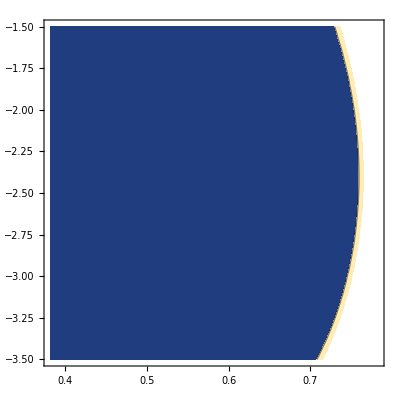

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

### Check probability

```mathematica
ratioGen[S23,dcp,0,ee]
Table[ratioGen[0.582,-2.15,0,ee],{ee,1,10}]
```

(0.-0.555354 ee √(1-S23) √S23 Cos[dcp]+ee (0.-8.22111 S23+8.22111 S23^2+0.555354 √(1-S23) √S23 Cos[dcp]) Cos[8.32307/ee]+S23 (0.+8.22111 ee-1.44661 Sin[8.32307/ee])-0.555354 ee √(1-S23) √S23 Sin[dcp] Sin[8.32307/ee]+S23^2 (0.-8.22111 ee+1.44661 Sin[8.32307/ee]))/(2.26532 ee-2.26532 ee Cos[8.32307/ee]+1.11022×10^-16 ee Cos[16.6461/ee]-0.351926 Sin[8.32307/ee])

{1.01241,0.89694,0.967545,1.00861,1.04238,1.07306,1.10209,1.13014,1.15755,1.18452}

## All data sets - s23 and dcp

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

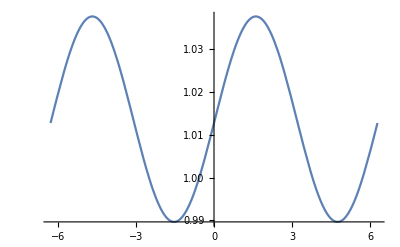

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

22

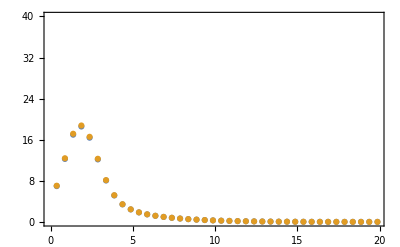

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

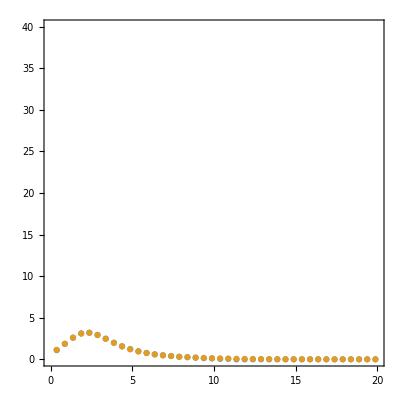

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

92

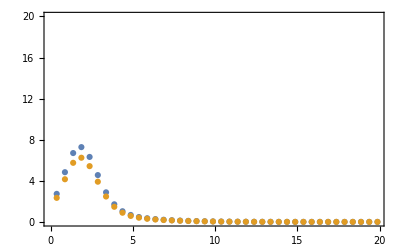

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

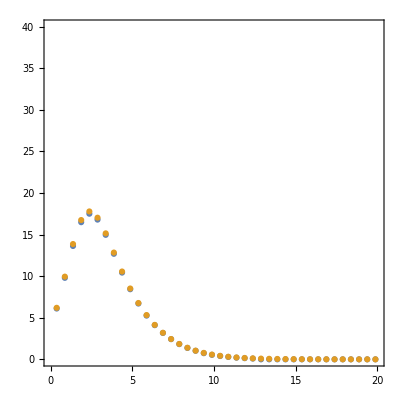

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

85

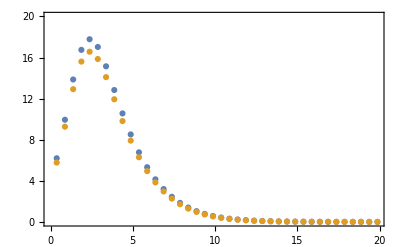

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-3.14159},{0.382,-2.51327},{0.382,-1.88496},{0.382,-1.25664},{0.382,-0.628319},{0.382,0.},{0.382,0.628319},{0.382,1.25664},{0.382,1.88496},{0.382,2.51327},{0.382,3.14159},{0.422,-3.14159},{0.422,-2.51327},{0.422,-1.88496},{0.422,-1.25664},{0.422,-0.628319},{0.422,0.},{0.422,0.628319},{0.422,1.25664},{0.422,1.88496},{0.422,2.51327},{0.422,3.14159},{0.462,-3.14159},{0.462,-2.51327},{0.462,-1.88496},{0.462,-1.25664},{0.462,-0.628319},{0.462,0.},{0.462,0.628319},{0.462,1.25664},{0.462,1.88496},{0.462,2.51327},{0.462,3.14159},{0.502,-3.14159},{0.502,-2.51327},{0.502,-1.88496},{0.502,-1.25664},{0.502,-0.628319},{0.502,0.},{0.502,0.628319},{0.502,1.25664},{0.502,1.88496},{0.502,2.51327},{0.502,3.14159},{0.542,-3.14159},{0.542,-2.51327},{0.542,-1.88496},{0.542,-1.25664},{0.542,-0.628319},{0.542,0.},{0.542,0.628319},{0.542,1.25664},{0.542,1.88496},{0.542,2.51327},{0.542,3.14159},{0.582,-3.14159},{0.582,-2.51327},{0.582,-1.88496},{0.582,-1.25664},{0.582,-0.628319},{0.582,0.},{0.582,0.628319},{0.582,1.25664},{0.582,1.88496},{0.582,2.51327},{0.582,3.14159},{0.622,-3.14159},{0.622,-2.51327},{0.622,-1.88496},{0.622,-1.25664},{0.622,-0.628319},{0.622,0.},{0.622,0.628319},{0.622,1.25664},{0.622,1.88496},{0.622,2.51327},{0.622,3.14159},{0.662,-3.14159},{0.662,-2.51327},{0.662,-1.88496},{0.662,-1.25664},{0.662,-0.628319},{0.662,0.},{0.662,0.628319},{0.662,1.25664},{0.662,1.88496},{0.662,2.51327},{0.662,3.14159},{0.702,-3.14159},{0.702,-2.51327},{0.702,-1.88496},{0.702,-1.25664},{0.702,-0.628319},{0.702,0.},{0.702,0.628319},{0.702,1.25664},{0.702,1.88496},{0.702,2.51327},{0.702,3.14159},{0.742,-3.14159},{0.742,-2.51327},{0.742,-1.88496},{0.742,-1.25664},{0.742,-0.628319},{0.742,0.},{0.742,0.628319},{0.742,1.25664},{0.742,1.88496},{0.742,2.51327},{0.742,3.14159},{0.782,-3.14159},{0.782,-2.51327},{0.782,-1.88496},{0.782,-1.25664},{0.782,-0.628319},{0.782,0.},{0.782,0.628319},{0.782,1.25664},{0.782,1.88496},{0.782,2.51327},{0.782,3.14159}}

```mathematica
dataSet1
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

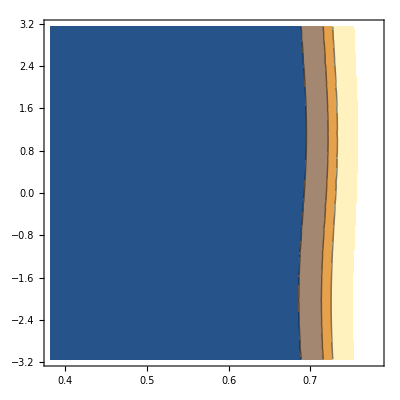

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

11

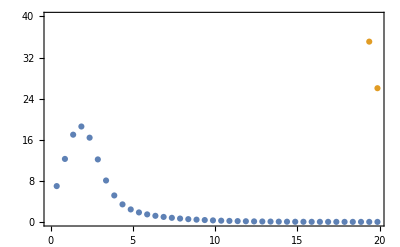

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

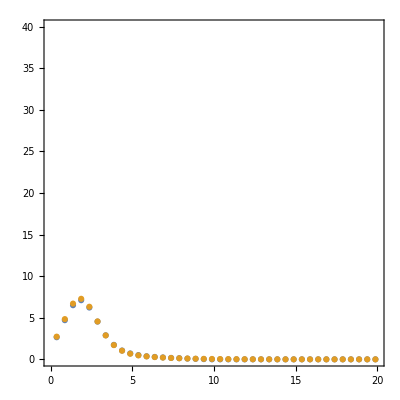

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

59

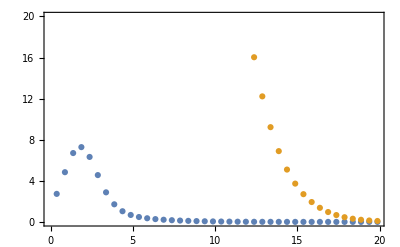

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

31

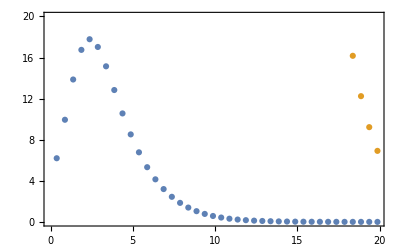

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-1.},{0.382,-0.8},{0.382,-0.6},{0.382,-0.4},{0.382,-0.2},{0.382,0.},{0.382,0.2},{0.382,0.4},{0.382,0.6},{0.382,0.8},{0.382,1.},{0.422,-1.},{0.422,-0.8},{0.422,-0.6},{0.422,-0.4},{0.422,-0.2},{0.422,0.},{0.422,0.2},{0.422,0.4},{0.422,0.6},{0.422,0.8},{0.422,1.},{0.462,-1.},{0.462,-0.8},{0.462,-0.6},{0.462,-0.4},{0.462,-0.2},{0.462,0.},{0.462,0.2},{0.462,0.4},{0.462,0.6},{0.462,0.8},{0.462,1.},{0.502,-1.},{0.502,-0.8},{0.502,-0.6},{0.502,-0.4},{0.502,-0.2},{0.502,0.},{0.502,0.2},{0.502,0.4},{0.502,0.6},{0.502,0.8},{0.502,1.},{0.542,-1.},{0.542,-0.8},{0.542,-0.6},{0.542,-0.4},{0.542,-0.2},{0.542,0.},{0.542,0.2},{0.542,0.4},{0.542,0.6},{0.542,0.8},{0.542,1.},{0.582,-1.},{0.582,-0.8},{0.582,-0.6},{0.582,-0.4},{0.582,-0.2},{0.582,0.},{0.582,0.2},{0.582,0.4},{0.582,0.6},{0.582,0.8},{0.582,1.},{0.622,-1.},{0.622,-0.8},{0.622,-0.6},{0.622,-0.4},{0.622,-0.2},{0.622,0.},{0.622,0.2},{0.622,0.4},{0.622,0.6},{0.622,0.8},{0.622,1.},{0.662,-1.},{0.662,-0.8},{0.662,-0.6},{0.662,-0.4},{0.662,-0.2},{0.662,0.},{0.662,0.2},{0.662,0.4},{0.662,0.6},{0.662,0.8},{0.662,1.},{0.702,-1.},{0.702,-0.8},{0.702,-0.6},{0.702,-0.4},{0.702,-0.2},{0.702,0.},{0.702,0.2},{0.702,0.4},{0.702,0.6},{0.702,0.8},{0.702,1.},{0.742,-1.},{0.742,-0.8},{0.742,-0.6},{0.742,-0.4},{0.742,-0.2},{0.742,0.},{0.742,0.2},{0.742,0.4},{0.742,0.6},{0.742,0.8},{0.742,1.},{0.782,-1.},{0.782,-0.8},{0.782,-0.6},{0.782,-0.4},{0.782,-0.2},{0.782,0.},{0.782,0.2},{0.782,0.4},{0.782,0.6},{0.782,0.8},{0.782,1.}}

```mathematica
dataSet1
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

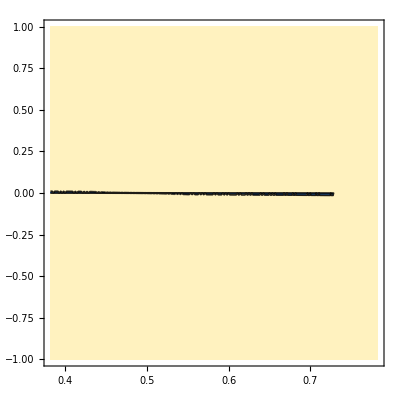

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

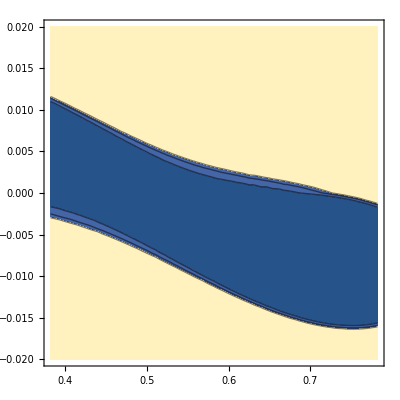

```mathematica
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]]/50,Max@ls23d[[All,2]]/50},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and dm31

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
pmut[s12_,c12_,s13_,c13_,s23_,c23_,δ_,dm31_,dm21_,ee_,emut_]=(dm31 (c23^4 ee emut^2 (-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2+dm31^2 (729.-1458. s13^2))+c23^3 ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+148.8066566943162 s13^2)) s23+c23^2 (c12^2 dm21 (-4.5474735088646407*^-13 dm31^2-2.7105054312137608*^-20 ee^2)+ee (1.9999999999999998 dm31^2-0.0008665646560000002 dm31 ee+9.386678787854984*^-8 ee^2+dm31 ((-3.5113576553450443+7.271321001515295*^-17 ⅈ) dm31+2.7105054312137608*^-20 ee+1101.7797307465376 dm31 emut^2) s13^2)) s23^2+c23 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.00000000000001-40.8066566943162 s13^2))) s23^3+ee (729. dm31^2-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2) emut^2 s23^4)+c23 dm31 (1101.7797307465376 c23^3 dm31^2 ee emut^2 s13^2+c23^2 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.-135.6133133886324 s13^2))) s23+c23 (c12^2 dm21 (4.5474735088646407*^-13 dm31^2+2.7105054312137608*^-20 ee^2)+ee (ee^2 (-9.386678787854984*^-8+0.00006842888836346283 emut^2)+dm31 ee (0.0008665646560000002-0.6317256342240002 emut^2-2.7105054312137608*^-20 s13^2)+dm31^2 (-1.9999999999999998+3.5113576553450443 s13^2+emut^2 (1458.-1458. s13^2)))) s23^2+ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+54. s13^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee]+c12 c23 dm21 s12 s13 (-8.673617379884035*^-19 c23^3 dm31 ee^2 emut+c23^2 ((-0.0004332823280000001 dm31+9.386678787854984*^-8 ee) ee^2+(-1.6442870905801747*^6 dm31^3+356.22026925346245 dm31^2 ee+0.31586281711200004 dm31 ee^2-0.00006842888836346282 ee^3) emut^2) s23+c23 (121799.04374667956 dm31^3-26.386686611367594 dm31^2 ee-0.046794491423999995 dm31 ee^2+0.000010137613090883384 ee^3) emut s23^2+(-2255.5378471607337 dm31^3+0.4886423446549555 dm31^2 ee+dm31 ee^2 (0.0004332823280000001-0.3158628171119999 emut^2)+ee^3 (-9.386678787854982*^-8+0.00006842888836346282 emut^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee-1. δ]-0.011698622856 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[δ]+2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[δ]-9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[δ]+2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[δ]+0.0008665646560000002 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[δ]-1.8773357575709967*^-7 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[δ]+1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[δ]-0.9475884513359999 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[δ]+0.00013685777672692564 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[δ]-747780.3248878407 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[δ]+54.00000000000003 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[δ]+0.093588982848 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[δ]-0.000015206419636325076 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[δ]+9231.855862812848 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[δ]-5.551115123125783*^-16 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[δ]-0.0012998469840000003 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[δ]+1.8773357575709967*^-7 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[δ]-1.3460045847981133*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[δ]+2916.000000000001 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[δ]+0.6317256342240001 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[δ]-0.00013685777672692564 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[δ]+249260.10829594688 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[δ]-54.00000000000001 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[δ]+2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[δ]+6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[1. δ]-1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[1. δ]-1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[1. δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[1. δ]+565081.7592678213 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[1. δ]-14.419970082948637 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[1. δ]-0.023397245712 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[1. δ]-6976.318015652115 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[1. δ]-0.48864234465495493 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[1. δ]+0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[1. δ]+1.0171471666820783*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[1. δ]-2203.559461493075 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[1. δ]-188360.5864226071 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[1. δ]+40.80665669431621 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[1. δ]-249260.10829594688 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+54.000000000000014 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+0.011698622856000002 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.0004332823280000001 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+9.386678787854984*^-8 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-6.730022923990566*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+1458.0000000000005 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.00006842888836346282 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+249260.10829594696 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-(0.035095868568+1.925929944387236*^-34 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]+5.068806545441692*^-6 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-1.9999999999999996 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.0008665646560000002 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-9.386678787854982*^-8 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-0.631725634224 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.00006842888836346282 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+0.023397245712 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+188360.5864226071 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-40.80665669431621 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+5.085735833410392*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1101.7797307465376 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-188360.5864226071 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]-13.19334330568379 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.011698622856 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.9999999999999998 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.31586281711200004 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]+954.9059770030174 c23^4 dm31^3 ee emut^2 s13^2 Sin[(3296.2634783428016 dm31)/ee]+177998.22783051126 c12^2 c23^3 dm21 dm31^3 emut s23 Sin[(3296.2634783428016 dm31)/ee]-77.12348653427833 c12^2 c23^3 dm21 dm31^2 ee emut s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c12^2 c23^3 dm21 dm31 ee^2 emut s23 Sin[(3296.2634783428016 dm31)/ee]-109.29551934143674 c23^3 dm31^3 ee emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c23^3 dm31^2 ee^2 emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]-6592.526956685602 c12^2 c23^2 dm21 dm31^3 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.856425427195494 c12^2 c23^2 dm21 dm31^2 ee s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c12^2 c23^2 dm21 dm31 ee^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+4.805952151423804*^6 c12^2 c23^2 dm21 dm31^3 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-2082.334136425515 c12^2 c23^2 dm21 dm31^2 ee emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c12^2 c23^2 dm21 dm31 ee^2 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.7380974557143687 c23^2 dm31^3 ee s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c23^2 dm31^2 ee^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-1041.1670682127576 c23^2 dm31^3 ee emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c23^2 dm31^2 ee^2 emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-177998.22783051128 c12^2 c23 dm21 dm31^3 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+77.12348653427834 c12^2 c23 dm21 dm31^2 ee emut s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c12^2 c23 dm21 dm31 ee^2 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+38.561743267139164 c23 dm31^3 ee emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c23 dm31^2 ee^2 emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]+4.407777171115168*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-954.9059770030176 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-326502.0126751977 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+70.7337760742976 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[δ]+4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[δ]-4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[δ]-5.534686227014404*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[δ]+2.3980817331903384*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[δ]-(2.5976160902274616*^-18+1.3877787807814457*^-17 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[δ]-7.471826406469446*^-10 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Sin[δ]+3.237410339806957*^-13 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Sin[δ]-3.5067817218070734*^-17 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Sin[δ]+6046.333568059216 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[1. δ]-1.3098847421166222 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[1. δ]+1.6187051699034782*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[1. δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[1. δ]+163251.00633759884 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[1. δ]-35.3668880371488 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[1. δ]+2.5976160902274616*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[1. δ]-4.8104001670878927*^-20 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Sin[1. δ]+163251.00633759884 c12 dm21 dm31^3 emut s12 s13 s23^4 Sin[1. δ]-35.3668880371488 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Sin[1. δ]-2.767343113507202*^-11 c12 c23^4 dm21 dm31^3 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.1990408665951692*^-14 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]-1.2988080451137308*^-18 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-7.471826406469446*^-10 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+3.237410339806957*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+2.767343113507202*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]-1.1990408665951692*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+1.2988080451137308*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+c12 dm21 dm31 s12 s13 (c23^4 dm31 (163251.00633759884 dm31-35.3668880371488 ee) emut+c23^3 dm31 (-6046.333568059216 dm31+1.3098847421166222 ee+4.407777171115168*^6 dm31 emut^2-954.9059770030176 ee emut^2) s23+c23^2 (-163251.00633759887 dm31^2+35.3668880371488 dm31 ee-1.2988080451137308*^-18 ee^2) emut s23^2+c23 ee (-1.1102230246251565*^-16 dm31+4.8104001670878927*^-20 ee+(1.6187051699034782*^-13 dm31-3.5067817218070734*^-17 ee) emut^2) s23^3+(-5.995204332975845*^-15 dm31+1.2988080451137308*^-18 ee) ee emut s23^4) Sin[(3296.2634783428016 dm31)/ee+1. δ])/(dm31 (dm31-0.00021664116400000005 ee)^2 ee);
```

```mathematica
ratioGen[S23_,δ_,dm31_,epS_,ee_]=(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,epS]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.s23->Sqrt[S23]/.Thread[{s12,s13,δ,dm21}->{Sqrt@0.31,Sqrt@0.02240,-2.5,7.39*10^-5}])/(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.Thread[{s12,s13,s23,δ,dm21,dm31}->{Sqrt@0.31,Sqrt@0.02240,Sqrt@0.582,-2.5,7.39*10^-5,2.525*10^-3}]);
```

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

116

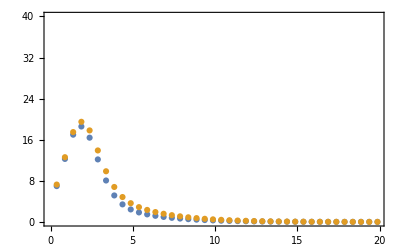

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

83

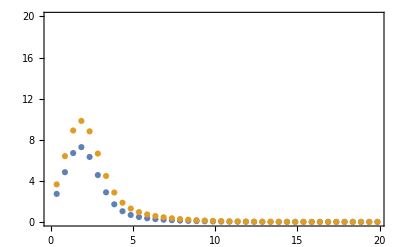

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet2=chis23d;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

24

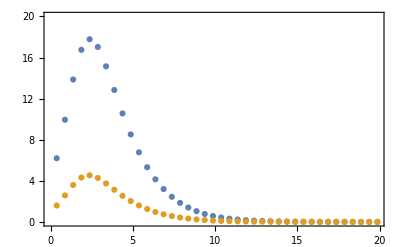

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,0.0005},{0.382,0.0012},{0.382,0.0019},{0.382,0.0026},{0.382,0.0033},{0.382,0.004},{0.382,0.0047},{0.382,0.0054},{0.382,0.0061},{0.382,0.0068},{0.382,0.0075},{0.422,0.0005},{0.422,0.0012},{0.422,0.0019},{0.422,0.0026},{0.422,0.0033},{0.422,0.004},{0.422,0.0047},{0.422,0.0054},{0.422,0.0061},{0.422,0.0068},{0.422,0.0075},{0.462,0.0005},{0.462,0.0012},{0.462,0.0019},{0.462,0.0026},{0.462,0.0033},{0.462,0.004},{0.462,0.0047},{0.462,0.0054},{0.462,0.0061},{0.462,0.0068},{0.462,0.0075},{0.502,0.0005},{0.502,0.0012},{0.502,0.0019},{0.502,0.0026},{0.502,0.0033},{0.502,0.004},{0.502,0.0047},{0.502,0.0054},{0.502,0.0061},{0.502,0.0068},{0.502,0.0075},{0.542,0.0005},{0.542,0.0012},{0.542,0.0019},{0.542,0.0026},{0.542,0.0033},{0.542,0.004},{0.542,0.0047},{0.542,0.0054},{0.542,0.0061},{0.542,0.0068},{0.542,0.0075},{0.582,0.0005},{0.582,0.0012},{0.582,0.0019},{0.582,0.0026},{0.582,0.0033},{0.582,0.004},{0.582,0.0047},{0.582,0.0054},{0.582,0.0061},{0.582,0.0068},{0.582,0.0075},{0.622,0.0005},{0.622,0.0012},{0.622,0.0019},{0.622,0.0026},{0.622,0.0033},{0.622,0.004},{0.622,0.0047},{0.622,0.0054},{0.622,0.0061},{0.622,0.0068},{0.622,0.0075},{0.662,0.0005},{0.662,0.0012},{0.662,0.0019},{0.662,0.0026},{0.662,0.0033},{0.662,0.004},{0.662,0.0047},{0.662,0.0054},{0.662,0.0061},{0.662,0.0068},{0.662,0.0075},{0.702,0.0005},{0.702,0.0012},{0.702,0.0019},{0.702,0.0026},{0.702,0.0033},{0.702,0.004},{0.702,0.0047},{0.702,0.0054},{0.702,0.0061},{0.702,0.0068},{0.702,0.0075},{0.742,0.0005},{0.742,0.0012},{0.742,0.0019},{0.742,0.0026},{0.742,0.0033},{0.742,0.004},{0.742,0.0047},{0.742,0.0054},{0.742,0.0061},{0.742,0.0068},{0.742,0.0075},{0.782,0.0005},{0.782,0.0012},{0.782,0.0019},{0.782,0.0026},{0.782,0.0033},{0.782,0.004},{0.782,0.0047},{0.782,0.0054},{0.782,0.0061},{0.782,0.0068},{0.782,0.0075}}

```mathematica
dataSet1
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet2
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet3
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

### Contour

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

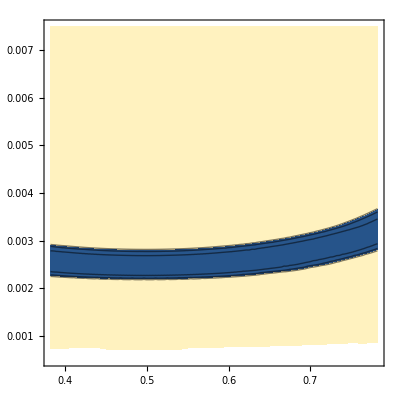

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

```mathematica
f[S23_]=2*Sqrt[S23]*Sqrt[1-S23];
```

```mathematica
(* sin^2(2θ) = 2 sin(θ)cos(θ) *)
```

```mathematica
Ls23d=MapAt[f,ls23d,{{All,1}}];
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000714286,0.0005005} lies outside the range of data in the interpolating function. Extrapolation will be used.

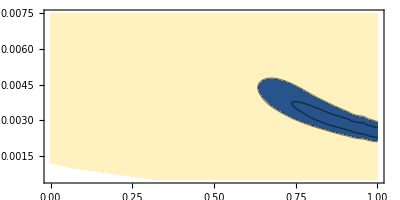

```mathematica
Table[{Ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,0,1},{del,Min@Ls23d[[All,2]],Max@Ls23d[[All,2]]},Contours->{2.3,11.3},AspectRatio->1/2]
```

```mathematica
(* compare with fig5 *)
```

```mathematica
(* In this plot, all the other parameters are fixed. In the paper, some of the parameters are marginalized over, so the region increases *)
```

## All data sets - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

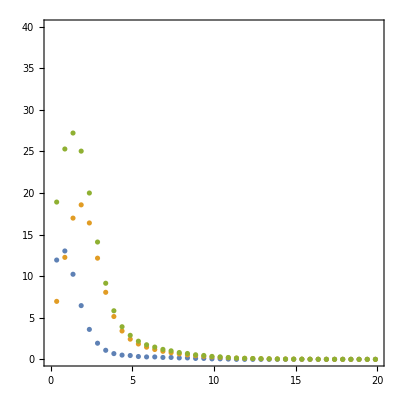

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

7

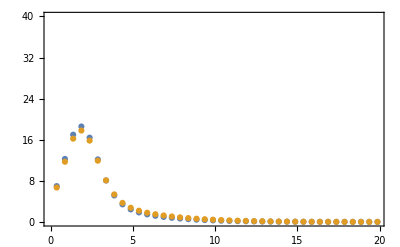

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{28.3962,20.0561,13.473,8.48504,4.90884,2.53512,1.12547,0.41493,0.129763,0.033219,0,0.0851642,0.530114,1.69353,3.96106,7.68465,13.1592,20.622,30.2605,42.2222,56.6229}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{26.7438,18.8169,12.5569,7.8262,4.46343,2.23905,0.940361,0.305468,0.0803148,0.0203945,0,0.0693769,0.349385,1.1892,2.90543,5.81323,10.1929,16.2781,24.2095,34.1355,46.1896}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.4,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

16

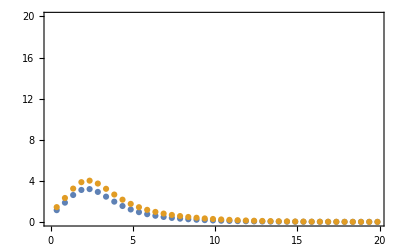

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

```mathematica
$10^{-7}<|U_{\mu N|<10^{-6}$
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{16.3418,11.4956,7.66016,4.75525,2.68211,1.32124,0.532046,0.156096,0.0287278,0.00489495,0,0.0279364,0.204785,0.710923,1.74161,3.47406,6.05469,9.59844,14.1928,19.9032,26.7776}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{13.5199,9.48621,6.2993,3.89433,2.19369,1.10889,0.437802,0.152519,0.0223227,0.00154476,0,0.0185817,0.147654,0.430076,1.12841,2.30451,4.11401,6.68495,10.0987,14.4203,19.6991}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

3

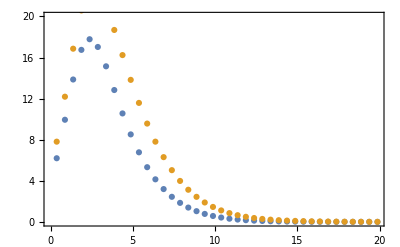

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{71.5077,48.7148,31.1906,18.4048,9.71496,4.37153,1.54253,0.369311,0.0608871,0.0240377,0,0.149249,1.02924,3.46918,8.40769,16.7598,29.3379,46.8204,69.7501,98.5474,133.53}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{62.1666,41.8594,26.7319,15.8053,8.38644,3.81451,1.38085,0.348416,0.0515139,0.0186567,0,0.110054,0.759913,2.63468,6.51664,13.2374,23.5567,38.2631,58.3354,84.2725,116.45}

{-0.5,-0.5,-0.45,-0.35,-0.25,-0.15,-0.1,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.35,-0.45,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

{-0.5,-0.5,-0.4,-0.3,-0.2,-0.15,-0.05,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.3,-0.4,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataSet1
dataSet1bg
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

```mathematica
dataSet2
dataSet2bg
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

```mathematica
dataSet3
dataSet3bg
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{99.6392,68.7999,44.8489,27.1243,14.8336,7.05247,2.7429,0.806004,0.188038,0.0532728,0,0.224871,1.51212,5.03454,12.0946,23.9301,41.6158,66.035,97.8887,137.72,185.94}

InterpolatingFunction[…]

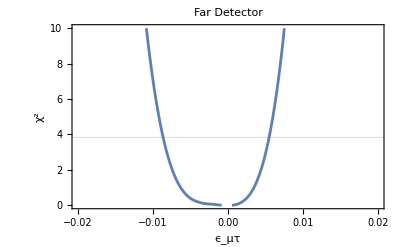

far_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{88.6546,60.9194,39.6349,23.9027,13.0422,6.2021,2.38902,0.696917,0.13213,0.0347965,0,0.17544,1.11113,3.72625,9.26041,18.679,33.0874,53.3481,80.4424,115.093,157.713}

InterpolatingFunction[…]

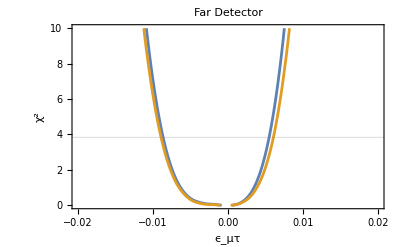

far_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg.pdf",%]
```

## All data sets - NSI - s23

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

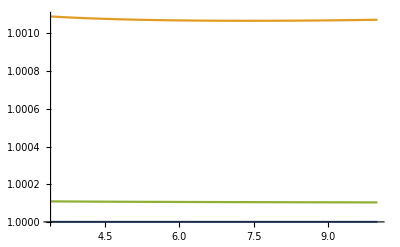

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,5.97521},{0.875,10.5096},{1.375,14.5549},{1.875,15.9213},{2.375,14.0555},{2.875,10.4278},{3.375,6.90915},{3.875,4.41438},{4.375,2.92321},{4.875,2.08077},{5.375,1.58208},{5.875,1.25399},{6.375,1.01521},{6.875,0.829789},{7.375,0.680839},{7.875,0.559192},{8.375,0.459032},{8.875,0.376232},{9.375,0.30767},{9.875,0.25089},{10.375,0.203914},{10.875,0.165121},{11.375,0.133169},{11.875,0.106934},{12.375,0.0854736},{12.875,0.0679899},{13.375,0.0538103},{13.875,0.0423658},{14.375,0.033176},{14.875,0.0258362},{15.375,0.0200064},{15.875,0.0154025},{16.375,0.0117882},{16.875,0.00896776},{17.375,0.00678044},{17.875,0.0050947},{18.375,0.0038038},{18.875,0.00282166},{19.375,0.00207936},{19.875,0.00152208}}

55

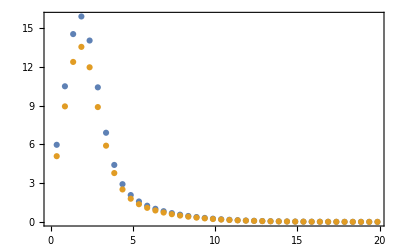

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.19938,3.6876,3.1865,2.73558,2.38034,2.17296,2.17336,2.45046,3.08376,4.16544,5.80309,2.08659,1.78334,1.48265,1.21824,1.02999,0.964689,1.07698,1.43064,2.10026,3.17338,4.7533,0.881103,0.723319,0.56148,0.42279,0.340715,0.355654,0.515863,0.878675,1.51213,2.49707,3.93001,0.313037,0.244963,0.167554,0.100801,0.0709793,0.111225,0.262365,0.574046,1.10624,1.93128,3.13648,0.113778,0.0932068,0.0590252,0.0234408,0.00488443,0.0284729,0.126709,0.34047,0.720352,1.32849,2.24098,0.072617,0.0781587,0.0665119,0.0417548,0.0140558,0,0.0231391,0.114806,0.315254,0.675219,1.25803,0.104231,0.140472,0.156577,0.148471,0.117977,0.0729988,0.0279144,0.00420515,0.0313713,0.148211,0.404574,0.281975,0.379024,0.453885,0.494627,0.49498,0.454386,0.378241,0.278349,0.17362,0.0910758,0.0672549,0.808079,1.01572,1.20048,1.34307,1.42963,1.4516,1.40589,1.29512,1.12815,0.920874,0.697247,1.94708,2.32725,2.68561,2.99615,3.238,3.3952,3.45677,3.41681,3.27488,3.03652,2.71408,3.96799,4.58859,5.19048,5.74157,6.2146,6.58685,6.84008,6.96054,6.93923,6.77221,6.46121}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.59946,3.1608,2.73128,2.34479,2.04029,1.86253,1.86288,2.1004,2.64322,3.57038,4.97408,1.78851,1.52858,1.27084,1.0442,0.882849,0.826877,0.923124,1.22626,1.80023,2.72004,4.07426,0.755231,0.619988,0.481268,0.362391,0.292041,0.304846,0.442168,0.75315,1.29611,2.14035,3.36858,0.268317,0.209968,0.143618,0.0864011,0.0608394,0.0953355,0.224884,0.492039,0.948209,1.65538,2.68841,0.0975238,0.0798915,0.050593,0.0200921,0.00418666,0.0244053,0.108608,0.291831,0.617445,1.1387,1.92084,0.0622431,0.0669931,0.0570102,0.0357898,0.0120478,0,0.0198335,0.0984049,0.270218,0.578759,1.07831,0.0893413,0.120405,0.134209,0.127261,0.101123,0.0625704,0.0239267,0.00360441,0.0268897,0.127038,0.346778,0.241693,0.324877,0.389044,0.423966,0.424269,0.389473,0.324207,0.238585,0.148817,0.078065,0.0576471,0.692639,0.870618,1.02898,1.1512,1.2254,1.24423,1.20505,1.1101,0.966988,0.789321,0.59764,1.66892,1.99478,2.30195,2.56813,2.77543,2.91017,2.96295,2.9287,2.80704,2.60273,2.32636,3.40114,3.93308,4.44898,4.92135,5.3268,5.64587,5.86292,5.96618,5.94791,5.80475,5.53818}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.43082,3.09641,2.7443,2.43014,2.12868,1.88952,1.73289,1.68081,1.75605,2.02625,2.44923,1.65116,1.46916,1.27161,1.06658,0.912752,0.795304,0.746283,0.804661,0.976631,1.30322,1.84457,0.670721,0.567877,0.465006,0.381396,0.298846,0.254403,0.301402,0.387914,0.627136,0.967843,1.51749,0.216902,0.183572,0.15009,0.0955452,0.0576864,0.0651362,0.127532,0.231547,0.467023,0.785177,1.301,0.0866661,0.0734133,0.0477453,0.0203391,0.00410117,0.0164407,0.0776067,0.150679,0.323573,0.595105,0.988929,0.0510556,0.0549533,0.0467423,0.0293143,0.00985255,0,0.0161401,0.0778333,0.150273,0.319009,0.589129,0.0813634,0.094115,0.0997205,0.0968197,0.0868008,0.0580408,0.0237476,0.00368215,0.0182647,0.0833745,0.178249,0.198329,0.248156,0.288677,0.311272,0.311437,0.288858,0.247584,0.196328,0.148896,0.0868912,0.0499761,0.617956,0.754572,0.862955,0.937034,0.983046,0.994799,0.970224,0.911615,0.825986,0.691608,0.545926,1.55387,1.78672,2.01198,2.21053,2.34992,2.43674,2.47098,2.44862,2.3699,2.23621,2.02965,3.26939,3.64452,4.01883,4.36838,4.66456,4.87848,5.02577,5.09627,5.08367,4.98586,4.80543}

{-0.15,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.,0.05,0.1,0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.05,0.1,0.15,-0.05,0.,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.98723,2.67693,2.37512,2.10583,1.8303,1.6253,1.48533,1.44069,1.5109,1.74566,2.1222,1.43814,1.28214,1.09566,0.919924,0.788073,0.681689,0.639671,0.695424,0.842826,1.1399,1.60474,0.580618,0.492466,0.404291,0.332625,0.256153,0.218059,0.258345,0.338212,0.54326,0.852436,1.34395,0.19163,0.163062,0.133768,0.0818959,0.0494455,0.055831,0.115027,0.204183,0.40602,0.695866,1.14163,0.0760555,0.0629257,0.0409245,0.0174336,0.00351529,0.014092,0.068221,0.134867,0.283062,0.532948,0.870511,0.0437619,0.0471028,0.0400648,0.0251265,0.00844504,0,0.0138344,0.0684058,0.13452,0.279151,0.527825,0.0697401,0.0863843,0.091189,0.0887026,0.0784523,0.0497493,0.0203551,0.00315613,0.0156554,0.0771782,0.158499,0.17571,0.21842,0.253151,0.272519,0.27266,0.253307,0.217929,0.173995,0.13334,0.0744782,0.0428367,0.535391,0.65249,0.758147,0.826029,0.865468,0.875542,0.854478,0.804241,0.716474,0.598521,0.473651,1.35474,1.55433,1.74741,1.9176,2.05161,2.13931,2.16942,2.15024,2.07197,1.93961,1.76256,2.83435,3.1753,3.49614,3.79576,4.05655,4.26378,4.39923,4.45966,4.44886,4.36502,4.19333}

{-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.,0.05,0.05,0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.1,0.,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.2,-0.2,-0.2,-0.2,-0.15}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.979577},{0.875,1.60576},{1.375,2.24307},{1.875,2.66511},{2.375,2.73731},{2.875,2.50178},{3.375,2.10684},{3.875,1.69048},{4.375,1.32699},{4.875,1.03671},{5.375,0.813371},{5.875,0.643145},{6.375,0.512847},{6.875,0.412122},{7.375,0.333351},{7.875,0.271034},{8.375,0.221205},{8.875,0.180984},{9.375,0.148262},{9.875,0.121474},{10.375,0.0994442},{10.875,0.081275},{11.375,0.0662689},{11.875,0.0538743},{12.375,0.0436474},{12.875,0.0352256},{13.375,0.0283093},{13.875,0.0226483},{14.375,0.0180327},{14.875,0.0142853},{15.375,0.011257},{15.875,0.00882189},{16.375,0.00687398},{16.875,0.00532439},{17.375,0.00409878},{17.875,0.00313526},{18.375,0.00238252},{18.875,0.0017983},{19.375,0.00134793},{19.875,0.00100317}}

89

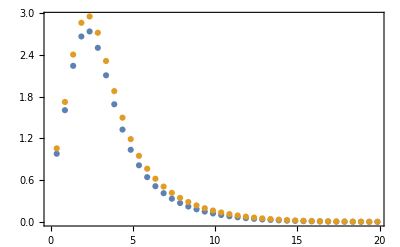

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{2.1738,1.97201,1.75814,1.54047,1.32839,1.13249,0.964799,0.838901,0.770232,0.776363,0.877386,1.0594,0.941582,0.814347,0.685046,0.562279,0.45604,0.377896,0.341217,0.361476,0.456628,0.647596,0.428012,0.369385,0.3038,0.237409,0.177731,0.133797,0.11634,0.138042,0.21387,0.361503,0.601897,0.135178,0.112345,0.0844725,0.056225,0.033713,0.0246238,0.0384074,0.0865294,0.182808,0.343864,0.589713,0.0363124,0.0305774,0.0208367,0.0100026,0.00246392,0.00419558,0.0229238,0.0683592,0.152514,0.29013,0.499251,0.0175296,0.0188374,0.0160143,0.0100465,0.00338024,0,0.00556081,0.0275834,0.0757278,0.162167,0.302095,0.0326801,0.0424328,0.0466954,0.0445033,0.0362929,0.0239457,0.0108816,0.00220702,0.00493267,0.0282754,0.084073,0.121765,0.152605,0.175537,0.187768,0.187819,0.175531,0.152124,0.120301,0.0844041,0.0506484,0.0274398,0.394436,0.467118,0.528751,0.574939,0.602482,0.609363,0.594777,0.559188,0.504448,0.433956,0.352899,0.993469,1.13284,1.25768,1.36224,1.44183,1.49281,1.51257,1.49957,1.45344,1.37504,1.26667,2.0633,2.29505,2.50878,2.69763,2.85564,2.97777,3.05983,3.09855,3.09156,3.03748,2.93607}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{1.86326,1.69029,1.50698,1.32041,1.13862,0.970708,0.82697,0.719058,0.660199,0.665454,0.752045,0.908061,0.80707,0.698012,0.587182,0.481953,0.390891,0.323911,0.292472,0.309837,0.391395,0.555082,0.366867,0.316615,0.2604,0.203493,0.15234,0.114683,0.0997197,0.118322,0.183317,0.30986,0.515912,0.115867,0.0962957,0.072405,0.0481929,0.0288968,0.0211061,0.0329207,0.0741681,0.156693,0.294741,0.505468,0.0311249,0.0262092,0.01786,0.00857365,0.00211193,0.00359621,0.019649,0.0585936,0.130726,0.248683,0.427929,0.0150254,0.0161463,0.0137266,0.00861133,0.00289735,0,0.00476641,0.0236429,0.0649096,0.139001,0.258939,0.0280115,0.036371,0.0400247,0.0381457,0.0311082,0.0205249,0.00932706,0.00189173,0.004228,0.0242361,0.0720626,0.10437,0.130805,0.15046,0.160944,0.160987,0.150455,0.130392,0.103115,0.0723463,0.0434129,0.0235198,0.338088,0.400387,0.453215,0.492805,0.516413,0.522312,0.509809,0.479304,0.432384,0.371962,0.302485,0.851545,0.971006,1.07801,1.16763,1.23585,1.27955,1.29649,1.28535,1.24581,1.17861,1.08571,1.76854,1.96719,2.15039,2.31225,2.44769,2.55237,2.62271,2.6559,2.64991,2.60356,2.51663}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.4962,1.39209,1.28212,1.17049,1.06184,0.933223,0.803367,0.688849,0.595895,0.531148,0.50166,0.719014,0.652974,0.581028,0.506816,0.434479,0.368672,0.314577,0.277922,0.24628,0.213473,0.214076,0.276114,0.250259,0.221865,0.193943,0.170097,0.133122,0.0964356,0.0740323,0.0719378,0.096898,0.156434,0.104566,0.0901281,0.0718502,0.0519613,0.0333249,0.0194592,0.0145672,0.0235785,0.052204,0.107004,0.188631,0.0222937,0.0191689,0.0137685,0.0074817,0.00237613,0.00121976,0.0075154,0.0255495,0.0604565,0.118302,0.179889,0.00828693,0.00890529,0.00756465,0.00473774,0.00158994,0,0.00259463,0.0127985,0.034902,0.0741496,0.136854,0.0201793,0.0254302,0.0277032,0.0265316,0.0221248,0.0153855,0.0079417,0.00219329,0.0013763,0.00964824,0.032199,0.0957452,0.114875,0.128799,0.136144,0.136171,0.128784,0.114564,0.0948051,0.0715718,0.0477784,0.0272877,0.258898,0.291057,0.318696,0.339594,0.352119,0.355248,0.348587,0.332407,0.307699,0.276242,0.240693,0.678762,0.756335,0.825495,0.883262,0.927165,0.950329,0.958737,0.953179,0.933524,0.890265,0.830385,1.43197,1.5514,1.662,1.76007,1.84239,1.90618,1.94911,1.96938,1.9657,1.93736,1.8843}

{-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.30531,1.21608,1.12182,1.02613,0.925093,0.805619,0.694314,0.596156,0.516482,0.460984,0.435709,0.622012,0.565406,0.503738,0.440128,0.378125,0.321719,0.275352,0.243933,0.211097,0.182977,0.183494,0.242383,0.220222,0.195884,0.171951,0.151512,0.114105,0.0826591,0.0634563,0.0616609,0.0830554,0.134086,0.089628,0.0772527,0.0615859,0.0445382,0.0285642,0.0166793,0.0124862,0.0202101,0.0447463,0.0917177,0.167398,0.0191089,0.0164304,0.0118016,0.00641289,0.00203669,0.00104551,0.00644178,0.0218995,0.0518199,0.101402,0.159905,0.00710308,0.00763311,0.00648398,0.00406092,0.00136281,0,0.00222397,0.0109702,0.029916,0.0635568,0.117303,0.0172965,0.0217973,0.0237456,0.0227414,0.0189641,0.0131876,0.00680717,0.00187996,0.00117969,0.00826992,0.0275991,0.0820673,0.0984644,0.110399,0.116695,0.116718,0.110387,0.0981981,0.0812615,0.0613473,0.0409529,0.0233895,0.227627,0.255191,0.278883,0.296795,0.307531,0.310213,0.304503,0.290634,0.269456,0.242493,0.212022,0.58751,0.654001,0.713281,0.762796,0.800427,0.824508,0.833832,0.827685,0.805878,0.768799,0.717472,1.25026,1.35263,1.44743,1.53149,1.60205,1.65672,1.69352,1.7109,1.70774,1.68345,1.63797}

{-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,5.31141},{0.875,8.52311},{1.375,11.8828},{1.875,14.3551},{2.375,15.243},{2.875,14.597},{3.375,12.9826},{3.875,11.0043},{4.375,9.05147},{4.875,7.30118},{5.375,5.80644},{5.875,4.56467},{6.375,3.55219},{6.875,2.73878},{7.375,2.09367},{7.875,1.58801},{8.375,1.19593},{8.875,0.894927},{9.375,0.665937},{9.875,0.493159},{10.375,0.363746},{10.875,0.267439},{11.375,0.196167},{11.875,0.143667},{12.375,0.105139},{12.875,0.0769445},{13.375,0.056349},{13.875,0.0413177},{14.375,0.0303467},{14.875,0.0223318},{15.375,0.0164668},{15.875,0.0121652},{16.375,0.00900182},{16.875,0.00666892},{17.375,0.00494369},{17.875,0.00366465},{18.375,0.00271451},{18.875,0.00200775},{19.375,0.00148172},{19.875,0.00109031}}

10

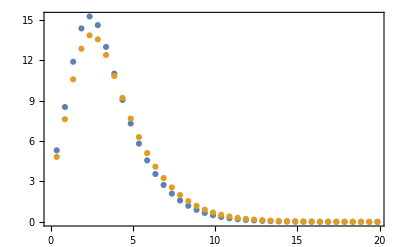

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.71253,8.55107,7.32212,6.07404,4.86166,3.74703,2.80025,2.10062,1.73802,1.81459,2.44687,4.71679,4.046,3.32419,2.59454,1.90761,1.32217,0.906213,0.738316,0.909374,1.5248,2.70733,1.93792,1.60714,1.23926,0.870506,0.545195,0.316553,0.247841,0.41384,0.902798,1.81897,3.28592,0.651524,0.522718,0.366596,0.210607,0.0907176,0.0521888,0.150667,0.453681,1.04263,2.01544,3.49007,0.198813,0.165826,0.11001,0.0484669,0.0069699,0.0206032,0.134736,0.406391,0.906109,1.72047,2.95544,0.102886,0.110532,0.0939505,0.0589324,0.0198265,0,0.0326126,0.161762,0.444087,0.950961,1.77146,0.178044,0.234057,0.258565,0.245915,0.198683,0.127929,0.0537452,0.0061282,0.0262569,0.168268,0.501691,0.578366,0.752421,0.882364,0.9518,0.952046,0.882212,0.749524,0.569938,0.369085,0.183621,0.06312,1.75622,2.16642,2.51559,2.77788,2.93448,2.97359,2.89052,2.68813,2.37745,1.97865,1.52247,4.35636,5.14946,5.8617,6.45928,6.91471,7.2066,7.31973,7.24519,6.98086,6.53204,5.91244,9.09909,10.4314,11.6618,12.7499,13.661,14.3655,14.8391,15.0625,15.022,14.7097,14.1243}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{8.32502,7.32949,6.2761,5.20632,4.16714,3.21174,2.40021,1.80053,1.48973,1.55536,2.09732,4.04297,3.468,2.84931,2.22389,1.6351,1.13329,0.776754,0.632842,0.779463,1.30697,2.32057,1.66108,1.37755,1.06222,0.746148,0.46731,0.271331,0.212435,0.35472,0.773827,1.55911,2.81651,0.558449,0.448044,0.314225,0.18052,0.0777579,0.0447333,0.129143,0.38887,0.893686,1.72752,2.99149,0.170411,0.142136,0.0942939,0.0415431,0.0059742,0.0176599,0.115488,0.348335,0.776665,1.47469,2.53323,0.0881883,0.0947413,0.080529,0.0505135,0.0169942,0,0.0279537,0.138653,0.380646,0.815109,1.51839,0.152609,0.200621,0.221627,0.210784,0.1703,0.109654,0.0460673,0.00525274,0.0225059,0.144229,0.430021,0.495742,0.644932,0.756312,0.815829,0.81604,0.756182,0.642449,0.488519,0.316359,0.15739,0.0541028,1.50533,1.85693,2.15622,2.38104,2.51527,2.54879,2.47759,2.30411,2.03781,1.69599,1.30497,3.73402,4.41382,5.02431,5.53653,5.9269,6.17709,6.27405,6.21016,5.9836,5.59889,5.0678,7.79922,8.94123,9.99581,10.9285,11.7094,12.3133,12.7192,12.9107,12.876,12.6083,12.1066}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{7.5996,6.74226,5.84699,4.93279,4.04833,3.21421,2.49738,1.9385,1.57721,1.46976,1.6778,3.62208,3.15025,2.62479,2.10147,1.59961,1.16979,0.829483,0.648861,0.671476,0.946612,1.52957,1.46363,1.22409,0.961372,0.709379,0.464639,0.297464,0.209213,0.274966,0.534971,1.02432,1.81789,0.481854,0.386761,0.274438,0.168086,0.0879084,0.0431671,0.099724,0.263517,0.600593,1.16335,2.00345,0.135079,0.114789,0.0824833,0.0431234,0.00670463,0.0153694,0.0857709,0.248038,0.548299,1.04346,1.76158,0.0738575,0.0778969,0.069246,0.0488516,0.0164187,0,0.0269213,0.104245,0.280694,0.587065,1.08981,0.121977,0.15719,0.173064,0.164835,0.13474,0.0922342,0.0476354,0.00595185,0.0197487,0.103708,0.310079,0.426849,0.544393,0.628391,0.674163,0.674319,0.628267,0.542507,0.420603,0.275305,0.149689,0.0610675,1.33024,1.61382,1.85374,2.03727,2.14801,2.17578,2.11682,1.97414,1.75809,1.48718,1.16024,3.36063,3.92587,4.4441,4.87137,5.1938,5.40221,5.48331,5.42982,5.24085,4.92254,4.48123,7.13806,8.10721,9.00836,9.81705,10.4815,10.9973,11.3462,11.5113,11.4813,11.2506,10.8201}

{-0.3,-0.25,-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.05,-0.2,-0.2,-0.15,-0.15,-0.1,-0.1,-0.05,0.,0.05,0.1,0.15,-0.15,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.15,0.2,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.15,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.2,-0.2,-0.2,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.2,-0.25,-0.3,-0.3,-0.3,-0.35,-0.35,-0.35,-0.35,-0.35,-0.35,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{6.66208,5.92194,5.12264,4.31954,3.53214,2.80647,2.16347,1.66729,1.35646,1.25979,1.44383,3.19097,2.75811,2.30124,1.84402,1.39395,1.01669,0.716699,0.556166,0.581265,0.827901,1.3469,1.27978,1.07207,0.846891,0.619932,0.403976,0.260683,0.179326,0.241399,0.466012,0.900849,1.60962,0.418732,0.337224,0.240947,0.149788,0.0753501,0.0370003,0.091192,0.231586,0.537651,1.03952,1.77841,0.121496,0.104105,0.0764143,0.0369629,0.00574682,0.0131738,0.0792322,0.218318,0.492828,0.920758,1.56136,0.0690207,0.0724831,0.065068,0.0418728,0.0140732,0,0.0230754,0.0950674,0.246309,0.526056,0.964473,0.110266,0.140448,0.154055,0.147001,0.121206,0.0847721,0.0408303,0.00510159,0.0169275,0.0946068,0.271496,0.371585,0.482829,0.561478,0.600712,0.600845,0.561372,0.48094,0.366231,0.24169,0.134019,0.0523436,1.16306,1.42336,1.64035,1.79766,1.89258,1.91638,1.86584,1.74354,1.55836,1.30349,1.01735,2.95332,3.45646,3.90066,4.27875,4.56973,4.75738,4.83032,4.78223,4.61213,4.325,3.93248,6.2612,7.11816,7.92156,8.62033,9.207,9.66418,9.97307,10.1192,10.0927,9.88851,9.50725}

{-0.25,-0.25,-0.2,-0.2,-0.15,-0.15,-0.1,-0.05,0.,0.,0.05,-0.15,-0.15,-0.15,-0.1,-0.1,-0.05,-0.05,0.,0.05,0.05,0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,0.,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.15,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.25,-0.25,-0.25,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.01,0.482},{-0.01,0.502},{-0.01,0.522},{-0.01,0.542},{-0.01,0.562},{-0.01,0.582},{-0.01,0.602},{-0.01,0.622},{-0.01,0.642},{-0.01,0.662},{-0.01,0.682},{-0.008,0.482},{-0.008,0.502},{-0.008,0.522},{-0.008,0.542},{-0.008,0.562},{-0.008,0.582},{-0.008,0.602},{-0.008,0.622},{-0.008,0.642},{-0.008,0.662},{-0.008,0.682},{-0.006,0.482},{-0.006,0.502},{-0.006,0.522},{-0.006,0.542},{-0.006,0.562},{-0.006,0.582},{-0.006,0.602},{-0.006,0.622},{-0.006,0.642},{-0.006,0.662},{-0.006,0.682},{-0.004,0.482},{-0.004,0.502},{-0.004,0.522},{-0.004,0.542},{-0.004,0.562},{-0.004,0.582},{-0.004,0.602},{-0.004,0.622},{-0.004,0.642},{-0.004,0.662},{-0.004,0.682},{-0.002,0.482},{-0.002,0.502},{-0.002,0.522},{-0.002,0.542},{-0.002,0.562},{-0.002,0.582},{-0.002,0.602},{-0.002,0.622},{-0.002,0.642},{-0.002,0.662},{-0.002,0.682},{0.,0.482},{0.,0.502},{0.,0.522},{0.,0.542},{0.,0.562},{0.,0.582},{0.,0.602},{0.,0.622},{0.,0.642},{0.,0.662},{0.,0.682},{0.002,0.482},{0.002,0.502},{0.002,0.522},{0.002,0.542},{0.002,0.562},{0.002,0.582},{0.002,0.602},{0.002,0.622},{0.002,0.642},{0.002,0.662},{0.002,0.682},{0.004,0.482},{0.004,0.502},{0.004,0.522},{0.004,0.542},{0.004,0.562},{0.004,0.582},{0.004,0.602},{0.004,0.622},{0.004,0.642},{0.004,0.662},{0.004,0.682},{0.006,0.482},{0.006,0.502},{0.006,0.522},{0.006,0.542},{0.006,0.562},{0.006,0.582},{0.006,0.602},{0.006,0.622},{0.006,0.642},{0.006,0.662},{0.006,0.682},{0.008,0.482},{0.008,0.502},{0.008,0.522},{0.008,0.542},{0.008,0.562},{0.008,0.582},{0.008,0.602},{0.008,0.622},{0.008,0.642},{0.008,0.662},{0.008,0.682},{0.01,0.482},{0.01,0.502},{0.01,0.522},{0.01,0.542},{0.01,0.562},{0.01,0.582},{0.01,0.602},{0.01,0.622},{0.01,0.642},{0.01,0.662},{0.01,0.682}}

```mathematica
dataSet1
dataSet1bg
```

{3.59946,3.1608,2.73128,2.34479,2.04029,1.86253,1.86288,2.1004,2.64322,3.57038,4.97408,1.78851,1.52858,1.27084,1.0442,0.882849,0.826877,0.923124,1.22626,1.80023,2.72004,4.07426,0.755231,0.619988,0.481268,0.362391,0.292041,0.304846,0.442168,0.75315,1.29611,2.14035,3.36858,0.268317,0.209968,0.143618,0.0864011,0.0608394,0.0953355,0.224884,0.492039,0.948209,1.65538,2.68841,0.0975238,0.0798915,0.050593,0.0200921,0.00418666,0.0244053,0.108608,0.291831,0.617445,1.1387,1.92084,0.0622431,0.0669931,0.0570102,0.0357898,0.0120478,0,0.0198335,0.0984049,0.270218,0.578759,1.07831,0.0893413,0.120405,0.134209,0.127261,0.101123,0.0625704,0.0239267,0.00360441,0.0268897,0.127038,0.346778,0.241693,0.324877,0.389044,0.423966,0.424269,0.389473,0.324207,0.238585,0.148817,0.078065,0.0576471,0.692639,0.870618,1.02898,1.1512,1.2254,1.24423,1.20505,1.1101,0.966988,0.789321,0.59764,1.66892,1.99478,2.30195,2.56813,2.77543,2.91017,2.96295,2.9287,2.80704,2.60273,2.32636,3.40114,3.93308,4.44898,4.92135,5.3268,5.64587,5.86292,5.96618,5.94791,5.80475,5.53818}

{2.98723,2.67693,2.37512,2.10583,1.8303,1.6253,1.48533,1.44069,1.5109,1.74566,2.1222,1.43814,1.28214,1.09566,0.919924,0.788073,0.681689,0.639671,0.695424,0.842826,1.1399,1.60474,0.580618,0.492466,0.404291,0.332625,0.256153,0.218059,0.258345,0.338212,0.54326,0.852436,1.34395,0.19163,0.163062,0.133768,0.0818959,0.0494455,0.055831,0.115027,0.204183,0.40602,0.695866,1.14163,0.0760555,0.0629257,0.0409245,0.0174336,0.00351529,0.014092,0.068221,0.134867,0.283062,0.532948,0.870511,0.0437619,0.0471028,0.0400648,0.0251265,0.00844504,0,0.0138344,0.0684058,0.13452,0.279151,0.527825,0.0697401,0.0863843,0.091189,0.0887026,0.0784523,0.0497493,0.0203551,0.00315613,0.0156554,0.0771782,0.158499,0.17571,0.21842,0.253151,0.272519,0.27266,0.253307,0.217929,0.173995,0.13334,0.0744782,0.0428367,0.535391,0.65249,0.758147,0.826029,0.865468,0.875542,0.854478,0.804241,0.716474,0.598521,0.473651,1.35474,1.55433,1.74741,1.9176,2.05161,2.13931,2.16942,2.15024,2.07197,1.93961,1.76256,2.83435,3.1753,3.49614,3.79576,4.05655,4.26378,4.39923,4.45966,4.44886,4.36502,4.19333}

```mathematica
dataSet2
dataSet2bg
```

{1.86326,1.69029,1.50698,1.32041,1.13862,0.970708,0.82697,0.719058,0.660199,0.665454,0.752045,0.908061,0.80707,0.698012,0.587182,0.481953,0.390891,0.323911,0.292472,0.309837,0.391395,0.555082,0.366867,0.316615,0.2604,0.203493,0.15234,0.114683,0.0997197,0.118322,0.183317,0.30986,0.515912,0.115867,0.0962957,0.072405,0.0481929,0.0288968,0.0211061,0.0329207,0.0741681,0.156693,0.294741,0.505468,0.0311249,0.0262092,0.01786,0.00857365,0.00211193,0.00359621,0.019649,0.0585936,0.130726,0.248683,0.427929,0.0150254,0.0161463,0.0137266,0.00861133,0.00289735,0,0.00476641,0.0236429,0.0649096,0.139001,0.258939,0.0280115,0.036371,0.0400247,0.0381457,0.0311082,0.0205249,0.00932706,0.00189173,0.004228,0.0242361,0.0720626,0.10437,0.130805,0.15046,0.160944,0.160987,0.150455,0.130392,0.103115,0.0723463,0.0434129,0.0235198,0.338088,0.400387,0.453215,0.492805,0.516413,0.522312,0.509809,0.479304,0.432384,0.371962,0.302485,0.851545,0.971006,1.07801,1.16763,1.23585,1.27955,1.29649,1.28535,1.24581,1.17861,1.08571,1.76854,1.96719,2.15039,2.31225,2.44769,2.55237,2.62271,2.6559,2.64991,2.60356,2.51663}

{1.30531,1.21608,1.12182,1.02613,0.925093,0.805619,0.694314,0.596156,0.516482,0.460984,0.435709,0.622012,0.565406,0.503738,0.440128,0.378125,0.321719,0.275352,0.243933,0.211097,0.182977,0.183494,0.242383,0.220222,0.195884,0.171951,0.151512,0.114105,0.0826591,0.0634563,0.0616609,0.0830554,0.134086,0.089628,0.0772527,0.0615859,0.0445382,0.0285642,0.0166793,0.0124862,0.0202101,0.0447463,0.0917177,0.167398,0.0191089,0.0164304,0.0118016,0.00641289,0.00203669,0.00104551,0.00644178,0.0218995,0.0518199,0.101402,0.159905,0.00710308,0.00763311,0.00648398,0.00406092,0.00136281,0,0.00222397,0.0109702,0.029916,0.0635568,0.117303,0.0172965,0.0217973,0.0237456,0.0227414,0.0189641,0.0131876,0.00680717,0.00187996,0.00117969,0.00826992,0.0275991,0.0820673,0.0984644,0.110399,0.116695,0.116718,0.110387,0.0981981,0.0812615,0.0613473,0.0409529,0.0233895,0.227627,0.255191,0.278883,0.296795,0.307531,0.310213,0.304503,0.290634,0.269456,0.242493,0.212022,0.58751,0.654001,0.713281,0.762796,0.800427,0.824508,0.833832,0.827685,0.805878,0.768799,0.717472,1.25026,1.35263,1.44743,1.53149,1.60205,1.65672,1.69352,1.7109,1.70774,1.68345,1.63797}

```mathematica
dataSet3
dataSet3bg
```

{8.32502,7.32949,6.2761,5.20632,4.16714,3.21174,2.40021,1.80053,1.48973,1.55536,2.09732,4.04297,3.468,2.84931,2.22389,1.6351,1.13329,0.776754,0.632842,0.779463,1.30697,2.32057,1.66108,1.37755,1.06222,0.746148,0.46731,0.271331,0.212435,0.35472,0.773827,1.55911,2.81651,0.558449,0.448044,0.314225,0.18052,0.0777579,0.0447333,0.129143,0.38887,0.893686,1.72752,2.99149,0.170411,0.142136,0.0942939,0.0415431,0.0059742,0.0176599,0.115488,0.348335,0.776665,1.47469,2.53323,0.0881883,0.0947413,0.080529,0.0505135,0.0169942,0,0.0279537,0.138653,0.380646,0.815109,1.51839,0.152609,0.200621,0.221627,0.210784,0.1703,0.109654,0.0460673,0.00525274,0.0225059,0.144229,0.430021,0.495742,0.644932,0.756312,0.815829,0.81604,0.756182,0.642449,0.488519,0.316359,0.15739,0.0541028,1.50533,1.85693,2.15622,2.38104,2.51527,2.54879,2.47759,2.30411,2.03781,1.69599,1.30497,3.73402,4.41382,5.02431,5.53653,5.9269,6.17709,6.27405,6.21016,5.9836,5.59889,5.0678,7.79922,8.94123,9.99581,10.9285,11.7094,12.3133,12.7192,12.9107,12.876,12.6083,12.1066}

{6.66208,5.92194,5.12264,4.31954,3.53214,2.80647,2.16347,1.66729,1.35646,1.25979,1.44383,3.19097,2.75811,2.30124,1.84402,1.39395,1.01669,0.716699,0.556166,0.581265,0.827901,1.3469,1.27978,1.07207,0.846891,0.619932,0.403976,0.260683,0.179326,0.241399,0.466012,0.900849,1.60962,0.418732,0.337224,0.240947,0.149788,0.0753501,0.0370003,0.091192,0.231586,0.537651,1.03952,1.77841,0.121496,0.104105,0.0764143,0.0369629,0.00574682,0.0131738,0.0792322,0.218318,0.492828,0.920758,1.56136,0.0690207,0.0724831,0.065068,0.0418728,0.0140732,0,0.0230754,0.0950674,0.246309,0.526056,0.964473,0.110266,0.140448,0.154055,0.147001,0.121206,0.0847721,0.0408303,0.00510159,0.0169275,0.0946068,0.271496,0.371585,0.482829,0.561478,0.600712,0.600845,0.561372,0.48094,0.366231,0.24169,0.134019,0.0523436,1.16306,1.42336,1.64035,1.79766,1.89258,1.91638,1.86584,1.74354,1.55836,1.30349,1.01735,2.95332,3.45646,3.90066,4.27875,4.56973,4.75738,4.83032,4.78223,4.61213,4.325,3.93248,6.2612,7.11816,7.92156,8.62033,9.207,9.66418,9.97307,10.1192,10.0927,9.88851,9.50725}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

{{-0.01,6.04498},{-0.008,2.35106},{-0.006,0.690861},{-0.004,0.161175},{-0.002,0.0456614},{0.,0},{0.002,0.192749},{0.004,1.29611},{0.006,4.31533},{0.008,10.3668},{0.01,20.5115}}

InterpolatingFunction[…]

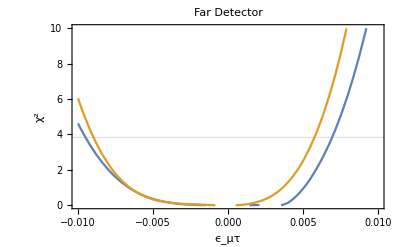

far_detector_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSet[[1+11*j;;11+11*j]]},{j,0,10}];
func=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSet[[1+5+11*j]]},{j,0,10}]
funcNo=Interpolation@%
Plot[{func[del],funcNo[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_s23.pdf",%]
```

```mathematica
-
```

-Graphics-

far_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

{{-0.01,5.23739},{-0.008,2.0201},{-0.006,0.592847},{-0.004,0.109511},{-0.002,0.0283113},{0.,0},{0.002,0.147709},{0.004,0.925065},{0.006,3.10214},{0.008,7.7212},{0.01,15.5847}}

InterpolatingFunction[…]

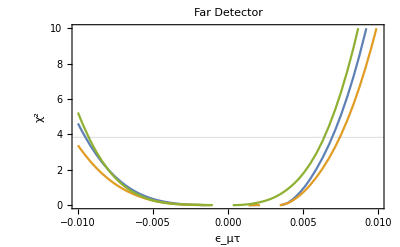

far_detector_bg_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSetbg[[1+11*j;;11+11*j]]},{j,0,10}];
funcbg=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSetbg[[1+5+11*j]]},{j,0,10}]
funcNobg=Interpolation@%
Plot[{func[del],funcbg[del],funcNobg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg_s23.pdf",%]
```

```mathematica
-
```

-Graphics-

far_detector_bg.pdf

## All data sets - near - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

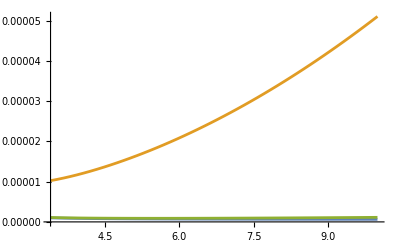

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0147204},{0.875,0.0260777},{1.375,0.0360527},{1.875,0.0390462},{2.375,0.0338369},{2.875,0.024409},{3.375,0.0155661},{3.875,0.00949552},{4.375,0.00599982},{4.875,0.00411114},{5.375,0.00304627},{5.875,0.00237553},{6.375,0.00190277},{6.875,0.00154347},{7.375,0.00125909},{7.875,0.00102934},{8.375,0.000841759},{8.875,0.000687729},{9.375,0.000560885},{9.875,0.000456318},{10.375,0.000370137},{10.875,0.000299201},{11.375,0.000240935},{11.875,0.00019321},{12.375,0.000154249},{12.875,0.000122567},{13.375,0.000096912},{13.875,0.0000762349},{14.375,0.0000596519},{14.875,0.0000464216},{15.375,0.0000359236},{15.875,0.0000276406},{16.375,0.0000211431},{16.875,0.0000160765},{17.375,0.0000121497},{17.875,9.12525×10^-6},{18.375,6.81045×10^-6},{18.875,5.0502×10^-6},{19.375,3.7204×10^-6},{19.875,2.72248×10^-6}}

8

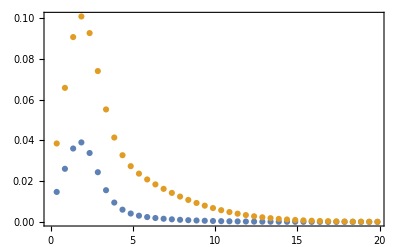

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{11.1479,8.84869,6.8102,5.03442,3.5239,2.28183,1.312,0.617614,0.196212,0.0217462,0,0.0212508,0.194041,0.61324,1.30531,2.27282,3.5126,5.02087,6.79442,8.83071,11.1278}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.74897,1.23366,0.843499,0.562264,0.37251,0.227583,0.116019,0.0503745,0.0161977,0.00218803,0,0.00216151,0.0160969,0.050137,0.115557,0.226791,0.371816,0.561059,0.841652,1.23104,1.74546}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00216276},{0.875,0.00358207},{1.375,0.00500607},{1.875,0.00589802},{2.375,0.00596281},{2.875,0.00533601},{3.375,0.00438793},{3.875,0.00343758},{4.375,0.00263986},{4.875,0.00202392},{5.375,0.00156351},{5.875,0.00122096},{6.375,0.000963902},{6.875,0.000768375},{7.375,0.000617468},{7.875,0.000499368},{8.375,0.000405776},{8.875,0.000330789},{9.375,0.000270159},{9.875,0.00022078},{10.375,0.000180348},{10.875,0.000147123},{11.375,0.000119767},{11.875,0.0000972299},{12.375,0.0000786762},{12.875,0.0000634269},{13.375,0.0000509245},{13.875,0.0000407063},{14.375,0.0000323856},{14.875,0.0000256379},{15.375,0.0000201904},{15.875,0.000015814},{16.375,0.0000123159},{16.875,9.53518×10^-6},{17.375,7.33725×10^-6},{17.875,5.61032×10^-6},{18.375,4.26189×10^-6},{18.875,3.21583×10^-6},{19.375,2.40976×10^-6},{19.875,1.79295×10^-6}}

12

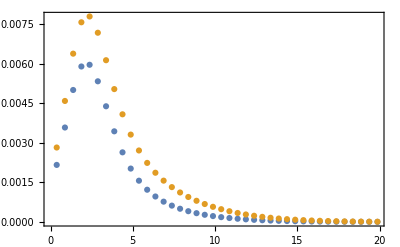

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.31184,3.4437,2.67116,1.99474,1.41512,0.933288,0.550614,0.268931,0.0899668,0.0105977,0,0.0103929,0.0891785,0.267472,0.548486,0.930505,1.41169,1.99067,2.66647,3.43838,4.3059}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.561222,0.424147,0.299338,0.203442,0.131923,0.0804105,0.044835,0.0215962,0.00774022,0.00115391,0,0.00114162,0.00770286,0.0215241,0.0447137,0.0802213,0.131645,0.203049,0.298806,0.423448,0.560571}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}}

11

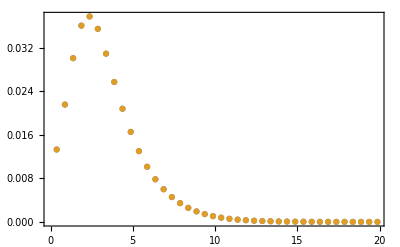

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{27.527,21.9654,17.0176,12.6872,8.97889,5.8994,3.45828,1.66852,0.542882,0.0592865,0,0.0579531,0.537548,1.65859,3.44379,5.88045,8.95556,12.6596,16.9857,21.9292,27.4865}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{4.12745,2.89422,1.94958,1.25152,0.76404,0.445111,0.215526,0.111887,0.0365286,0.00416518,0,0.0041015,0.0362338,0.111692,0.214663,0.444055,0.761521,1.24816,1.94504,2.88812,4.1194}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.1,-0.15,-0.2,-0.2,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0001},{-0.00009},{-0.00008},{-0.00007},{-0.00006},{-0.00005},{-0.00004},{-0.00003},{-0.00002},{-0.00001},{0.},{0.00001},{0.00002},{0.00003},{0.00004},{0.00005},{0.00006},{0.00007},{0.00008},{0.00009},{0.0001}}

```mathematica
dataSet1
dataSet1bg
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

```mathematica
dataSet2
dataSet2bg
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

```mathematica
dataSet3
dataSet3bg
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

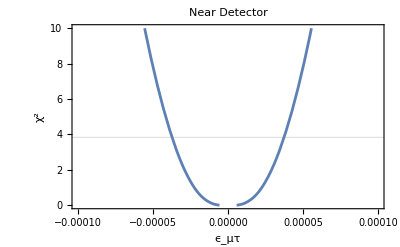

near_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

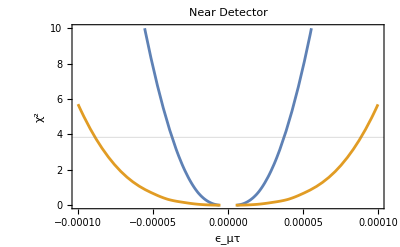

near_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg.pdf",%]
```

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## All data sets - near - NSI - s23

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0147204},{0.875,0.0260777},{1.375,0.0360527},{1.875,0.0390462},{2.375,0.0338369},{2.875,0.024409},{3.375,0.0155661},{3.875,0.00949552},{4.375,0.00599982},{4.875,0.00411114},{5.375,0.00304627},{5.875,0.00237553},{6.375,0.00190277},{6.875,0.00154347},{7.375,0.00125909},{7.875,0.00102934},{8.375,0.000841759},{8.875,0.000687729},{9.375,0.000560885},{9.875,0.000456318},{10.375,0.000370137},{10.875,0.000299201},{11.375,0.000240935},{11.875,0.00019321},{12.375,0.000154249},{12.875,0.000122567},{13.375,0.000096912},{13.875,0.0000762349},{14.375,0.0000596519},{14.875,0.0000464216},{15.375,0.0000359236},{15.875,0.0000276406},{16.375,0.0000211431},{16.875,0.0000160765},{17.375,0.0000121497},{17.875,9.12525×10^-6},{18.375,6.81045×10^-6},{18.875,5.0502×10^-6},{19.375,3.7204×10^-6},{19.875,2.72248×10^-6}}

82

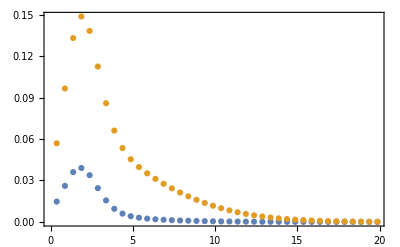

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{11.1603,11.1607,11.1596,11.1571,11.1532,11.1479,11.1412,11.1331,11.1236,11.1126,11.1003,6.8222,6.82256,6.82153,6.81913,6.81535,6.8102,6.80367,6.79577,6.7865,6.77586,6.76385,3.53521,3.53556,3.53461,3.53235,3.52877,3.5239,3.51771,3.51023,3.50144,3.49136,3.47998,1.32185,1.32218,1.32136,1.31939,1.31627,1.312,1.3066,1.30006,1.29239,1.2836,1.27368,0.202266,0.20248,0.201976,0.200758,0.198833,0.196212,0.192912,0.188953,0.184362,0.179169,0.173414,0.000170383,0.000183065,0.000155615,0.0000976173,0.0000328424,0,0.0000540246,0.000267971,0.000735669,0.00157535,0.00293459,0.19997,0.200202,0.19972,0.198527,0.19663,0.194041,0.190775,0.186854,0.182303,0.177155,0.171446,1.31484,1.31523,1.31447,1.31256,1.3095,1.30531,1.29997,1.29349,1.28589,1.27715,1.2673,3.52338,3.52384,3.52299,3.52084,3.51737,3.5126,3.50652,3.49913,3.49044,3.48045,3.46916,6.80569,6.80619,6.80532,6.80306,6.79943,6.79442,6.78804,6.78028,6.77114,6.76063,6.74874,11.1392,11.1398,11.1389,11.1366,11.1329,11.1278,11.1212,11.1133,11.1039,11.0932,11.081}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.56599,9.56629,9.56537,9.56324,9.55991,9.55536,9.54961,9.54265,9.53449,9.52512,9.51456,5.8476,5.8479,5.84703,5.84497,5.84173,5.83731,5.83172,5.82495,5.817,5.80788,5.79759,3.03018,3.03048,3.02967,3.02772,3.02466,3.02048,3.01518,3.00877,3.00124,2.99259,2.98284,1.13302,1.1333,1.13259,1.1309,1.12823,1.12457,1.11994,1.11434,1.10776,1.10023,1.09173,0.173371,0.173554,0.173122,0.172078,0.170428,0.168182,0.165353,0.16196,0.158025,0.153574,0.14864,0.000146043,0.000156913,0.000133384,0.000083672,0.0000281506,0,0.0000463068,0.000229689,0.000630574,0.0013503,0.00251536,0.171403,0.171602,0.171188,0.170166,0.16854,0.166321,0.163522,0.160161,0.15626,0.151847,0.146954,1.127,1.12734,1.12669,1.12505,1.12243,1.11883,1.11426,1.10871,1.10219,1.0947,1.08626,3.02004,3.02044,3.01971,3.01786,3.01489,3.0108,3.00559,2.99926,2.99181,2.98325,2.97357,5.83345,5.83388,5.83313,5.8312,5.82809,5.82379,5.81832,5.81167,5.80383,5.79482,5.78464,9.5479,9.54836,9.54761,9.54564,9.54247,9.53808,9.53248,9.52568,9.51766,9.50843,9.498}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
dataGen//Length
```

121

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.75055,1.75059,1.75046,1.75014,1.74964,1.74897,1.74811,1.74708,1.74587,1.74448,1.74291,0.844432,0.844459,0.844379,0.844193,0.843899,0.843499,0.842993,0.842381,0.841663,0.840842,0.839916,0.372849,0.37286,0.372831,0.372763,0.372656,0.37251,0.372326,0.372103,0.371844,0.371548,0.371215,0.116486,0.116501,0.116462,0.116369,0.116221,0.116019,0.115763,0.115454,0.115093,0.11468,0.114215,0.0163603,0.016366,0.0163525,0.0163198,0.0162681,0.0161977,0.016109,0.0160025,0.0158787,0.0157385,0.0155825,2.09626×10^-6,2.25318×10^-6,1.91365×10^-6,1.19789×10^-6,4.01651×10^-7,0,6.53683×10^-7,3.21862×10^-6,8.75922×10^-6,0.0000185665,0.0000341835,0.016256,0.0162622,0.0162493,0.0162173,0.0161664,0.0160969,0.0160092,0.0159037,0.015781,0.015642,0.0154872,0.116008,0.116027,0.115991,0.1159,0.115756,0.115557,0.115305,0.115,0.114642,0.114233,0.113772,0.372137,0.372151,0.372125,0.372061,0.371958,0.371816,0.371636,0.371418,0.371163,0.370871,0.370544,0.842525,0.842564,0.842496,0.842321,0.84204,0.841652,0.841158,0.840558,0.839853,0.839044,0.83813,1.74692,1.74699,1.74687,1.74658,1.74611,1.74546,1.74463,1.74362,1.74243,1.74107,1.73952}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.50618,1.50622,1.5061,1.50583,1.50541,1.50483,1.5041,1.50321,1.50217,1.50098,1.49964,0.729513,0.729536,0.729468,0.729308,0.729056,0.728713,0.728279,0.727755,0.72714,0.726436,0.725642,0.325299,0.325308,0.325284,0.325225,0.325134,0.325009,0.324851,0.32466,0.324438,0.324184,0.323899,0.0998451,0.0998584,0.0998249,0.0997446,0.0996178,0.0994447,0.0992255,0.0989608,0.098651,0.0982968,0.0978986,0.0140231,0.014028,0.0140164,0.0139884,0.0139441,0.0138837,0.0138077,0.0137164,0.0136104,0.0134901,0.0133564,1.7968×10^-6,1.93129×10^-6,1.64027×10^-6,1.02676×10^-6,3.44272×10^-7,0,5.603×10^-7,2.75881×10^-6,7.50791×10^-6,0.0000159141,0.0000293001,0.0139337,0.0139391,0.013928,0.0139005,0.0138569,0.0137973,0.0137221,0.0136317,0.0135266,0.0134074,0.0132748,0.0994355,0.0994513,0.0994204,0.099343,0.0992191,0.099049,0.0988329,0.0985714,0.0982649,0.0979139,0.0975191,0.324689,0.324701,0.324679,0.324624,0.324535,0.324414,0.324259,0.324073,0.323854,0.323604,0.323323,0.727878,0.727912,0.727854,0.727704,0.727463,0.72713,0.726707,0.726193,0.725589,0.724895,0.724112,1.50307,1.50313,1.50303,1.50278,1.50238,1.50182,1.50111,1.50025,1.49923,1.49806,1.49673}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

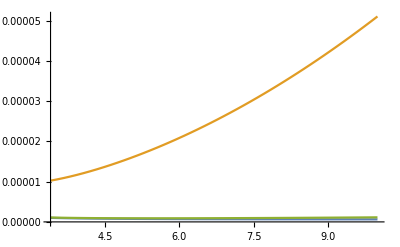

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00216276},{0.875,0.00358207},{1.375,0.00500607},{1.875,0.00589802},{2.375,0.00596281},{2.875,0.00533601},{3.375,0.00438793},{3.875,0.00343758},{4.375,0.00263986},{4.875,0.00202392},{5.375,0.00156351},{5.875,0.00122096},{6.375,0.000963902},{6.875,0.000768375},{7.375,0.000617468},{7.875,0.000499368},{8.375,0.000405776},{8.875,0.000330789},{9.375,0.000270159},{9.875,0.00022078},{10.375,0.000180348},{10.875,0.000147123},{11.375,0.000119767},{11.875,0.0000972299},{12.375,0.0000786762},{12.875,0.0000634269},{13.375,0.0000509245},{13.875,0.0000407063},{14.375,0.0000323856},{14.875,0.0000256379},{15.375,0.0000201904},{15.875,0.000015814},{16.375,0.0000123159},{16.875,9.53518×10^-6},{17.375,7.33725×10^-6},{17.875,5.61032×10^-6},{18.375,4.26189×10^-6},{18.875,3.21583×10^-6},{19.375,2.40976×10^-6},{19.875,1.79295×10^-6}}

6

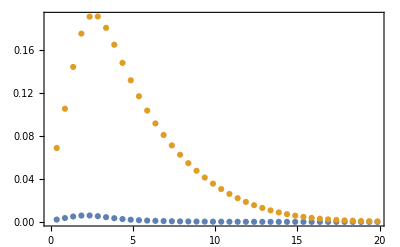

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.31455,4.31463,4.3144,4.31385,4.313,4.31184,4.31037,4.30859,4.30651,4.30412,4.30142,2.67382,2.6739,2.67367,2.67314,2.6723,2.67116,2.66972,2.66797,2.66592,2.66356,2.66091,1.41768,1.41776,1.41754,1.41703,1.41622,1.41512,1.41372,1.41203,1.41004,1.40776,1.40518,0.552959,0.553037,0.552841,0.552372,0.551629,0.550614,0.549326,0.547766,0.545934,0.543832,0.54146,0.0916428,0.0917017,0.0915629,0.0912268,0.0906943,0.0899668,0.0890464,0.0879353,0.0866367,0.0851541,0.0834919,0.0000365421,0.0000392621,0.0000333747,0.000020936,7.04371×10^-6,0,0.0000115867,0.0000574718,0.000157779,0.000337865,0.000629381,0.0908235,0.0908876,0.0907545,0.0904246,0.0898988,0.0891785,0.0882656,0.0871625,0.0858722,0.0843985,0.0827454,0.550757,0.550849,0.550669,0.550214,0.549486,0.548486,0.547212,0.545667,0.54385,0.541761,0.539402,1.41413,1.41423,1.41404,1.41356,1.41277,1.41169,1.41032,1.40865,1.40668,1.40442,1.40186,2.66896,2.66907,2.66888,2.66838,2.66758,2.66647,2.66506,2.66334,2.66132,2.65899,2.65636,4.30841,4.30852,4.30833,4.30783,4.30702,4.3059,4.30447,4.30273,4.30068,4.29832,4.29566}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.69819,3.69825,3.69805,3.69759,3.69686,3.69586,3.6946,3.69308,3.69129,3.68924,3.68693,2.29184,2.29191,2.29172,2.29126,2.29055,2.28957,2.28833,2.28683,2.28507,2.28305,2.28078,1.21515,1.21522,1.21504,1.2146,1.2139,1.21296,1.21176,1.21031,1.20861,1.20665,1.20444,0.473965,0.474032,0.473864,0.473461,0.472825,0.471954,0.470851,0.469513,0.467944,0.466142,0.464109,0.078551,0.0786015,0.0784825,0.0781944,0.077738,0.0771144,0.0763255,0.0753731,0.07426,0.0729892,0.0715645,0.0000313218,0.0000336532,0.0000286069,0.0000179452,6.03747×10^-6,0,9.93145×10^-6,0.0000492616,0.000135239,0.000289598,0.00053947,0.0778487,0.0779037,0.0777896,0.0775068,0.0770561,0.0764388,0.0756563,0.0747107,0.0736048,0.0723415,0.0709246,0.472077,0.472157,0.472002,0.471612,0.470988,0.470131,0.469039,0.467715,0.466157,0.464367,0.462345,1.21211,1.2122,1.21204,1.21162,1.21095,1.21002,1.20884,1.20741,1.20572,1.20379,1.2016,2.28768,2.28778,2.28761,2.28718,2.2865,2.28554,2.28433,2.28286,2.28113,2.27913,2.27688,3.69292,3.69302,3.69285,3.69242,3.69173,3.69077,3.68954,3.68805,3.6863,3.68428,3.68199}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.561415,0.56142,0.561404,0.561365,0.561305,0.561222,0.561118,0.560992,0.560844,0.560674,0.560483,0.299559,0.299566,0.299547,0.299503,0.299433,0.299338,0.299218,0.299073,0.298902,0.298707,0.298486,0.132067,0.132072,0.13206,0.132031,0.131985,0.131923,0.131845,0.13175,0.131638,0.131511,0.131366,0.0449183,0.0449211,0.0449141,0.0448974,0.0448711,0.044835,0.0447893,0.044734,0.0446691,0.0445947,0.0445108,0.00778278,0.00778428,0.00778076,0.00777223,0.00775871,0.00774022,0.00771679,0.00768846,0.00765527,0.00761727,0.00757453,5.30369×10^-7,5.69905×10^-7,4.84335×10^-7,3.03655×10^-7,1.0207×10^-7,0,1.67435×10^-7,8.28915×10^-7,2.27051×10^-6,4.84928×10^-6,9.00648×10^-6,0.00774466,0.00774628,0.00774291,0.00773453,0.00772117,0.00770286,0.0076796,0.00765146,0.00761845,0.00758065,0.0075381,0.0447943,0.0447975,0.0447911,0.044775,0.0447492,0.0447137,0.0446685,0.0446138,0.0445495,0.0444757,0.0443924,0.131781,0.131787,0.131777,0.131749,0.131705,0.131645,0.131567,0.131474,0.131364,0.131237,0.131094,0.299013,0.299022,0.299006,0.298965,0.298898,0.298806,0.298688,0.298546,0.298378,0.298185,0.297967,0.560749,0.560757,0.560744,0.560708,0.560651,0.560571,0.56047,0.560347,0.560202,0.560035,0.559847}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.486927,0.486932,0.486917,0.486884,0.486833,0.486762,0.486672,0.486564,0.486438,0.486292,0.486128,0.256765,0.256771,0.256755,0.256717,0.256657,0.256576,0.256473,0.256348,0.256202,0.256034,0.255845,0.1132,0.113204,0.113194,0.113169,0.11313,0.113077,0.11301,0.112929,0.112833,0.112723,0.1126,0.0385014,0.0385038,0.0384978,0.0384835,0.0384609,0.03843,0.0383908,0.0383434,0.0382878,0.038224,0.0381521,0.00667096,0.00667224,0.00666922,0.00666191,0.00665032,0.00663448,0.00661439,0.00659011,0.00656166,0.00652909,0.00649245,4.54602×10^-7,4.8849×10^-7,4.15144×10^-7,2.60275×10^-7,8.74884×10^-8,0,1.43515×10^-7,7.10499×10^-7,1.94615×10^-6,4.15652×10^-6,7.71984×10^-6,0.00663828,0.00663967,0.00663678,0.0066296,0.00661815,0.00660245,0.00658252,0.00655839,0.0065301,0.0064977,0.00646123,0.0383951,0.0383979,0.0383924,0.0383786,0.0383564,0.038326,0.0382873,0.0382404,0.0381853,0.038122,0.0380506,0.112956,0.112961,0.112951,0.112928,0.11289,0.112838,0.112772,0.112692,0.112597,0.112489,0.112366,0.256297,0.256305,0.256291,0.256255,0.256198,0.256119,0.256019,0.255896,0.255753,0.255587,0.2554,0.486356,0.486363,0.486352,0.486321,0.486272,0.486204,0.486117,0.486012,0.485887,0.485744,0.485583}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0114112},{0.875,0.018499},{1.375,0.0258157},{1.875,0.0309513},{2.375,0.0323938},{2.875,0.0304416},{3.375,0.0265293},{3.875,0.0220571},{4.375,0.0178419},{4.875,0.0141947},{5.375,0.0111635},{5.875,0.0086971},{6.375,0.00671806},{6.875,0.00514785},{7.375,0.0039148},{7.875,0.00295601},{8.375,0.00221746},{8.875,0.00165361},{9.375,0.00122669},{9.875,0.000905886},{10.375,0.000666465},{10.875,0.000488861},{11.375,0.000357802},{11.875,0.000261515},{12.375,0.000191023},{12.875,0.00013955},{13.375,0.000102028},{13.875,0.0000746953},{14.375,0.0000547821},{14.875,0.0000402593},{15.375,0.000029649},{15.875,0.0000218788},{16.375,0.0000161728},{16.875,0.0000119702},{17.375,8.86604×10^-6},{17.875,6.56725×10^-6},{18.375,4.86129×10^-6},{18.875,3.59345×10^-6},{19.375,2.65058×10^-6},{19.875,1.94951×10^-6}}

33

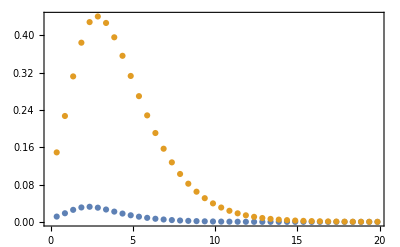

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{23.6102,23.6106,23.6093,23.6061,23.6012,23.5945,23.5861,23.5758,23.5638,23.5501,23.5345,14.6019,14.6023,14.601,14.5979,14.5931,14.5865,14.5782,14.5681,14.5563,14.5427,14.5274,7.71097,7.71143,7.71019,7.70723,7.70256,7.69619,7.68812,7.67834,7.66685,7.65367,7.63879,2.97784,2.9783,2.97716,2.97444,2.97013,2.96424,2.95676,2.94771,2.93709,2.92489,2.91112,0.475144,0.475489,0.474676,0.472708,0.469589,0.465328,0.459933,0.453418,0.4458,0.437097,0.427331,0.000210099,0.000225737,0.000191887,0.000120371,0.0000404978,0,0.0000666175,0.000330433,0.000907149,0.00194254,0.00361861,0.470392,0.470767,0.469987,0.468055,0.464976,0.460755,0.455405,0.448936,0.441366,0.432713,0.422999,2.96499,2.96553,2.96448,2.96184,2.95762,2.95182,2.94443,2.93546,2.92492,2.9128,2.8991,7.69028,7.69088,7.68978,7.68696,7.68243,7.67619,7.66825,7.6586,7.64724,7.63417,7.61941,14.5735,14.5742,14.5731,14.5702,14.5656,14.5592,14.551,14.5411,14.5294,14.516,14.5009,23.5743,23.575,23.5739,23.571,23.5663,23.5599,23.5517,23.5416,23.5298,23.5163,23.5009}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{20.2373,20.2377,20.2365,20.2338,20.2296,20.2239,20.2166,20.2079,20.1976,20.1858,20.1724,12.5159,12.5163,12.5151,12.5125,12.5084,12.5027,12.4956,12.487,12.4768,12.4652,12.4521,6.6094,6.6098,6.60873,6.6062,6.6022,6.59674,6.58981,6.58143,6.57159,6.56029,6.54753,2.55244,2.55282,2.55185,2.54952,2.54582,2.54077,2.53437,2.52661,2.5175,2.50705,2.49525,0.407267,0.407562,0.406865,0.405178,0.402505,0.398852,0.394228,0.388644,0.382114,0.374654,0.366284,0.000180084,0.000193489,0.000164475,0.000103176,0.0000347124,0,0.0000571007,0.000283229,0.000777556,0.00166504,0.00310167,0.403193,0.403514,0.402846,0.40119,0.39855,0.394933,0.390347,0.384802,0.378313,0.370897,0.362571,2.54142,2.54188,2.54098,2.53872,2.5351,2.53013,2.5238,2.51611,2.50707,2.49668,2.48495,6.59167,6.59219,6.59124,6.58882,6.58494,6.57959,6.57278,6.56451,6.55478,6.54358,6.53092,12.4916,12.4922,12.4912,12.4887,12.4848,12.4793,12.4723,12.4638,12.4538,12.4423,12.4293,20.2066,20.2071,20.2062,20.2037,20.1997,20.1942,20.1871,20.1786,20.1684,20.1568,20.1436}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.18458,3.18465,3.18444,3.18394,3.18317,3.18211,3.18077,3.17916,3.17726,3.17509,3.17265,1.52316,1.52321,1.52305,1.52268,1.52208,1.52127,1.52025,1.51902,1.51757,1.5159,1.51403,0.597247,0.597278,0.597195,0.596999,0.59669,0.596269,0.595736,0.595092,0.594338,0.593475,0.592505,0.175163,0.175178,0.17514,0.17505,0.174908,0.174714,0.174468,0.174173,0.173828,0.173435,0.172996,0.0300638,0.0300775,0.0300453,0.0299672,0.0298437,0.0296752,0.0294624,0.0292061,0.0289073,0.0285671,0.028187,3.94438×10^-6,4.23945×10^-6,3.60096×10^-6,2.25466×10^-6,7.56289×10^-7,0,1.23241×10^-6,6.07343×10^-6,0.0000165457,0.0000351134,0.0000647416,0.029824,0.0298389,0.029808,0.0297316,0.0296099,0.0294435,0.0292328,0.0289789,0.0286826,0.0283451,0.0279678,0.174567,0.174585,0.17455,0.174464,0.174325,0.174135,0.173895,0.173604,0.173265,0.172878,0.172444,0.59552,0.59556,0.595487,0.595301,0.595003,0.594592,0.594071,0.593438,0.592696,0.591845,0.590887,1.51907,1.51915,1.51902,1.51866,1.5181,1.51731,1.51632,1.5151,1.51368,1.51204,1.5102,3.17799,3.17809,3.17792,3.17746,3.17673,3.17571,3.17441,3.17283,3.17098,3.16885,3.16644}

{-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.8725,2.87256,2.87238,2.87195,2.87129,2.87038,2.86924,2.86785,2.86623,2.86437,2.86227,1.35699,1.35704,1.3569,1.35658,1.35607,1.35538,1.3545,1.35344,1.3522,1.35078,1.34917,0.534783,0.53481,0.534739,0.534571,0.534306,0.533945,0.533488,0.532936,0.53229,0.53155,0.530718,0.155854,0.155867,0.155835,0.155757,0.155635,0.155469,0.155259,0.155005,0.15471,0.154373,0.153996,0.025769,0.0257807,0.0257531,0.0256862,0.0255803,0.0254359,0.0252535,0.0250338,0.0247777,0.0244861,0.0241602,3.3809×10^-6,3.63381×10^-6,3.08654×10^-6,1.93257×10^-6,6.48247×10^-7,0,1.05635×10^-6,5.20579×10^-6,0.000014182,0.0000300972,0.0000554928,0.0255635,0.0255762,0.0255497,0.0254842,0.0253799,0.0252372,0.0250567,0.024839,0.0245851,0.0242958,0.0239724,0.155343,0.155359,0.155329,0.155255,0.155136,0.154973,0.154767,0.154518,0.154227,0.153895,0.153523,0.533303,0.533337,0.533274,0.533115,0.532859,0.532508,0.53206,0.531518,0.530882,0.530153,0.529332,1.35349,1.35356,1.35344,1.35314,1.35265,1.35198,1.35113,1.35009,1.34887,1.34747,1.34588,2.86684,2.86694,2.86679,2.8664,2.86576,2.86489,2.86378,2.86243,2.86084,2.85901,2.85695}

{-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0001,0.482},{-0.0001,0.502},{-0.0001,0.522},{-0.0001,0.542},{-0.0001,0.562},{-0.0001,0.582},{-0.0001,0.602},{-0.0001,0.622},{-0.0001,0.642},{-0.0001,0.662},{-0.0001,0.682},{-0.00008,0.482},{-0.00008,0.502},{-0.00008,0.522},{-0.00008,0.542},{-0.00008,0.562},{-0.00008,0.582},{-0.00008,0.602},{-0.00008,0.622},{-0.00008,0.642},{-0.00008,0.662},{-0.00008,0.682},{-0.00006,0.482},{-0.00006,0.502},{-0.00006,0.522},{-0.00006,0.542},{-0.00006,0.562},{-0.00006,0.582},{-0.00006,0.602},{-0.00006,0.622},{-0.00006,0.642},{-0.00006,0.662},{-0.00006,0.682},{-0.00004,0.482},{-0.00004,0.502},{-0.00004,0.522},{-0.00004,0.542},{-0.00004,0.562},{-0.00004,0.582},{-0.00004,0.602},{-0.00004,0.622},{-0.00004,0.642},{-0.00004,0.662},{-0.00004,0.682},{-0.00002,0.482},{-0.00002,0.502},{-0.00002,0.522},{-0.00002,0.542},{-0.00002,0.562},{-0.00002,0.582},{-0.00002,0.602},{-0.00002,0.622},{-0.00002,0.642},{-0.00002,0.662},{-0.00002,0.682},{0.,0.482},{0.,0.502},{0.,0.522},{0.,0.542},{0.,0.562},{0.,0.582},{0.,0.602},{0.,0.622},{0.,0.642},{0.,0.662},{0.,0.682},{0.00002,0.482},{0.00002,0.502},{0.00002,0.522},{0.00002,0.542},{0.00002,0.562},{0.00002,0.582},{0.00002,0.602},{0.00002,0.622},{0.00002,0.642},{0.00002,0.662},{0.00002,0.682},{0.00004,0.482},{0.00004,0.502},{0.00004,0.522},{0.00004,0.542},{0.00004,0.562},{0.00004,0.582},{0.00004,0.602},{0.00004,0.622},{0.00004,0.642},{0.00004,0.662},{0.00004,0.682},{0.00006,0.482},{0.00006,0.502},{0.00006,0.522},{0.00006,0.542},{0.00006,0.562},{0.00006,0.582},{0.00006,0.602},{0.00006,0.622},{0.00006,0.642},{0.00006,0.662},{0.00006,0.682},{0.00008,0.482},{0.00008,0.502},{0.00008,0.522},{0.00008,0.542},{0.00008,0.562},{0.00008,0.582},{0.00008,0.602},{0.00008,0.622},{0.00008,0.642},{0.00008,0.662},{0.00008,0.682},{0.0001,0.482},{0.0001,0.502},{0.0001,0.522},{0.0001,0.542},{0.0001,0.562},{0.0001,0.582},{0.0001,0.602},{0.0001,0.622},{0.0001,0.642},{0.0001,0.662},{0.0001,0.682}}

```mathematica
dataSet1
dataSet1bg
```

{9.56599,9.56629,9.56537,9.56324,9.55991,9.55536,9.54961,9.54265,9.53449,9.52512,9.51456,5.8476,5.8479,5.84703,5.84497,5.84173,5.83731,5.83172,5.82495,5.817,5.80788,5.79759,3.03018,3.03048,3.02967,3.02772,3.02466,3.02048,3.01518,3.00877,3.00124,2.99259,2.98284,1.13302,1.1333,1.13259,1.1309,1.12823,1.12457,1.11994,1.11434,1.10776,1.10023,1.09173,0.173371,0.173554,0.173122,0.172078,0.170428,0.168182,0.165353,0.16196,0.158025,0.153574,0.14864,0.000146043,0.000156913,0.000133384,0.000083672,0.0000281506,0,0.0000463068,0.000229689,0.000630574,0.0013503,0.00251536,0.171403,0.171602,0.171188,0.170166,0.16854,0.166321,0.163522,0.160161,0.15626,0.151847,0.146954,1.127,1.12734,1.12669,1.12505,1.12243,1.11883,1.11426,1.10871,1.10219,1.0947,1.08626,3.02004,3.02044,3.01971,3.01786,3.01489,3.0108,3.00559,2.99926,2.99181,2.98325,2.97357,5.83345,5.83388,5.83313,5.8312,5.82809,5.82379,5.81832,5.81167,5.80383,5.79482,5.78464,9.5479,9.54836,9.54761,9.54564,9.54247,9.53808,9.53248,9.52568,9.51766,9.50843,9.498}

{1.50618,1.50622,1.5061,1.50583,1.50541,1.50483,1.5041,1.50321,1.50217,1.50098,1.49964,0.729513,0.729536,0.729468,0.729308,0.729056,0.728713,0.728279,0.727755,0.72714,0.726436,0.725642,0.325299,0.325308,0.325284,0.325225,0.325134,0.325009,0.324851,0.32466,0.324438,0.324184,0.323899,0.0998451,0.0998584,0.0998249,0.0997446,0.0996178,0.0994447,0.0992255,0.0989608,0.098651,0.0982968,0.0978986,0.0140231,0.014028,0.0140164,0.0139884,0.0139441,0.0138837,0.0138077,0.0137164,0.0136104,0.0134901,0.0133564,1.7968×10^-6,1.93129×10^-6,1.64027×10^-6,1.02676×10^-6,3.44272×10^-7,0,5.603×10^-7,2.75881×10^-6,7.50791×10^-6,0.0000159141,0.0000293001,0.0139337,0.0139391,0.013928,0.0139005,0.0138569,0.0137973,0.0137221,0.0136317,0.0135266,0.0134074,0.0132748,0.0994355,0.0994513,0.0994204,0.099343,0.0992191,0.099049,0.0988329,0.0985714,0.0982649,0.0979139,0.0975191,0.324689,0.324701,0.324679,0.324624,0.324535,0.324414,0.324259,0.324073,0.323854,0.323604,0.323323,0.727878,0.727912,0.727854,0.727704,0.727463,0.72713,0.726707,0.726193,0.725589,0.724895,0.724112,1.50307,1.50313,1.50303,1.50278,1.50238,1.50182,1.50111,1.50025,1.49923,1.49806,1.49673}

```mathematica
dataSet2
dataSet2bg
```

{3.69819,3.69825,3.69805,3.69759,3.69686,3.69586,3.6946,3.69308,3.69129,3.68924,3.68693,2.29184,2.29191,2.29172,2.29126,2.29055,2.28957,2.28833,2.28683,2.28507,2.28305,2.28078,1.21515,1.21522,1.21504,1.2146,1.2139,1.21296,1.21176,1.21031,1.20861,1.20665,1.20444,0.473965,0.474032,0.473864,0.473461,0.472825,0.471954,0.470851,0.469513,0.467944,0.466142,0.464109,0.078551,0.0786015,0.0784825,0.0781944,0.077738,0.0771144,0.0763255,0.0753731,0.07426,0.0729892,0.0715645,0.0000313218,0.0000336532,0.0000286069,0.0000179452,6.03747×10^-6,0,9.93145×10^-6,0.0000492616,0.000135239,0.000289598,0.00053947,0.0778487,0.0779037,0.0777896,0.0775068,0.0770561,0.0764388,0.0756563,0.0747107,0.0736048,0.0723415,0.0709246,0.472077,0.472157,0.472002,0.471612,0.470988,0.470131,0.469039,0.467715,0.466157,0.464367,0.462345,1.21211,1.2122,1.21204,1.21162,1.21095,1.21002,1.20884,1.20741,1.20572,1.20379,1.2016,2.28768,2.28778,2.28761,2.28718,2.2865,2.28554,2.28433,2.28286,2.28113,2.27913,2.27688,3.69292,3.69302,3.69285,3.69242,3.69173,3.69077,3.68954,3.68805,3.6863,3.68428,3.68199}

{0.486927,0.486932,0.486917,0.486884,0.486833,0.486762,0.486672,0.486564,0.486438,0.486292,0.486128,0.256765,0.256771,0.256755,0.256717,0.256657,0.256576,0.256473,0.256348,0.256202,0.256034,0.255845,0.1132,0.113204,0.113194,0.113169,0.11313,0.113077,0.11301,0.112929,0.112833,0.112723,0.1126,0.0385014,0.0385038,0.0384978,0.0384835,0.0384609,0.03843,0.0383908,0.0383434,0.0382878,0.038224,0.0381521,0.00667096,0.00667224,0.00666922,0.00666191,0.00665032,0.00663448,0.00661439,0.00659011,0.00656166,0.00652909,0.00649245,4.54602×10^-7,4.8849×10^-7,4.15144×10^-7,2.60275×10^-7,8.74884×10^-8,0,1.43515×10^-7,7.10499×10^-7,1.94615×10^-6,4.15652×10^-6,7.71984×10^-6,0.00663828,0.00663967,0.00663678,0.0066296,0.00661815,0.00660245,0.00658252,0.00655839,0.0065301,0.0064977,0.00646123,0.0383951,0.0383979,0.0383924,0.0383786,0.0383564,0.038326,0.0382873,0.0382404,0.0381853,0.038122,0.0380506,0.112956,0.112961,0.112951,0.112928,0.11289,0.112838,0.112772,0.112692,0.112597,0.112489,0.112366,0.256297,0.256305,0.256291,0.256255,0.256198,0.256119,0.256019,0.255896,0.255753,0.255587,0.2554,0.486356,0.486363,0.486352,0.486321,0.486272,0.486204,0.486117,0.486012,0.485887,0.485744,0.485583}

```mathematica
dataSet3
dataSet3bg
```

{20.2373,20.2377,20.2365,20.2338,20.2296,20.2239,20.2166,20.2079,20.1976,20.1858,20.1724,12.5159,12.5163,12.5151,12.5125,12.5084,12.5027,12.4956,12.487,12.4768,12.4652,12.4521,6.6094,6.6098,6.60873,6.6062,6.6022,6.59674,6.58981,6.58143,6.57159,6.56029,6.54753,2.55244,2.55282,2.55185,2.54952,2.54582,2.54077,2.53437,2.52661,2.5175,2.50705,2.49525,0.407267,0.407562,0.406865,0.405178,0.402505,0.398852,0.394228,0.388644,0.382114,0.374654,0.366284,0.000180084,0.000193489,0.000164475,0.000103176,0.0000347124,0,0.0000571007,0.000283229,0.000777556,0.00166504,0.00310167,0.403193,0.403514,0.402846,0.40119,0.39855,0.394933,0.390347,0.384802,0.378313,0.370897,0.362571,2.54142,2.54188,2.54098,2.53872,2.5351,2.53013,2.5238,2.51611,2.50707,2.49668,2.48495,6.59167,6.59219,6.59124,6.58882,6.58494,6.57959,6.57278,6.56451,6.55478,6.54358,6.53092,12.4916,12.4922,12.4912,12.4887,12.4848,12.4793,12.4723,12.4638,12.4538,12.4423,12.4293,20.2066,20.2071,20.2062,20.2037,20.1997,20.1942,20.1871,20.1786,20.1684,20.1568,20.1436}

{2.8725,2.87256,2.87238,2.87195,2.87129,2.87038,2.86924,2.86785,2.86623,2.86437,2.86227,1.35699,1.35704,1.3569,1.35658,1.35607,1.35538,1.3545,1.35344,1.3522,1.35078,1.34917,0.534783,0.53481,0.534739,0.534571,0.534306,0.533945,0.533488,0.532936,0.53229,0.53155,0.530718,0.155854,0.155867,0.155835,0.155757,0.155635,0.155469,0.155259,0.155005,0.15471,0.154373,0.153996,0.025769,0.0257807,0.0257531,0.0256862,0.0255803,0.0254359,0.0252535,0.0250338,0.0247777,0.0244861,0.0241602,3.3809×10^-6,3.63381×10^-6,3.08654×10^-6,1.93257×10^-6,6.48247×10^-7,0,1.05635×10^-6,5.20579×10^-6,0.000014182,0.0000300972,0.0000554928,0.0255635,0.0255762,0.0255497,0.0254842,0.0253799,0.0252372,0.0250567,0.024839,0.0245851,0.0242958,0.0239724,0.155343,0.155359,0.155329,0.155255,0.155136,0.154973,0.154767,0.154518,0.154227,0.153895,0.153523,0.533303,0.533337,0.533274,0.533115,0.532859,0.532508,0.53206,0.531518,0.530882,0.530153,0.529332,1.35349,1.35356,1.35344,1.35314,1.35265,1.35198,1.35113,1.35009,1.34887,1.34747,1.34588,2.86684,2.86694,2.86679,2.8664,2.86576,2.86489,2.86378,2.86243,2.86084,2.85901,2.85695}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

```mathematica
dataSet//Length
```

121

InterpolatingFunction[…]

{{-0.0001,33.4751},{-0.00008,20.6296},{-0.00006,10.8302},{-0.00004,4.1373},{-0.00002,0.644148},{0.,0},{0.00002,0.637693},{0.00004,4.11909},{0.00006,10.8004},{0.00008,20.5886},{0.0001,33.423}}

InterpolatingFunction[…]

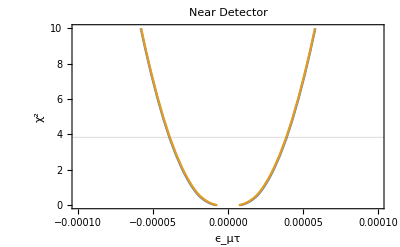

near_detector_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSet[[1+11*j;;11+11*j]]},{j,0,10}];
func=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSet[[1+5+11*j]]},{j,0,10}]
funcNo=Interpolation@%
Plot[{func[del],funcNo[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_s23.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

{{-0.0001,4.86197},{-0.00008,2.34067},{-0.00006,0.972031},{-0.00004,0.293343},{-0.00002,0.0459541},{0.,0},{0.00002,0.045637},{0.00004,0.292348},{0.00006,0.96976},{0.00008,2.33523},{0.0001,4.85292}}

InterpolatingFunction[…]

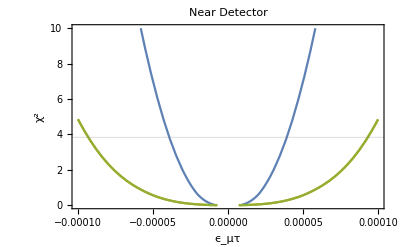

near_detector_bg_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSetbg[[1+11*j;;11+11*j]]},{j,0,10}];
funcbg=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSetbg[[1+5+11*j]]},{j,0,10}]
funcNobg=Interpolation@%
Plot[{func[del],funcbg[del],funcNobg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg_s23.pdf",%]
```

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## All data sets - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+258.28535887642835 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-183974.99993755788 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-258.2853588764284 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+188290.0266209162 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6813.888886576221 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13947.409379327133 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+2820.716419141173 ee epS^2 Sin[8.257817015055423/ee]-45.374457454257865 s23^2 Sin[8.257817015055423/ee]+15.915941137654993 ee s23^2 Sin[8.257817015055423/ee]-0.7015930129722432 ee^2 s23^2 Sin[8.257817015055423/ee]+33077.97948415399 epS^2 s23^2 Sin[8.257817015055423/ee]-14423.437508491661 ee epS^2 s23^2 Sin[8.257817015055423/ee]+511.4613064567654 ee^2 epS^2 s23^2 Sin[8.257817015055423/ee]+45.374457454257865 s23^4 Sin[8.257817015055423/ee]-15.915941137654993 ee s23^4 Sin[8.257817015055423/ee]+0.7015930129722432 ee^2 s23^4 Sin[8.257817015055423/ee]-33077.97948415399 epS^2 s23^4 Sin[8.257817015055423/ee]+11602.721089350489 ee epS^2 s23^4 Sin[8.257817015055423/ee]-511.4613064567654 ee^2 epS^2 s23^4 Sin[8.257817015055423/ee]+1225.1103512649627 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-534.2013892033949 ee epS s23 √(1-s23^2) Sin[8.257817015055423/ee]+18.943011350250572 ee^2 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-2450.2207025299253 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+859.4608214333696 ee epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]-37.886022700501144 ee^2 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+Cos[δ] (ee s23 (192.51017821519827 epS^2 s23^2 √(1-s23^2)-0.2640743185393668 √(1-s23^2) (-0.4999999999999998+1. s23^2)+epS (10.695009900844333 s23-14.260013201125792 s23^3))+s23 (-2231.3075159546443 epS^2 s23^2 √(1-s23^2)+3.0607784855344917 √(1-s23^2) (-0.5+1. s23^2)+epS (-123.96152866414695 s23+165.28203821886257 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-4.112800865144252+8.225601730288504 s23^2+ee (0.35483949292116995-0.7096789858423399 s23^2))+epS^2 s23 √(1-s23^2) (5996.4636613803195-5996.4636613803195 s23^2+ee (-517.3559806790659+517.3559806790659 s23^2))+epS (111.04562335889482-555.228116794474 s23^2+444.18249343557926 s23^4+ee (-9.580666308871589+47.90333154435795 s23^2-38.322665235486355 s23^4))) Sin[8.257817015055423/ee])+111.04562335889482 epS s23^2 Sin[δ]-9.580666308871589 ee epS s23^2 Sin[δ]+4.112800865144252 s23 √(1-s23^2) Sin[δ]-0.35483949292116995 ee s23 √(1-s23^2) Sin[δ]+41.32050955471564 epS Sin[8.257817015055423/ee] Sin[δ]-3.5650033002814494 ee epS Sin[8.257817015055423/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[8.257817015055423/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[8.257817015055423/ee] Sin[δ]-41.3205095547155 epS s23^2 Sin[8.257817015055423/ee] Sin[δ]+3.565003300281454 ee epS s23^2 Sin[8.257817015055423/ee] Sin[δ]-1.5303892427672459 s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+0.13203715926968335 ee s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+Cos[8.257817015055423/ee] (ee (epS^2 (3265.427102368374+(185024.59951854794-33798.17512428063 ee+1458. ee^2) s23^2+(-188290.02662091632+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-258.28535887642835+258.2853588764283 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6852.762945131406-13947.409379327137 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (1.5303892427672459-3.060778485534495 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2)+ee (-0.13203715926968337+0.26407431853936664 s23^2))+epS^2 s23 √(1-s23^2) (-2231.307515954646+2231.307515954644 s23^2+ee (192.51017821519812-192.5101782151981 s23^2)+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-41.32050955471564+206.60254777357818 s23^2-165.28203821886265 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4)+ee (3.565003300281445-17.825016501407262 s23^2+14.260013201125783 s23^4))) Cos[δ]+(0.35483949292116995 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (111.04562335889482-111.04562335889473 s23^2+ee (-9.580666308871589+9.580666308871589 s23^2))) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.3417952825623436+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.341795282562344-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.572,3.44,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

9

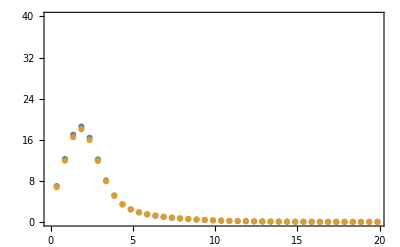

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data events

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataGen
```

{{{0.375,7.62783},{0.875,13.046},{1.375,18.0081},{1.875,20.0505},{2.375,18.4551},{2.875,14.7422},{3.375,10.956},{3.875,8.15737},{4.375,6.38537},{4.875,5.28644},{5.375,4.54162},{5.875,3.96883},{6.375,3.48527},{6.875,3.0576},{7.375,2.67275},{7.875,2.32516},{8.375,2.01186},{8.875,1.73077},{9.375,1.48005},{9.875,1.25787},{10.375,1.06232},{10.875,0.891445},{11.375,0.743213},{11.875,0.615574},{12.375,0.506485},{12.875,0.413951},{13.375,0.336051},{13.875,0.270967},{14.375,0.217003},{14.875,0.172597},{15.375,0.136334},{15.875,0.106944},{16.375,0.0833049},{16.875,0.0644358},{17.375,0.0494881},{17.875,0.0377368},{18.375,0.0285686},{18.875,0.0214704},{19.375,0.0160171},{19.875,0.0118599}},{{0.375,7.38123},{0.875,12.6828},{1.375,17.5164},{1.875,19.4452},{2.375,17.7766},{2.875,14.0384},{3.375,10.2632},{3.875,7.4943},{4.375,5.75908},{4.875,4.69964},{5.375,3.99618},{5.875,3.46635},{6.375,3.02676},{6.875,2.64314},{7.375,2.30153},{7.875,1.99557},{8.375,1.72171},{8.875,1.47742},{9.375,1.26058},{9.875,1.06922},{10.375,0.9014},{10.875,0.755208},{11.375,0.628728},{11.875,0.520076},{12.375,0.427408},{12.875,0.348947},{13.375,0.283002},{13.875,0.227987},{14.375,0.182432},{14.875,0.14499},{15.375,0.114446},{15.875,0.0897163},{16.375,0.0698434},{16.875,0.0539933},{17.375,0.0414466},{17.875,0.0315896},{18.375,0.0239042},{18.875,0.0179575},{19.375,0.0133913},{19.875,0.00991208}},{{0.375,7.17473},{0.875,12.3828},{1.375,17.1109},{1.875,18.9414},{2.375,17.2028},{2.875,13.4333},{3.375,9.65953},{3.875,6.91132},{4.375,5.2055},{4.875,4.17941},{5.375,3.51178},{5.875,3.01964},{6.375,2.61882},{6.875,2.27419},{7.375,1.97093},{7.875,1.70195},{8.375,1.46314},{8.875,1.25158},{9.375,1.0649},{9.875,0.900992},{10.375,0.757878},{10.875,0.633682},{11.375,0.526594},{11.875,0.434871},{12.375,0.356846},{12.875,0.290937},{13.375,0.235658},{13.875,0.189627},{14.375,0.151574},{14.875,0.120346},{15.375,0.0949077},{15.875,0.0743369},{16.375,0.0578254},{16.875,0.0446701},{17.375,0.0342667},{17.875,0.0261009},{18.375,0.0197394},{18.875,0.0148208},{19.375,0.0110466},{19.875,0.00817274}},{{0.375,7.00834},{0.875,12.1459},{1.375,16.7917},{1.875,18.539},{2.375,16.7337},{2.875,12.9269},{3.375,9.145},{3.875,6.40843},{4.375,4.72461},{4.875,3.72573},{5.375,3.08843},{5.875,2.62868},{6.375,2.26147},{6.875,1.95077},{7.375,1.68095},{7.875,1.44429},{8.375,1.23615},{8.875,1.05327},{9.375,0.893026},{9.875,0.753191},{10.375,0.631755},{10.875,0.52687},{11.375,0.436811},{11.875,0.359959},{12.375,0.294801},{12.875,0.239923},{13.375,0.194018},{13.875,0.155885},{14.375,0.12443},{14.875,0.098667},{15.375,0.0777178},{15.875,0.0608053},{16.375,0.0472506},{16.875,0.0364661},{17.375,0.0279485},{17.875,0.0212707},{18.375,0.016074},{18.875,0.01206},{19.375,0.00898291},{19.875,0.00664182}},{{0.375,6.88205},{0.875,11.9722},{1.375,16.5587},{1.875,18.238},{2.375,16.3691},{2.875,12.5191},{3.375,8.7196},{3.875,5.98563},{4.375,4.31642},{4.875,3.33862},{5.375,2.72612},{5.875,2.29349},{6.375,1.95469},{6.875,1.67285},{7.375,1.4316},{7.875,1.22259},{8.375,1.04075},{8.875,0.882473},{9.375,0.744946},{9.875,0.625813},{10.375,0.52303},{10.875,0.43477},{11.375,0.359378},{11.875,0.29534},{12.375,0.241271},{12.875,0.195904},{13.375,0.158084},{13.875,0.126763},{14.375,0.100999},{14.875,0.0799514},{15.375,0.0628766},{15.875,0.0491216},{16.375,0.0381192},{16.875,0.0293814},{17.375,0.0224919},{17.875,0.0170989},{18.375,0.0129081},{18.875,0.00967539},{19.375,0.00720026},{19.875,0.00531932}},{{0.375,6.79587},{0.875,11.8615},{1.375,16.412},{1.875,18.0384},{2.375,16.1092},{2.875,12.2099},{3.375,8.38333},{3.875,5.64293},{4.375,3.98094},{4.875,3.01807},{5.375,2.42485},{5.875,2.01405},{6.375,1.6985},{6.875,1.44046},{7.375,1.22287},{7.875,1.03685},{8.375,0.876926},{8.875,0.739198},{9.375,0.620663},{9.875,0.51886},{10.375,0.431704},{10.875,0.357383},{11.375,0.294296},{11.875,0.241014},{12.375,0.196258},{12.875,0.158881},{13.375,0.127854},{13.875,0.102259},{14.375,0.0812812},{14.875,0.0641998},{15.375,0.0503842},{15.875,0.0392857},{16.375,0.0304312},{16.875,0.023416},{17.375,0.0178969},{17.875,0.0135855},{18.375,0.0102416},{18.875,0.00766682},{19.375,0.00569864},{19.875,0.00420525}},{{0.375,6.7498},{0.875,11.8141},{1.375,16.3515},{1.875,17.9401},{2.375,15.9539},{2.875,11.9994},{3.375,8.1362},{3.875,5.38032},{4.375,3.71815},{4.875,2.76409},{5.375,2.18463},{5.875,1.79038},{6.375,1.49289},{6.875,1.25358},{7.375,1.05476},{7.875,0.887077},{8.375,0.744685},{8.875,0.623443},{9.375,0.520177},{9.875,0.432331},{10.375,0.357777},{10.875,0.294709},{11.375,0.241564},{11.875,0.19698},{12.375,0.15976},{12.875,0.128852},{13.375,0.103329},{13.875,0.0823753},{14.375,0.0652771},{14.875,0.051412},{15.375,0.0402404},{15.875,0.0312977},{16.375,0.0241865},{16.875,0.0185698},{17.375,0.0141635},{17.875,0.0107306},{18.375,0.00807466},{18.875,0.00603432},{19.375,0.00447806},{19.875,0.00329959}},{{0.375,6.74384},{0.875,11.8297},{1.375,16.3773},{1.875,17.9433},{2.375,15.9033},{2.875,11.8875},{3.375,7.9782},{3.875,5.1978},{4.375,3.52806},{4.875,2.57667},{5.375,2.00546},{5.875,1.62246},{6.375,1.33785},{6.875,1.11221},{7.375,0.927276},{7.875,0.773262},{8.375,0.644025},{8.875,0.535208},{9.375,0.443489},{9.875,0.366225},{10.375,0.301249},{10.875,0.246748},{11.375,0.201183},{11.875,0.163239},{12.375,0.131779},{12.875,0.105819},{13.375,0.084509},{13.875,0.0671105},{14.375,0.0529864},{14.875,0.041588},{15.375,0.0324454},{15.875,0.0251576},{16.375,0.0193852},{16.875,0.0148428},{17.375,0.0112917},{17.875,0.00853411},{18.375,0.00640717},{18.875,0.00477789},{19.375,0.00353851},{19.875,0.00260236}},{{0.375,6.77799},{0.875,11.9085},{1.375,16.4893},{1.875,18.0479},{2.375,15.9573},{2.875,11.8743},{3.375,7.90934},{3.875,5.09538},{4.375,3.41067},{4.875,2.45581},{5.375,1.88733},{5.875,1.5103},{6.375,1.2334},{6.875,1.01637},{7.375,0.840414},{7.875,0.695409},{8.375,0.574948},{8.875,0.474493},{9.375,0.390599},{9.875,0.320544},{10.375,0.262119},{10.875,0.213499},{11.375,0.173153},{11.875,0.139791},{12.375,0.112313},{12.875,0.0897813},{13.375,0.0713938},{13.875,0.0564649},{14.375,0.0444091},{14.875,0.034728},{15.375,0.026999},{15.875,0.0208653},{16.375,0.0160273},{16.875,0.0122351},{17.375,0.00928158},{17.875,0.00699609},{18.375,0.00523916},{18.875,0.00389754},{19.375,0.00288},{19.875,0.00211356}},{{0.375,6.85224},{0.875,12.0504},{1.375,16.6876},{1.875,18.2539},{2.375,16.1159},{2.875,11.9597},{3.375,7.9296},{3.875,5.07304},{4.375,3.36598},{4.875,2.40152},{5.375,1.83024},{5.875,1.4539},{6.375,1.17953},{6.875,0.966036},{7.375,0.794175},{7.875,0.653517},{8.375,0.537452},{8.875,0.441297},{9.375,0.361506},{9.875,0.295287},{10.375,0.240388},{10.875,0.194963},{11.375,0.157474},{11.875,0.126636},{12.375,0.101363},{12.875,0.0807386},{13.375,0.0639834},{13.875,0.0504385},{14.375,0.0395452},{14.875,0.0308319},{15.375,0.0239014},{15.875,0.0184208},{16.375,0.0141127},{16.875,0.0107467},{17.375,0.00813307},{17.875,0.00611652},{18.375,0.00457062},{18.875,0.00339326},{19.375,0.00250252},{19.875,0.00183317}},{{0.375,6.9666},{0.875,12.2555},{1.375,16.9722},{1.875,18.5613},{2.375,16.3791},{2.875,12.1438},{3.375,8.03901},{3.875,5.13081},{4.375,3.39399},{4.875,2.41379},{5.375,1.8342},{5.875,1.45327},{6.375,1.17624},{6.875,0.96122},{7.375,0.788559},{7.875,0.647586},{8.375,0.531538},{8.875,0.435622},{9.375,0.356211},{9.875,0.290454},{10.375,0.236056},{10.875,0.191139},{11.375,0.154146},{11.875,0.123774},{12.375,0.0989298},{12.875,0.0786911},{13.375,0.0622779},{13.875,0.0490313},{14.375,0.0383947},{14.875,0.0298996},{15.375,0.0231525},{15.875,0.0178243},{16.375,0.0136414},{16.875,0.0103775},{17.375,0.00784618},{17.875,0.00589539},{18.375,0.00440156},{18.875,0.00326505},{19.375,0.00240607},{19.875,0.00176121}},{{0.375,7.12107},{0.875,12.5237},{1.375,17.343},{1.875,18.9701},{2.375,16.747},{2.875,12.4266},{3.375,8.23754},{3.875,5.26866},{4.375,3.4947},{4.875,2.49263},{5.375,1.89921},{5.875,1.50839},{6.375,1.22353},{6.875,1.00192},{7.375,0.823565},{7.875,0.677617},{8.375,0.557207},{8.875,0.457467},{9.375,0.374713},{9.875,0.306044},{10.375,0.249123},{10.875,0.202029},{11.375,0.163168},{11.875,0.131204},{12.375,0.105012},{12.875,0.0836388},{13.375,0.0662772},{13.875,0.0522433},{14.375,0.0409577},{14.875,0.0319312},{15.375,0.0247522},{15.875,0.0190756},{16.375,0.0146135},{16.875,0.0111275},{17.375,0.00842091},{17.875,0.00633271},{18.375,0.00473198},{18.875,0.00351291},{19.375,0.00259066},{19.875,0.00189767}},{{0.375,7.31565},{0.875,12.855},{1.375,17.8},{1.875,19.4803},{2.375,17.2195},{2.875,12.8079},{3.375,8.52521},{3.875,5.48661},{4.375,3.66811},{4.875,2.63802},{5.375,2.02526},{5.875,1.61927},{6.375,1.32139},{6.875,1.08814},{7.375,0.899195},{7.875,0.743609},{8.375,0.614457},{8.875,0.506832},{9.375,0.417013},{9.875,0.342059},{10.375,0.279588},{10.875,0.227631},{11.375,0.184541},{11.875,0.148928},{12.375,0.11961},{12.875,0.0955817},{13.375,0.0759814},{13.875,0.0600745},{14.375,0.047234},{14.875,0.0369267},{15.375,0.0287007},{15.875,0.0221747},{16.375,0.017029},{16.875,0.0129968},{17.375,0.00985726},{17.875,0.00742848},{18.375,0.00556187},{18.875,0.00413684},{19.375,0.00305629},{19.875,0.00224256}},{{0.375,7.55033},{0.875,13.2494},{1.375,18.3433},{1.875,20.0919},{2.375,17.7966},{2.875,13.288},{3.375,8.90202},{3.875,5.78465},{4.375,3.91422},{4.875,2.84998},{5.375,2.21235},{5.875,1.78591},{6.375,1.46984},{6.875,1.21987},{7.375,1.01545},{7.875,0.845562},{8.375,0.703288},{8.875,0.583717},{9.375,0.48311},{9.875,0.398498},{10.375,0.327452},{10.875,0.267945},{11.375,0.218264},{11.875,0.176944},{12.375,0.142724},{12.875,0.11452},{13.375,0.0913904},{13.875,0.0725249},{14.375,0.0572238},{14.875,0.0448861},{15.375,0.0349979},{15.875,0.0271217},{16.375,0.0208878},{16.875,0.0159854},{17.375,0.0121552},{17.875,0.00918269},{18.375,0.00689123},{18.875,0.00513685},{19.375,0.00380295},{19.875,0.00279587}},{{0.375,7.82513},{0.875,13.707},{1.375,18.9729},{1.875,20.805},{2.375,18.4783},{2.875,13.8666},{3.375,9.36795},{3.875,6.16279},{4.375,4.23303},{4.875,3.12851},{5.375,2.46049},{5.875,2.00831},{6.375,1.66887},{6.875,1.39712},{7.375,1.17232},{7.875,0.983477},{8.375,0.823702},{8.875,0.688121},{9.375,0.573005},{9.875,0.475361},{10.375,0.392715},{10.875,0.322973},{11.375,0.264338},{11.875,0.215253},{12.375,0.174355},{12.875,0.140453},{13.375,0.112504},{13.875,0.0895945},{14.375,0.070927},{14.875,0.0558094},{15.375,0.0436438},{15.875,0.0339166},{16.375,0.02619},{16.875,0.0200932},{17.375,0.0153148},{17.875,0.0115954},{18.375,0.00872007},{18.875,0.00651293},{19.375,0.00483064},{19.875,0.0035576}},{{0.375,8.14003},{0.875,14.2277},{1.375,19.6887},{1.875,21.6194},{2.375,19.2647},{2.875,14.544},{3.375,9.92302},{3.875,6.62101},{4.375,4.62454},{4.875,3.4736},{5.375,2.76968},{5.875,2.28647},{6.375,1.91848},{6.875,1.61989},{7.375,1.36982},{7.875,1.15735},{8.375,0.975698},{8.875,0.820046},{9.375,0.686697},{9.875,0.572648},{10.375,0.475376},{10.875,0.392713},{11.375,0.322764},{11.875,0.263854},{12.375,0.214501},{12.875,0.173382},{13.375,0.139323},{13.875,0.111283},{14.375,0.0883435},{14.875,0.0696966},{15.375,0.0546384},{15.875,0.0425593},{16.375,0.0329355},{16.875,0.0253202},{17.375,0.0193361},{17.875,0.0146665},{18.375,0.0110484},{18.875,0.00826508},{19.375,0.00613937},{19.875,0.00452775}},{{0.375,8.49503},{0.875,14.8116},{1.375,20.4908},{1.875,22.5352},{2.375,20.1557},{2.875,15.3199},{3.375,10.5672},{3.875,7.15933},{4.375,5.08874},{4.875,3.88525},{5.375,3.13991},{5.875,2.62039},{6.375,2.21868},{6.875,1.88817},{7.375,1.60794},{7.875,1.36719},{8.375,1.15928},{8.875,0.979491},{9.375,0.824187},{9.875,0.690359},{10.375,0.575436},{10.875,0.477166},{11.375,0.393539},{11.875,0.322749},{12.375,0.263163},{12.875,0.213305},{13.375,0.171846},{13.875,0.137591},{14.375,0.109474},{14.875,0.0865476},{15.375,0.0679817},{15.875,0.0530499},{16.375,0.0411244},{16.875,0.0316666},{17.375,0.0242189},{17.875,0.018396},{18.375,0.0138762},{18.875,0.0103933},{19.375,0.00772913},{19.875,0.00570633}},{{0.375,8.89015},{0.875,15.4586},{1.375,21.3791},{1.875,23.5524},{2.375,21.1514},{2.875,16.1946},{3.375,11.3006},{3.875,7.77775},{4.375,5.62565},{4.875,4.36346},{5.375,3.57118},{5.875,3.01007},{6.375,2.56945},{6.875,2.20197},{7.375,1.88668},{7.875,1.61299},{8.375,1.37443},{8.875,1.16646},{9.375,0.985474},{9.875,0.828493},{10.375,0.692895},{10.875,0.576332},{11.375,0.476666},{11.875,0.391936},{12.375,0.320341},{12.875,0.260224},{13.375,0.210075},{13.875,0.168519},{14.375,0.134317},{14.875,0.106363},{15.375,0.0836737},{15.875,0.0653884},{16.375,0.0507566},{16.875,0.0391321},{17.375,0.0299634},{17.875,0.022784},{18.375,0.0172035},{18.875,0.0128976},{19.375,0.00959993},{19.875,0.00709333}},{{0.375,9.32537},{0.875,16.1687},{1.375,22.3536},{1.875,24.6711},{2.375,22.2516},{2.875,17.1678},{3.375,12.123},{3.875,8.47625},{4.375,6.23526},{4.875,4.90824},{5.375,4.0635},{5.875,3.45551},{6.375,2.9708},{6.875,2.56128},{7.375,2.20605},{7.875,1.89475},{8.375,1.62118},{8.875,1.38094},{9.375,1.17056},{9.875,0.987052},{10.375,0.827753},{10.875,0.69021},{11.375,0.572143},{11.875,0.471417},{12.375,0.386035},{12.875,0.314139},{13.375,0.254008},{13.875,0.204065},{14.375,0.162874},{14.875,0.129141},{15.375,0.101714},{15.875,0.0795747},{16.375,0.0618322},{16.875,0.0477169},{17.375,0.0365695},{17.875,0.0278305},{18.375,0.0210302},{18.875,0.015778},{19.375,0.0117518},{19.875,0.00868875}},{{0.375,9.8007},{0.875,16.942},{1.375,23.4145},{1.875,25.8911},{2.375,23.4565},{2.875,18.2398},{3.375,13.0346},{3.875,9.25485},{4.375,6.91756},{4.875,5.51958},{5.375,4.61687},{5.875,3.95671},{6.375,3.42273},{6.875,2.96611},{7.375,2.56604},{7.875,2.21247},{8.375,1.8995},{8.875,1.62294},{9.375,1.37944},{9.875,1.16604},{10.375,0.980009},{10.875,0.818801},{11.375,0.679971},{11.875,0.56119},{12.375,0.460245},{12.875,0.375048},{13.375,0.303646},{13.875,0.244231},{14.375,0.195144},{14.875,0.154884},{15.375,0.122104},{15.875,0.0956089},{16.375,0.0743511},{16.875,0.057421},{17.375,0.0440372},{17.875,0.0335353},{18.375,0.0253564},{18.875,0.0190344},{19.375,0.0141846},{19.875,0.0104926}},{{0.375,10.3161},{0.875,17.7784},{1.375,24.5615},{1.875,27.2125},{2.375,24.7661},{2.875,19.4103},{3.375,14.0354},{3.875,10.1135},{4.375,7.67257},{4.875,6.19749},{5.375,5.23128},{5.875,4.51367},{6.375,3.92524},{6.875,3.41645},{7.375,2.96665},{7.875,2.56616},{8.375,2.2094},{8.875,1.89247},{9.375,1.61212},{9.875,1.36544},{10.375,1.14966},{10.875,0.962105},{11.375,0.800149},{11.875,0.661256},{12.375,0.542971},{12.875,0.442953},{13.375,0.358989},{13.875,0.289015},{14.375,0.231128},{14.875,0.183591},{15.375,0.144842},{15.875,0.113491},{16.375,0.0883134},{16.875,0.0682443},{17.375,0.0523665},{17.875,0.0398987},{18.375,0.0301821},{18.875,0.0226669},{19.375,0.0168985},{19.875,0.0125049}}}

```mathematica
dataTrue
```

{{0.375,6.97108},{0.875,12.2612},{1.375,16.9807},{1.875,18.5749},{2.375,16.398},{2.875,12.1658},{3.375,8.06067},{3.875,5.15012},{4.375,3.41041},{4.875,2.42756},{5.375,1.84576},{5.875,1.46299},{6.375,1.18441},{6.875,0.968088},{7.375,0.794312},{7.875,0.65239},{8.375,0.535537},{8.875,0.438937},{9.375,0.358948},{9.875,0.292705},{10.375,0.237899},{10.875,0.192641},{11.375,0.155364},{11.875,0.124757},{12.375,0.0997192},{12.875,0.0793215},{13.375,0.0627787},{13.875,0.0494268},{14.375,0.0387054},{14.875,0.0301422},{15.375,0.0233408},{15.875,0.0179696},{16.375,0.0137529},{16.875,0.0104624},{17.375,0.00791051},{17.875,0.00594381},{18.375,0.00443777},{18.875,0.00329194},{19.375,0.00242592},{19.875,0.00177576}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{29.1434,20.5614,13.7827,8.64512,4.96366,2.5257,1.08757,0.376439,0.107544,0.0296447,0.000856676,0.0610159,0.441301,1.49616,3.61141,7.14154,12.385,19.583,28.9269,40.568,54.6259}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{24.9801,17.6241,11.8137,7.4101,4.25457,2.16489,0.932199,0.322662,0.0921809,0.0254097,0.000734294,0.0522993,0.378258,1.28242,3.09549,6.12132,10.6158,16.7854,24.7945,34.7726,46.8222}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{27.3462,19.2427,12.84,7.99996,4.5477,2.25533,0.940166,0.288406,0.0671901,0.0183708,0.00071719,0.0498783,0.292139,1.06559,2.68371,5.46121,9.6796,15.5745,23.3351,33.0299,44.8281}

{-0.25,-0.2,-0.15,-0.1,-0.1,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Transpose[{ls23d//Flatten,chis23dbg}]
```

{{-0.02,27.3462},{-0.018,19.2427},{-0.016,12.84},{-0.014,7.99996},{-0.012,4.5477},{-0.01,2.25533},{-0.008,0.940166},{-0.006,0.288406},{-0.004,0.0671901},{-0.002,0.0183708},{0.,0.00071719},{0.002,0.0498783},{0.004,0.292139},{0.006,1.06559},{0.008,2.68371},{0.01,5.46121},{0.012,9.6796},{0.014,15.5745},{0.016,23.3351},{0.018,33.0299},{0.02,44.8281}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_far_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{23.5824,16.5852,11.0571,6.87996,3.91415,1.93885,0.805856,0.247205,0.0575915,0.0157464,0.000614734,0.0427529,0.256119,0.936221,2.35175,4.77247,8.43965,13.5553,20.2815,28.7445,38.9955}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35,-0.4,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+258.28535887642835 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-183974.99993755788 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-258.2853588764284 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+188290.0266209162 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6813.888886576221 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13947.409379327133 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+2820.716419141173 ee epS^2 Sin[8.257817015055423/ee]-45.374457454257865 s23^2 Sin[8.257817015055423/ee]+15.915941137654993 ee s23^2 Sin[8.257817015055423/ee]-0.7015930129722432 ee^2 s23^2 Sin[8.257817015055423/ee]+33077.97948415399 epS^2 s23^2 Sin[8.257817015055423/ee]-14423.437508491661 ee epS^2 s23^2 Sin[8.257817015055423/ee]+511.4613064567654 ee^2 epS^2 s23^2 Sin[8.257817015055423/ee]+45.374457454257865 s23^4 Sin[8.257817015055423/ee]-15.915941137654993 ee s23^4 Sin[8.257817015055423/ee]+0.7015930129722432 ee^2 s23^4 Sin[8.257817015055423/ee]-33077.97948415399 epS^2 s23^4 Sin[8.257817015055423/ee]+11602.721089350489 ee epS^2 s23^4 Sin[8.257817015055423/ee]-511.4613064567654 ee^2 epS^2 s23^4 Sin[8.257817015055423/ee]+1225.1103512649627 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-534.2013892033949 ee epS s23 √(1-s23^2) Sin[8.257817015055423/ee]+18.943011350250572 ee^2 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-2450.2207025299253 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+859.4608214333696 ee epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]-37.886022700501144 ee^2 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+Cos[δ] (ee s23 (192.51017821519827 epS^2 s23^2 √(1-s23^2)-0.2640743185393668 √(1-s23^2) (-0.4999999999999998+1. s23^2)+epS (10.695009900844333 s23-14.260013201125792 s23^3))+s23 (-2231.3075159546443 epS^2 s23^2 √(1-s23^2)+3.0607784855344917 √(1-s23^2) (-0.5+1. s23^2)+epS (-123.96152866414695 s23+165.28203821886257 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-4.112800865144252+8.225601730288504 s23^2+ee (0.35483949292116995-0.7096789858423399 s23^2))+epS^2 s23 √(1-s23^2) (5996.4636613803195-5996.4636613803195 s23^2+ee (-517.3559806790659+517.3559806790659 s23^2))+epS (111.04562335889482-555.228116794474 s23^2+444.18249343557926 s23^4+ee (-9.580666308871589+47.90333154435795 s23^2-38.322665235486355 s23^4))) Sin[8.257817015055423/ee])+111.04562335889482 epS s23^2 Sin[δ]-9.580666308871589 ee epS s23^2 Sin[δ]+4.112800865144252 s23 √(1-s23^2) Sin[δ]-0.35483949292116995 ee s23 √(1-s23^2) Sin[δ]+41.32050955471564 epS Sin[8.257817015055423/ee] Sin[δ]-3.5650033002814494 ee epS Sin[8.257817015055423/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[8.257817015055423/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[8.257817015055423/ee] Sin[δ]-41.3205095547155 epS s23^2 Sin[8.257817015055423/ee] Sin[δ]+3.565003300281454 ee epS s23^2 Sin[8.257817015055423/ee] Sin[δ]-1.5303892427672459 s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+0.13203715926968335 ee s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+Cos[8.257817015055423/ee] (ee (epS^2 (3265.427102368374+(185024.59951854794-33798.17512428063 ee+1458. ee^2) s23^2+(-188290.02662091632+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-258.28535887642835+258.2853588764283 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6852.762945131406-13947.409379327137 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (1.5303892427672459-3.060778485534495 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2)+ee (-0.13203715926968337+0.26407431853936664 s23^2))+epS^2 s23 √(1-s23^2) (-2231.307515954646+2231.307515954644 s23^2+ee (192.51017821519812-192.5101782151981 s23^2)+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-41.32050955471564+206.60254777357818 s23^2-165.28203821886265 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4)+ee (3.565003300281445-17.825016501407262 s23^2+14.260013201125783 s23^4))) Cos[δ]+(0.35483949292116995 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (111.04562335889482-111.04562335889473 s23^2+ee (-9.580666308871589+9.580666308871589 s23^2))) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.3417952825623436+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.341795282562344-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.572,3.44,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

5

-Graphics-

```mathematica
$10^{-7}<|U_{\mu N|<10^{-6}$
```

### Data events

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataGen
```

{{{0.375,1.62044},{0.875,2.53801},{1.375,3.49943},{1.875,4.22013},{2.375,4.5106},{2.875,4.38726},{3.375,4.00624},{3.875,3.53187},{4.375,3.06653},{4.875,2.65194},{5.375,2.29549},{5.875,1.99128},{6.375,1.73054},{6.875,1.50529},{7.375,1.30915},{7.875,1.13722},{8.375,0.985799},{8.875,0.852048},{9.375,0.733785},{9.875,0.629285},{10.375,0.537142},{10.875,0.456165},{11.375,0.385307},{11.875,0.323616},{12.375,0.270209},{12.875,0.224252},{13.375,0.184957},{13.875,0.151581},{14.375,0.123423},{14.875,0.0998322},{15.375,0.0802069},{15.875,0.0639975},{16.375,0.0507071},{16.875,0.0398908},{17.375,0.0311542},{17.875,0.0241516},{18.375,0.0185826},{18.875,0.0141886},{19.375,0.0107498},{19.875,0.00808041}},{{0.375,1.50941},{0.875,2.37852},{1.375,3.28535},{1.875,3.95388},{2.375,4.20355},{2.875,4.05619},{3.375,3.66812},{3.875,3.20018},{4.375,2.75023},{4.875,2.35612},{5.375,2.02255},{5.875,1.74198},{6.375,1.50463},{6.875,1.30197},{7.375,1.12729},{7.875,0.975532},{8.375,0.842882},{8.875,0.726475},{9.375,0.624117},{9.875,0.534097},{10.375,0.455042},{10.875,0.385805},{11.375,0.325398},{11.875,0.272942},{12.375,0.22763},{12.875,0.188714},{13.375,0.155498},{13.875,0.127327},{14.375,0.103593},{14.875,0.0837318},{15.375,0.0672274},{15.875,0.0536091},{16.375,0.0424528},{16.875,0.0333805},{17.375,0.0260579},{17.875,0.0201923},{18.375,0.0155303},{18.875,0.0118539},{19.375,0.00897798},{19.875,0.00674656}},{{0.375,1.41236},{0.875,2.23958},{1.375,3.09907},{1.875,3.7219},{2.375,3.93523},{2.875,3.76581},{3.375,3.37048},{3.875,2.90732},{4.375,2.47028},{4.875,2.09381},{5.375,1.78021},{5.875,1.52039},{6.375,1.30368},{6.875,1.12099},{7.375,0.965339},{7.875,0.831476},{8.375,0.71551},{8.875,0.614529},{9.375,0.526328},{9.875,0.449204},{10.375,0.381807},{10.875,0.323034},{11.375,0.271945},{11.875,0.227723},{12.375,0.189631},{12.875,0.156997},{13.375,0.129203},{13.875,0.105677},{14.375,0.0858899},{14.875,0.0693582},{15.375,0.0556394},{15.875,0.0443338},{16.375,0.0350827},{16.875,0.0275674},{17.375,0.0215071},{17.875,0.0166568},{18.375,0.0128045},{18.875,0.00976888},{19.375,0.00739568},{19.875,0.00555535}},{{0.375,1.32929},{0.875,2.12119},{1.375,2.94059},{1.875,3.52419},{2.375,3.70563},{2.875,3.51611},{3.375,3.11334},{3.875,2.65329},{4.375,2.22669},{4.875,1.86504},{5.375,1.56847},{5.875,1.32652},{6.375,1.12767},{6.875,0.962356},{7.375,0.823284},{7.875,0.705055},{8.375,0.603683},{8.875,0.516211},{9.375,0.440417},{9.875,0.374604},{10.375,0.317439},{10.875,0.267852},{11.375,0.224947},{11.875,0.187959},{12.375,0.156212},{12.875,0.129099},{13.375,0.106072},{13.875,0.0866301},{14.375,0.0703149},{14.875,0.0567113},{15.375,0.0454429},{15.875,0.0361719},{16.375,0.0285969},{16.875,0.0224515},{17.375,0.0175019},{17.875,0.013545},{18.375,0.0104054},{18.875,0.00793366},{19.375,0.00600289},{19.875,0.00450679}},{{0.375,1.2602},{0.875,2.02336},{1.375,2.80989},{1.875,3.36075},{2.375,3.51475},{2.875,3.3071},{3.375,2.89669},{3.875,2.4381},{4.375,2.01947},{4.875,1.66979},{5.375,1.38732},{5.875,1.16036},{6.375,0.976614},{6.875,0.826059},{7.375,0.701129},{7.875,0.596268},{8.375,0.5074},{8.875,0.43152},{9.375,0.366386},{9.875,0.310297},{10.375,0.261938},{10.875,0.220259},{11.375,0.184405},{11.875,0.15365},{12.375,0.127372},{12.875,0.105021},{13.375,0.0861063},{13.875,0.0701874},{14.375,0.0568678},{14.875,0.0457911},{15.375,0.0366377},{15.875,0.0291231},{16.375,0.0229953},{16.875,0.0180328},{17.375,0.0140424},{17.875,0.010857},{18.375,0.00833295},{18.875,0.00634822},{19.375,0.00479961},{19.875,0.00360086}},{{0.375,1.20509},{0.875,1.94607},{1.375,2.70699},{1.875,3.23158},{2.375,3.36259},{2.875,3.13877},{3.375,2.72053},{3.875,2.26174},{4.375,1.8486},{4.875,1.50806},{5.375,1.23677},{5.875,1.02191},{6.375,0.850508},{6.875,0.712102},{7.375,0.598875},{7.875,0.505117},{8.375,0.426663},{8.875,0.360457},{9.375,0.304233},{9.875,0.256284},{10.375,0.215302},{10.875,0.180256},{11.375,0.150317},{11.875,0.124797},{12.375,0.103113},{12.875,0.0847629},{13.375,0.0693046},{13.875,0.0563484},{14.375,0.0455485},{14.875,0.0365977},{15.375,0.029224},{15.875,0.0231876},{16.375,0.0182779},{16.875,0.0143112},{17.375,0.0111284},{17.875,0.00859269},{18.375,0.00658708},{18.875,0.00501255},{19.375,0.00378585},{19.875,0.00283757}},{{0.375,1.16396},{0.875,1.88934},{1.375,2.63188},{1.875,3.13667},{2.375,3.24915},{2.875,3.01112},{3.375,2.58486},{3.875,2.12421},{4.375,1.7141},{4.875,1.37987},{5.375,1.11682},{5.875,0.911181},{6.375,0.749353},{6.875,0.620486},{7.375,0.516521},{7.875,0.431601},{8.375,0.36147},{8.875,0.303021},{9.375,0.253959},{9.875,0.212565},{10.375,0.177533},{10.875,0.147842},{11.375,0.122684},{11.875,0.101398},{12.375,0.0834341},{12.875,0.0683245},{13.375,0.0556674},{13.875,0.0451133},{14.375,0.0363569},{14.875,0.029131},{15.375,0.0232017},{15.875,0.0183653},{16.375,0.0144447},{16.875,0.0112868},{17.375,0.00876011},{17.875,0.0067522},{18.375,0.00516781},{18.875,0.00392665},{19.375,0.00296159},{19.875,0.00221693}},{{0.375,1.13681},{0.875,1.85316},{1.375,2.58456},{1.875,3.07604},{2.375,3.17443},{2.875,2.92416},{3.375,2.48969},{3.875,2.02552},{4.375,1.61595},{4.875,1.28519},{5.375,1.02746},{5.875,0.828163},{6.375,0.673148},{6.875,0.55121},{7.375,0.454068},{7.875,0.375719},{8.375,0.311822},{8.875,0.259213},{9.375,0.215563},{9.875,0.17914},{10.375,0.148629},{10.875,0.123017},{11.375,0.101507},{11.875,0.083455},{12.375,0.0683349},{12.875,0.0557058},{13.375,0.0451946},{13.875,0.036482},{14.375,0.0292931},{14.875,0.023391},{15.375,0.0185708},{15.875,0.0146563},{16.375,0.0114958},{16.875,0.00895964},{17.375,0.00693738},{17.875,0.00533547},{18.375,0.00407515},{18.875,0.00309053},{19.375,0.00232685},{19.875,0.00173892}},{{0.375,1.12364},{0.875,1.83754},{1.375,2.56504},{1.875,3.04967},{2.375,3.13844},{2.875,2.87789},{3.375,2.435},{3.875,1.96566},{4.375,1.55417},{4.875,1.22405},{5.375,0.968702},{5.875,0.77286},{6.375,0.621893},{6.875,0.504275},{7.375,0.411514},{7.875,0.337473},{8.375,0.277719},{8.875,0.229032},{9.375,0.189047},{9.875,0.156009},{10.375,0.128592},{10.875,0.105782},{11.375,0.0867844},{11.875,0.0709668},{12.375,0.0578156},{12.875,0.0469069},{13.375,0.0378862},{13.875,0.0304544},{14.375,0.0243571},{14.875,0.0193777},{15.375,0.0153314},{15.875,0.0120605},{16.375,0.0094311},{16.875,0.00732963},{17.375,0.00566027},{17.875,0.00434251},{18.375,0.00330911},{18.875,0.00250419},{19.375,0.00188162},{19.875,0.00140356}},{{0.375,1.12445},{0.875,1.84247},{1.375,2.57331},{1.875,3.05758},{2.375,3.14116},{2.875,2.87229},{3.375,2.42081},{3.875,1.94462},{4.375,1.52874},{4.875,1.19643},{5.375,0.940539},{5.875,0.74527},{6.375,0.595588},{6.875,0.479681},{7.375,0.388861},{7.875,0.316861},{8.375,0.259161},{8.875,0.212478},{9.375,0.174409},{9.875,0.143171},{10.375,0.117421},{10.875,0.0961356},{11.375,0.0785171},{11.875,0.0639338},{12.375,0.0518763},{12.875,0.0419278},{13.375,0.0337423},{13.875,0.0270306},{14.375,0.0215489},{14.875,0.0170912},{15.375,0.0134834},{15.875,0.0105779},{16.375,0.00825063},{16.875,0.0063968},{17.375,0.00492876},{17.875,0.00377332},{18.375,0.00286968},{18.875,0.00216762},{19.375,0.00162589},{19.875,0.00121083}},{{0.375,1.13925},{0.875,1.86795},{1.375,2.60937},{1.875,3.09975},{2.375,3.18261},{2.875,2.90739},{3.375,2.4471},{3.875,1.96243},{4.375,1.53968},{4.875,1.20234},{5.375,0.942972},{5.875,0.745395},{6.375,0.594234},{6.875,0.477427},{7.375,0.386108},{7.875,0.313885},{8.375,0.256147},{8.875,0.209552},{9.375,0.17165},{9.875,0.140626},{10.375,0.115116},{10.875,0.0940785},{11.375,0.0767049},{11.875,0.0623558},{12.375,0.050517},{12.875,0.0407684},{13.375,0.0327628},{13.875,0.0262106},{14.375,0.0208685},{14.875,0.0165315},{15.375,0.0130268},{15.875,0.0102086},{16.375,0.00795439},{16.875,0.00616116},{17.375,0.00474287},{17.875,0.00362789},{18.375,0.00275685},{18.875,0.00208082},{19.375,0.00155968},{19.875,0.00116075}},{{0.375,1.16802},{0.875,1.91398},{1.375,2.67322},{1.875,3.17619},{2.375,3.26278},{2.875,2.98317},{3.375,2.51389},{3.875,2.01906},{4.375,1.58697},{4.875,1.24177},{5.375,0.976003},{5.875,0.773234},{6.375,0.61783},{6.875,0.497513},{7.375,0.403255},{7.875,0.328543},{8.375,0.268679},{8.875,0.220254},{9.375,0.18077},{9.875,0.148376},{10.375,0.121677},{10.875,0.0996107},{11.375,0.0813478},{11.875,0.066233},{12.375,0.0537376},{12.875,0.0434288},{13.375,0.0349478},{13.875,0.0279944},{14.375,0.0223158},{14.875,0.0176984},{15.375,0.0139616},{15.875,0.0109525},{16.375,0.00854238},{16.875,0.00662269},{17.375,0.00510259},{17.875,0.00390623},{18.375,0.00297064},{18.875,0.0022438},{19.375,0.00168298},{19.875,0.00125331}},{{0.375,1.21077},{0.875,1.98056},{1.375,2.76487},{1.875,3.2869},{2.375,3.38167},{2.875,3.09963},{3.375,2.62117},{3.875,2.11453},{4.375,1.67063},{4.875,1.31473},{5.375,1.03963},{5.875,0.828787},{6.375,0.666376},{6.875,0.53994},{7.375,0.440303},{7.875,0.360836},{8.375,0.296755},{8.875,0.244583},{9.375,0.201769},{9.875,0.166419},{10.375,0.137105},{10.875,0.112732},{11.375,0.0924459},{11.875,0.0755654},{12.375,0.0615382},{12.875,0.049909},{13.375,0.0402972},{13.875,0.032382},{14.375,0.0258909},{14.875,0.0205921},{15.375,0.0162878},{15.875,0.0128097},{16.375,0.0100146},{16.875,0.0077814},{17.375,0.00600791},{17.875,0.00460834},{18.375,0.00351104},{18.875,0.00265656},{19.375,0.00199579},{19.875,0.00148851}},{{0.375,1.2675},{0.875,2.0677},{1.375,2.88431},{1.875,3.43188},{2.375,3.53928},{2.875,3.25678},{3.375,2.76894},{3.875,2.24883},{4.375,1.79064},{4.875,1.42122},{5.375,1.13385},{5.875,0.912054},{6.375,0.739873},{6.875,0.604708},{7.375,0.497251},{7.875,0.410764},{8.375,0.340376},{8.875,0.282539},{9.375,0.234647},{9.875,0.194756},{10.375,0.161398},{10.875,0.133443},{11.375,0.109999},{11.875,0.0903528},{12.375,0.0739188},{12.875,0.0602089},{13.375,0.048811},{13.875,0.0393733},{14.375,0.0315938},{14.875,0.0252126},{15.375,0.0200055},{15.875,0.0157801},{16.375,0.012371},{16.875,0.0096373},{17.375,0.00745884},{17.875,0.00573421},{18.375,0.00437805},{18.875,0.00331909},{19.375,0.00249811},{19.875,0.00186635}},{{0.375,1.33822},{0.875,2.17539},{1.375,3.03154},{1.875,3.61113},{2.375,3.73561},{2.875,3.45461},{3.375,2.9572},{3.875,2.42196},{4.375,1.94702},{4.875,1.56123},{5.375,1.25868},{5.875,1.02304},{6.375,0.83832},{6.875,0.691816},{7.375,0.574099},{7.875,0.478328},{8.375,0.399542},{8.875,0.334123},{9.375,0.279403},{9.875,0.233386},{10.375,0.194558},{10.875,0.161743},{11.375,0.134007},{11.875,0.110595},{12.375,0.0908793},{12.875,0.0743286},{13.375,0.0604893},{13.875,0.0489684},{14.375,0.0394245},{14.875,0.0315597},{15.375,0.0251146},{15.875,0.0198637},{16.375,0.0156117},{16.875,0.0121904},{17.375,0.00945539},{17.875,0.00728384},{18.375,0.00557168},{18.875,0.00423139},{19.375,0.00318995},{19.875,0.00238683}},{{0.375,1.42291},{0.875,2.30363},{1.375,3.20656},{1.875,3.82465},{2.375,3.97066},{2.875,3.69312},{3.375,3.18595},{3.875,2.63392},{4.375,2.13975},{4.875,1.73477},{5.375,1.41409},{5.875,1.16173},{6.375,0.961718},{6.875,0.801265},{7.375,0.670847},{7.875,0.563526},{8.375,0.474253},{8.875,0.399335},{9.375,0.336038},{9.875,0.28231},{10.375,0.236584},{10.875,0.197632},{11.375,0.164471},{11.875,0.136293},{12.375,0.11242},{12.875,0.0922681},{13.375,0.075332},{13.875,0.0611674},{14.375,0.049383},{14.875,0.0396336},{15.375,0.0316151},{15.875,0.0250606},{16.375,0.0197366},{16.875,0.0154406},{17.375,0.0119975},{17.875,0.00925725},{18.375,0.00709191},{18.875,0.00539347},{19.375,0.00407129},{19.875,0.00304995}},{{0.375,1.52159},{0.875,2.45243},{1.375,3.40938},{1.875,4.07243},{2.375,4.24443},{2.875,3.97232},{3.375,3.45519},{3.875,2.88472},{4.375,2.36885},{4.875,1.94184},{5.375,1.60011},{5.875,1.32814},{6.375,1.11007},{6.875,0.933054},{7.375,0.787496},{7.875,0.666359},{8.375,0.564509},{8.875,0.478174},{9.375,0.404552},{9.875,0.341528},{10.375,0.287476},{10.875,0.24111},{11.375,0.201389},{11.875,0.167446},{12.375,0.13854},{12.875,0.114027},{13.375,0.0933391},{13.875,0.0759701},{14.375,0.0614692},{14.875,0.0494342},{15.375,0.0395071},{15.875,0.0313707},{16.375,0.0247458},{16.875,0.0193881},{17.375,0.0150853},{17.875,0.0116544},{18.375,0.00893875},{18.875,0.00680532},{19.375,0.00514214},{19.875,0.00385571}},{{0.375,1.63424},{0.875,2.62177},{1.375,3.63999},{1.875,4.35449},{2.375,4.55693},{2.875,4.29221},{3.375,3.76492},{3.875,3.17435},{4.375,2.6343},{4.875,2.18243},{5.375,1.81672},{5.875,1.52226},{6.375,1.28336},{6.875,1.08718},{7.375,0.924045},{7.875,0.786827},{8.375,0.670309},{8.875,0.57064},{9.375,0.484944},{9.875,0.41104},{10.375,0.347234},{10.875,0.292178},{11.375,0.244763},{11.875,0.204054},{12.375,0.169241},{12.875,0.139606},{13.375,0.114511},{13.875,0.0933765},{14.375,0.0756833},{14.875,0.0609616},{15.375,0.0487904},{15.875,0.038794},{16.375,0.0306391},{16.875,0.0240327},{17.375,0.0187187},{17.875,0.0144754},{18.375,0.0111122},{18.875,0.00846695},{19.375,0.00640251},{19.875,0.00480411}},{{0.375,1.76087},{0.875,2.81167},{1.375,3.89839},{1.875,4.67081},{2.375,4.90814},{2.875,4.65278},{3.375,4.11515},{3.875,3.50281},{4.375,2.93612},{4.875,2.45655},{5.375,2.06393},{5.875,1.7441},{6.375,1.48161},{6.875,1.26365},{7.375,1.08049},{7.875,0.92493},{8.375,0.791655},{8.875,0.676734},{9.375,0.577216},{9.875,0.490845},{10.375,0.415858},{10.875,0.350834},{11.375,0.294591},{11.875,0.246117},{12.375,0.204521},{12.875,0.169005},{13.375,0.138847},{13.875,0.113387},{14.375,0.0920251},{14.875,0.0742157},{15.375,0.0594652},{15.875,0.0473306},{16.375,0.0374167},{16.875,0.0293745},{17.375,0.0228977},{17.875,0.0177201},{18.375,0.0136123},{18.875,0.0103784},{19.375,0.00785239},{19.875,0.00589515}},{{0.375,1.90149},{0.875,3.02213},{1.375,4.18458},{1.875,5.0214},{2.375,5.29808},{2.875,5.05403},{3.375,4.50586},{3.875,3.8701},{4.375,3.27429},{4.875,2.76419},{5.375,2.34173},{5.875,1.99365},{6.375,1.70481},{6.875,1.46246},{7.375,1.25684},{7.875,1.08067},{8.375,0.928545},{8.875,0.796455},{9.375,0.681366},{9.875,0.580944},{10.375,0.493349},{10.875,0.41708},{11.375,0.350875},{11.875,0.293635},{12.375,0.244381},{12.875,0.202224},{13.375,0.166347},{13.875,0.136001},{14.375,0.110495},{14.875,0.0891965},{15.375,0.0715315},{15.875,0.0569804},{16.375,0.0450786},{16.875,0.0354135},{17.375,0.0276223},{17.875,0.0213885},{18.375,0.016439},{18.875,0.0125395},{19.375,0.00949177},{19.875,0.00712884}},{{0.375,2.05609},{0.875,3.25313},{1.375,4.49857},{1.875,5.40627},{2.375,5.72674},{2.875,5.49597},{3.375,4.93707},{3.875,4.27623},{4.375,3.64883},{4.875,3.10536},{5.375,2.65014},{5.875,2.27092},{6.375,1.95296},{6.875,1.68362},{7.375,1.45309},{7.875,1.25404},{8.375,1.08098},{8.875,0.929804},{9.375,0.797395},{9.875,0.681337},{10.375,0.579705},{10.875,0.490916},{11.375,0.413614},{11.875,0.346609},{12.375,0.288822},{12.875,0.239262},{13.375,0.197012},{13.875,0.161219},{14.375,0.131092},{14.875,0.105904},{15.375,0.0849891},{15.875,0.0677434},{16.375,0.0536246},{16.875,0.0421496},{17.375,0.0328925},{17.875,0.0254808},{18.375,0.0195922},{18.875,0.0149505},{19.375,0.0113207},{19.875,0.00850516}}}

```mathematica
dataTrue
```

{{0.375,1.14284},{0.875,1.87338},{1.375,2.61692},{1.875,3.10929},{2.375,3.19353},{2.875,2.91875},{3.375,2.45799},{3.875,1.97223},{4.375,1.54815},{4.875,1.20949},{5.375,0.948934},{5.875,0.750336},{6.375,0.598322},{6.875,0.48081},{7.375,0.38891},{7.875,0.316207},{8.375,0.258073},{8.875,0.211148},{9.375,0.172972},{9.875,0.14172},{10.375,0.116018},{10.875,0.0948209},{11.375,0.0773138},{11.875,0.0628534},{12.375,0.0509219},{12.875,0.0410965},{13.375,0.0330275},{13.875,0.0264231},{14.375,0.0210381},{14.875,0.0166662},{15.375,0.0131332},{15.875,0.0102922},{16.375,0.00801965},{16.875,0.00621179},{17.375,0.00478191},{17.875,0.0036578},{18.375,0.00277961},{18.875,0.00209802},{19.375,0.00157259},{19.875,0.00117037}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{16.7145,11.7724,7.85344,4.87911,2.75169,1.35226,0.539771,0.153916,0.0262267,0.00574895,0.000588623,0.0178414,0.169284,0.634028,1.60825,3.27118,5.77157,9.22665,13.726,19.3368,26.1086}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{14.3267,10.0906,6.73152,4.1821,2.35859,1.15908,0.46266,0.131928,0.0224801,0.00492768,0.000504534,0.0152926,0.145101,0.543453,1.3785,2.80387,4.94706,7.90855,11.7652,16.5744,22.3788}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{13.7282,9.64027,6.40735,3.96512,2.2362,1.13174,0.442034,0.153128,0.0209176,0.00181838,0.000356936,0.0123347,0.130461,0.390077,1.06311,2.18823,3.95374,6.47387,9.83113,14.0917,19.3063}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Transpose[{ls23d//Flatten,chis23dbg}]
```

{{-0.02,13.7282},{-0.018,9.64027},{-0.016,6.40735},{-0.014,3.96512},{-0.012,2.2362},{-0.01,1.13174},{-0.008,0.442034},{-0.006,0.153128},{-0.004,0.0209176},{-0.002,0.00181838},{0.,0.000356936},{0.002,0.0123347},{0.004,0.130461},{0.006,0.390077},{0.008,1.06311},{0.01,2.18823},{0.012,3.95374},{0.014,6.47387},{0.016,9.83113},{0.018,14.0917},{0.02,19.3063}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_far_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{11.9311,8.39873,5.58344,3.4501,1.9396,0.975774,0.384601,0.131253,0.0179294,0.00155861,0.000305945,0.0105726,0.111824,0.340066,0.931076,1.89848,3.44035,5.64046,8.56954,12.2843,16.8282}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+258.28535887642835 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-183974.99993755788 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-258.2853588764284 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+188290.0266209162 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6813.888886576221 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13947.409379327133 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+2820.716419141173 ee epS^2 Sin[8.257817015055423/ee]-45.374457454257865 s23^2 Sin[8.257817015055423/ee]+15.915941137654993 ee s23^2 Sin[8.257817015055423/ee]-0.7015930129722432 ee^2 s23^2 Sin[8.257817015055423/ee]+33077.97948415399 epS^2 s23^2 Sin[8.257817015055423/ee]-14423.437508491661 ee epS^2 s23^2 Sin[8.257817015055423/ee]+511.4613064567654 ee^2 epS^2 s23^2 Sin[8.257817015055423/ee]+45.374457454257865 s23^4 Sin[8.257817015055423/ee]-15.915941137654993 ee s23^4 Sin[8.257817015055423/ee]+0.7015930129722432 ee^2 s23^4 Sin[8.257817015055423/ee]-33077.97948415399 epS^2 s23^4 Sin[8.257817015055423/ee]+11602.721089350489 ee epS^2 s23^4 Sin[8.257817015055423/ee]-511.4613064567654 ee^2 epS^2 s23^4 Sin[8.257817015055423/ee]+1225.1103512649627 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-534.2013892033949 ee epS s23 √(1-s23^2) Sin[8.257817015055423/ee]+18.943011350250572 ee^2 epS s23 √(1-s23^2) Sin[8.257817015055423/ee]-2450.2207025299253 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+859.4608214333696 ee epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]-37.886022700501144 ee^2 epS s23^3 √(1-s23^2) Sin[8.257817015055423/ee]+Cos[δ] (ee s23 (192.51017821519827 epS^2 s23^2 √(1-s23^2)-0.2640743185393668 √(1-s23^2) (-0.4999999999999998+1. s23^2)+epS (10.695009900844333 s23-14.260013201125792 s23^3))+s23 (-2231.3075159546443 epS^2 s23^2 √(1-s23^2)+3.0607784855344917 √(1-s23^2) (-0.5+1. s23^2)+epS (-123.96152866414695 s23+165.28203821886257 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-4.112800865144252+8.225601730288504 s23^2+ee (0.35483949292116995-0.7096789858423399 s23^2))+epS^2 s23 √(1-s23^2) (5996.4636613803195-5996.4636613803195 s23^2+ee (-517.3559806790659+517.3559806790659 s23^2))+epS (111.04562335889482-555.228116794474 s23^2+444.18249343557926 s23^4+ee (-9.580666308871589+47.90333154435795 s23^2-38.322665235486355 s23^4))) Sin[8.257817015055423/ee])+111.04562335889482 epS s23^2 Sin[δ]-9.580666308871589 ee epS s23^2 Sin[δ]+4.112800865144252 s23 √(1-s23^2) Sin[δ]-0.35483949292116995 ee s23 √(1-s23^2) Sin[δ]+41.32050955471564 epS Sin[8.257817015055423/ee] Sin[δ]-3.5650033002814494 ee epS Sin[8.257817015055423/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[8.257817015055423/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[8.257817015055423/ee] Sin[δ]-41.3205095547155 epS s23^2 Sin[8.257817015055423/ee] Sin[δ]+3.565003300281454 ee epS s23^2 Sin[8.257817015055423/ee] Sin[δ]-1.5303892427672459 s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+0.13203715926968335 ee s23 √(1-s23^2) Sin[8.257817015055423/ee] Sin[δ]+Cos[8.257817015055423/ee] (ee (epS^2 (3265.427102368374+(185024.59951854794-33798.17512428063 ee+1458. ee^2) s23^2+(-188290.02662091632+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-258.28535887642835+258.2853588764283 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6852.762945131406-13947.409379327137 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (1.5303892427672459-3.060778485534495 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2)+ee (-0.13203715926968337+0.26407431853936664 s23^2))+epS^2 s23 √(1-s23^2) (-2231.307515954646+2231.307515954644 s23^2+ee (192.51017821519812-192.5101782151981 s23^2)+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-41.32050955471564+206.60254777357818 s23^2-165.28203821886265 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4)+ee (3.565003300281445-17.825016501407262 s23^2+14.260013201125783 s23^4))) Cos[δ]+(0.35483949292116995 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (111.04562335889482-111.04562335889473 s23^2+ee (-9.580666308871589+9.580666308871589 s23^2))) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.3417952825623436+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.341795282562344-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.572,3.44,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

3

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataGen
```

{{{0.375,9.16574},{0.875,14.1705},{1.375,19.5518},{1.875,23.954},{2.375,26.3488},{2.875,26.5827},{3.375,25.1905},{3.875,22.8726},{4.375,20.1668},{4.875,17.4},{5.375,14.7529},{5.875,12.3217},{6.375,10.1543},{6.875,8.2677},{7.375,6.65861},{7.875,5.31046},{8.375,4.19858},{8.875,3.29424},{9.375,2.5677},{9.875,1.99025},{10.375,1.5356},{10.875,1.1805},{11.375,0.90502},{11.875,0.692497},{12.375,0.52925},{12.875,0.404255},{13.375,0.308749},{13.875,0.235857},{14.375,0.180238},{14.875,0.137781},{15.375,0.105339},{15.875,0.0805208},{16.375,0.0615103},{16.875,0.0469329},{17.375,0.0357468},{17.875,0.0271617},{18.375,0.0205762},{18.875,0.0155308},{19.375,0.0116731},{19.875,0.0087319}},{{0.375,8.49121},{0.875,13.1904},{1.375,18.2243},{1.875,22.2865},{2.375,24.4041},{2.875,24.4631},{3.375,23.0106},{3.875,20.7355},{4.375,18.1515},{4.875,15.559},{5.375,13.1148},{5.875,10.8964},{6.375,8.93763},{6.875,7.24627},{7.375,5.81349},{7.875,4.62005},{8.375,3.64077},{8.875,2.84788},{9.375,2.21344},{9.875,1.71105},{10.375,1.31681},{10.875,1.00986},{11.375,0.772427},{11.875,0.58975},{12.375,0.449791},{12.875,0.342887},{13.375,0.261395},{13.875,0.199337},{14.375,0.152084},{14.875,0.116085},{15.375,0.08863},{15.875,0.0676638},{16.375,0.0516304},{16.875,0.0393544},{17.375,0.0299474},{17.875,0.0227367},{18.375,0.0172117},{18.875,0.0129831},{19.375,0.00975275},{19.875,0.00729176}},{{0.375,7.90008},{0.875,12.3335},{1.375,17.0643},{1.875,20.8281},{2.375,22.6996},{2.875,22.6006},{3.375,21.0903},{3.875,18.8488},{4.375,16.3693},{4.875,13.9286},{5.375,11.6625},{5.875,9.63154},{6.375,7.85714},{6.875,6.33862},{7.375,5.06211},{7.875,4.00593},{8.375,3.1444},{8.875,2.45053},{9.375,1.89798},{9.875,1.46235},{10.375,1.12189},{10.875,0.857793},{11.375,0.654235},{11.875,0.498144},{12.375,0.378932},{12.875,0.288153},{13.375,0.219153},{13.875,0.166753},{14.375,0.126961},{14.875,0.0967225},{15.375,0.0737166},{15.875,0.0561874},{16.375,0.0428106},{16.875,0.0325886},{17.375,0.0247695},{17.875,0.0187857},{18.375,0.0142075},{18.875,0.010708},{19.375,0.00803781},{19.875,0.00600565}},{{0.375,7.39235},{0.875,11.5996},{1.375,16.0718},{1.875,19.5787},{2.375,21.2354},{2.875,20.9951},{3.375,19.4296},{3.875,17.2125},{4.375,14.8201},{4.875,12.5088},{5.375,10.396},{5.875,8.5272},{6.375,6.91287},{6.875,5.54476},{7.375,4.40447},{7.875,3.46811},{8.375,2.70948},{8.875,2.10221},{9.375,1.62133},{9.875,1.24416},{10.375,0.95081},{10.875,0.724293},{11.375,0.550443},{11.875,0.417677},{12.375,0.316675},{12.875,0.240052},{13.375,0.182022},{13.875,0.138107},{14.375,0.10487},{14.875,0.0796943},{15.375,0.060599},{15.875,0.0460916},{16.375,0.035051},{16.875,0.0266354},{17.375,0.0202131},{17.875,0.0153087},{18.375,0.0115634},{18.875,0.00870557},{19.375,0.00652832},{19.875,0.00487356}},{{0.375,6.96801},{0.875,10.9888},{1.375,15.2469},{1.875,18.5383},{2.375,20.0114},{2.875,19.6467},{3.375,18.0284},{3.875,15.8267},{4.375,13.5039},{4.875,11.2996},{5.375,9.31521},{5.875,7.58338},{6.375,6.10479},{6.875,4.86467},{7.375,3.84057},{7.875,3.00659},{8.375,2.33599},{8.875,1.8029},{9.375,1.38348},{9.875,1.05648},{10.375,0.803589},{10.875,0.609359},{11.375,0.461052},{11.875,0.34835},{12.375,0.26302},{12.875,0.198584},{13.375,0.150002},{13.875,0.113398},{14.375,0.0858109},{14.875,0.065},{15.375,0.0492771},{15.875,0.0373765},{16.375,0.0283515},{16.875,0.0214949},{17.375,0.0162782},{17.875,0.0123056},{18.375,0.00927958},{18.875,0.00697582},{19.375,0.00522428},{19.875,0.00389549}},{{0.375,6.62707},{0.875,10.501},{1.375,14.5894},{1.875,17.707},{2.375,19.0276},{2.875,18.5554},{3.375,16.8869},{3.875,14.6913},{4.375,12.4207},{4.875,10.301},{5.375,8.42022},{5.875,6.80005},{6.375,5.43292},{6.875,4.29836},{7.375,3.3704},{7.875,2.62135},{8.375,2.02393},{8.875,1.55262},{9.375,1.18443},{9.875,0.899311},{10.375,0.680222},{10.875,0.512991},{11.375,0.386062},{11.875,0.290163},{12.375,0.217966},{12.875,0.163749},{13.375,0.123094},{13.875,0.092626},{14.375,0.0697836},{14.875,0.0526397},{15.375,0.0397511},{15.875,0.030042},{16.375,0.0227121},{16.875,0.0171671},{17.375,0.0129649},{17.875,0.00977651},{18.375,0.00735596},{18.875,0.00551873},{19.375,0.00412569},{19.875,0.00307145}},{{0.375,6.36953},{0.875,10.1364},{1.375,14.0995},{1.875,17.0848},{2.375,18.2841},{2.875,17.7212},{3.375,16.0049},{3.875,13.8063},{4.375,11.5706},{4.875,9.51302},{5.375,7.71101},{5.875,6.17723},{6.375,4.89726},{6.875,3.84583},{7.375,2.99398},{7.875,2.31242},{8.375,1.77332},{8.875,1.35136},{9.375,1.02418},{9.875,0.772649},{10.375,0.580709},{10.875,0.435191},{11.375,0.325472},{11.875,0.243116},{12.375,0.181513},{12.875,0.135547},{13.375,0.101298},{13.875,0.0757914},{14.375,0.0567881},{14.875,0.0426133},{15.375,0.0320209},{15.875,0.0240881},{16.375,0.0181329},{16.875,0.0136519},{17.375,0.0102731},{17.875,0.00772139},{18.375,0.00579256},{18.875,0.00433431},{19.375,0.00323256},{19.875,0.00240143}},{{0.375,6.19539},{0.875,9.89482},{1.375,13.777},{1.875,16.6716},{2.375,17.7809},{2.875,17.144},{3.375,15.3825},{3.875,13.1717},{4.375,10.9534},{4.875,8.93562},{5.375,7.18756},{5.875,5.71492},{6.375,4.4978},{6.875,3.50708},{7.375,2.71129},{7.875,2.07977},{8.375,1.58415},{8.875,1.19911},{9.375,0.902741},{9.875,0.676496},{10.375,0.50505},{10.875,0.375958},{11.375,0.279283},{11.875,0.207209},{12.375,0.153662},{12.875,0.113978},{13.375,0.0846127},{13.875,0.0628939},{14.375,0.0468245},{14.875,0.0349207},{15.375,0.0260864},{15.875,0.0195149},{16.375,0.0146139},{16.875,0.0109493},{17.375,0.00820274},{17.875,0.00614024},{18.375,0.00458938},{18.875,0.00342254},{19.375,0.00254487},{19.875,0.00188544}},{{0.375,6.10464},{0.875,9.77633},{1.375,13.6221},{1.875,16.4674},{2.375,17.5179},{2.875,16.8239},{3.375,15.0197},{3.875,12.7875},{4.375,10.5693},{4.875,8.56882},{5.375,6.84988},{5.875,5.41311},{6.375,4.23455},{6.875,3.2821},{7.375,2.52234},{7.875,1.92342},{8.375,1.45642},{8.875,1.09589},{9.375,0.820101},{9.875,0.610852},{10.375,0.453245},{10.875,0.335291},{11.375,0.247495},{11.875,0.182442},{12.375,0.134412},{12.875,0.0990427},{13.375,0.0730392},{13.875,0.0539337},{14.375,0.0398927},{14.875,0.0295622},{15.375,0.0219478},{15.875,0.0163222},{16.375,0.0121549},{16.875,0.00905939},{17.375,0.00675394},{17.875,0.00503307},{18.375,0.00374641},{18.875,0.00278344},{19.375,0.00206263},{19.875,0.00152347}},{{0.375,6.09729},{0.875,9.78091},{1.375,13.6347},{1.875,16.4723},{2.375,17.4952},{2.875,16.7609},{3.375,14.9165},{3.875,12.6538},{4.375,10.4182},{4.875,8.41263},{5.375,6.69797},{5.875,5.2718},{6.375,4.1075},{6.875,3.17091},{7.375,2.42713},{7.875,1.84337},{8.375,1.39012},{8.875,1.04169},{9.375,0.776264},{9.875,0.575716},{10.375,0.425294},{10.875,0.313191},{11.375,0.230107},{11.875,0.168814},{12.375,0.123763},{12.875,0.0907403},{13.375,0.0665771},{13.875,0.0489107},{14.375,0.0359927},{14.875,0.0265375},{15.375,0.0196049},{15.875,0.0145102},{16.375,0.0107562},{16.875,0.00798214},{17.375,0.00592665},{17.875,0.00439988},{18.375,0.00326365},{18.875,0.00241701},{19.375,0.00178585},{19.875,0.00131552}},{{0.375,6.17334},{0.875,9.90857},{1.375,13.8148},{1.875,16.6863},{2.375,17.7127},{2.875,16.9549},{3.375,15.0729},{3.875,12.7705},{4.375,10.5002},{4.875,8.46704},{5.375,6.73183},{5.875,5.291},{6.375,4.11665},{6.875,3.17349},{7.375,2.42566},{7.875,1.83961},{8.375,1.38527},{8.875,1.03651},{9.375,0.77123},{9.875,0.57109},{10.375,0.421197},{10.875,0.309658},{11.375,0.227121},{11.875,0.166327},{12.375,0.121716},{12.875,0.0890712},{13.375,0.0652266},{13.875,0.0478249},{14.375,0.0351246},{14.875,0.0258467},{15.375,0.0190578},{15.875,0.0140789},{16.375,0.0104176},{16.875,0.00771753},{17.375,0.00572087},{17.875,0.00424066},{18.375,0.00314111},{18.875,0.00232323},{19.375,0.00171452},{19.875,0.0012616}},{{0.375,6.33278},{0.875,10.1593},{1.375,14.1624},{1.875,17.1093},{2.375,18.1704},{2.875,17.406},{3.375,15.4888},{3.875,13.1376},{4.375,10.8152},{4.875,8.73205},{5.375,6.95146},{5.875,5.4707},{6.375,4.26202},{6.875,3.28985},{7.375,2.51793},{7.875,1.91214},{8.375,1.44185},{8.875,1.08035},{9.375,0.804999},{9.875,0.596971},{10.375,0.440954},{10.875,0.324692},{11.375,0.238534},{11.875,0.174979},{12.375,0.12827},{12.875,0.0940352},{13.375,0.0689876},{13.875,0.0506764},{14.375,0.0372882},{14.875,0.0274899},{15.375,0.0203065},{15.875,0.0150281},{16.375,0.0111391},{16.875,0.00826558},{17.375,0.00613661},{17.875,0.00455542},{18.375,0.00337879},{18.875,0.00250212},{19.375,0.00184863},{19.875,0.0013617}},{{0.375,6.57562},{0.875,10.5331},{1.375,14.6775},{1.875,17.7413},{2.375,18.8684},{2.875,18.1142},{3.375,16.1644},{3.875,13.7551},{4.375,11.3632},{4.875,9.20766},{5.375,7.35685},{5.875,5.81091},{6.375,4.54358},{6.875,3.52},{7.375,2.70394},{7.875,2.06097},{8.375,1.55987},{8.875,1.17321},{9.375,0.87757},{9.875,0.653362},{10.375,0.484565},{10.875,0.358293},{11.375,0.264349},{11.875,0.194772},{12.375,0.143426},{12.875,0.105632},{13.375,0.07786},{13.875,0.057465},{14.375,0.0424837},{14.875,0.031467},{15.375,0.0233511},{15.875,0.017358},{16.375,0.0129207},{16.875,0.00962628},{17.375,0.00717387},{17.875,0.00534415},{18.375,0.00397669},{18.875,0.00295367},{19.375,0.0021882},{19.875,0.00161582}},{{0.375,6.90186},{0.875,11.03},{1.375,15.3601},{1.875,18.5825},{2.375,19.8067},{2.875,19.0795},{3.375,17.0995},{3.875,14.6231},{4.375,12.1442},{4.875,9.89387},{5.375,7.94802},{5.875,6.31162},{6.375,4.96135},{6.875,3.86392},{7.375,2.98368},{7.875,2.2861},{8.375,1.73933},{8.875,1.3151},{9.375,0.988944},{9.875,0.740261},{10.375,0.55203},{10.875,0.410461},{11.375,0.304564},{11.875,0.225704},{12.375,0.167183},{12.875,0.123863},{13.375,0.091844},{13.875,0.0681908},{14.375,0.0507111},{14.875,0.037778},{15.375,0.0281913},{15.875,0.0210685},{16.375,0.0157626},{16.875,0.0117996},{17.375,0.00883264},{17.875,0.00660686},{18.375,0.0049348},{18.875,0.00367789},{19.375,0.00273322},{19.875,0.00202397}},{{0.375,7.3115},{0.875,11.65},{1.375,16.2102},{1.875,19.6326},{2.375,20.9852},{2.875,20.3018},{3.375,18.2942},{3.875,15.7414},{4.375,13.1582},{4.875,10.7907},{5.375,8.72496},{5.875,6.97283},{6.375,5.51533},{6.875,4.32161},{7.375,3.35717},{7.875,2.58751},{8.375,1.98023},{8.875,1.506},{9.375,1.13912},{9.875,0.857669},{10.375,0.643348},{10.875,0.481195},{11.375,0.35918},{11.875,0.267776},{12.375,0.199541},{12.875,0.148726},{13.375,0.110939},{13.875,0.0828539},{14.375,0.0619702},{14.875,0.046423},{15.375,0.0348274},{15.875,0.0261597},{16.375,0.0196645},{16.875,0.0147856},{17.375,0.0111129},{17.875,0.00834354},{18.375,0.00625312},{18.875,0.00467476},{19.375,0.00348369},{19.875,0.00258614}},{{0.375,7.80453},{0.875,12.393},{1.375,17.2278},{1.875,20.8918},{2.375,22.4039},{2.875,21.7813},{3.375,19.7485},{3.875,17.1102},{4.375,14.4053},{4.875,11.8981},{5.375,9.68767},{5.875,7.79455},{6.375,6.2055},{6.875,4.89309},{7.375,3.82439},{7.875,2.96523},{8.375,2.28257},{8.875,1.74592},{9.375,1.3281},{9.875,1.00559},{10.375,0.758521},{10.875,0.570497},{11.375,0.428196},{11.875,0.320988},{12.375,0.240501},{12.875,0.180223},{13.375,0.135146},{13.875,0.101454},{14.375,0.0762612},{14.875,0.0574018},{15.375,0.0432593},{15.875,0.0326314},{16.375,0.0246266},{16.875,0.0185843},{17.375,0.0140147},{17.875,0.0105542},{18.375,0.00793166},{18.875,0.0059443},{19.375,0.00443961},{19.875,0.00330234}},{{0.375,8.38096},{0.875,13.2592},{1.375,18.4129},{1.875,22.3601},{2.375,24.0629},{2.875,23.5177},{3.375,21.4623},{3.875,18.7295},{4.375,15.8854},{4.875,13.2161},{5.375,10.8361},{5.875,8.77677},{6.375,7.03189},{6.875,5.57835},{7.375,4.38535},{7.875,3.41923},{8.375,2.64635},{8.875,2.03487},{9.375,1.55588},{9.875,1.18401},{10.375,0.897548},{10.875,0.678365},{11.375,0.511613},{11.875,0.38534},{12.375,0.290062},{12.875,0.218353},{13.375,0.164465},{13.875,0.123992},{14.375,0.093584},{14.875,0.0707146},{15.375,0.053487},{15.875,0.0404838},{16.375,0.0306489},{16.875,0.0231956},{17.375,0.017538},{17.875,0.0132388},{18.375,0.00997042},{18.875,0.0074865},{19.375,0.00560098},{19.875,0.00417255}},{{0.375,9.04079},{0.875,14.2484},{1.375,19.7656},{1.875,24.0374},{2.375,25.9621},{2.875,25.5113},{3.375,23.4358},{3.875,20.5991},{4.375,17.5985},{4.875,14.7447},{5.375,12.1704},{5.875,9.9195},{6.375,7.99448},{6.875,6.37738},{7.375,5.04005},{7.875,3.94953},{8.375,3.07157},{8.875,2.37283},{9.375,1.82247},{9.875,1.39295},{10.375,1.06043},{10.875,0.8048},{11.375,0.609431},{11.875,0.460832},{12.375,0.348224},{12.875,0.263116},{13.375,0.198895},{13.875,0.150466},{14.375,0.113939},{14.875,0.0863613},{15.375,0.0655104},{15.875,0.0497168},{16.375,0.0377313},{16.875,0.0286195},{17.375,0.0216829},{17.875,0.0163974},{18.375,0.0123694},{18.875,0.00930137},{19.375,0.0069678},{19.875,0.0051968}},{{0.375,9.78402},{0.875,15.3606},{1.375,21.2857},{1.875,25.9238},{2.375,28.1016},{2.875,27.7619},{3.375,25.6688},{3.875,22.7192},{4.375,19.5447},{4.875,16.484},{5.375,13.6904},{5.875,11.2227},{6.375,9.09327},{6.875,7.2902},{7.375,5.78849},{7.875,4.55613},{8.375,3.55822},{8.875,2.75982},{9.375,2.12786},{9.875,1.63239},{10.375,1.24716},{10.875,0.949802},{11.375,0.72165},{11.875,0.547464},{12.375,0.414988},{12.875,0.314512},{13.375,0.238436},{13.875,0.180878},{14.375,0.137325},{14.875,0.104342},{15.375,0.0793297},{15.875,0.0603305},{16.375,0.0458738},{16.875,0.0348561},{17.375,0.0264492},{17.875,0.02003},{18.375,0.0151286},{18.875,0.0113889},{19.375,0.00854007},{19.875,0.00637506}},{{0.375,10.6106},{0.875,16.596},{1.375,22.9734},{1.875,28.0192},{2.375,30.4814},{2.875,30.2696},{3.375,28.1614},{3.875,25.0896},{4.375,21.7238},{4.875,18.4338},{5.375,15.3962},{5.875,12.6865},{6.375,10.3283},{6.875,8.31679},{7.375,6.63066},{7.875,5.23902},{8.375,4.10632},{8.875,3.19582},{9.375,2.47205},{9.875,1.90234},{10.375,1.45775},{10.875,1.11337},{11.375,0.848269},{11.875,0.645235},{12.375,0.490353},{12.875,0.372541},{13.375,0.283089},{13.875,0.215227},{14.375,0.163743},{14.875,0.124657},{15.375,0.0949447},{15.875,0.0723248},{16.375,0.0550765},{16.875,0.0419054},{17.375,0.0318371},{17.875,0.0241366},{18.375,0.018248},{18.875,0.0137491},{19.375,0.0103178},{19.875,0.00770735}},{{0.375,11.5207},{0.875,17.9544},{1.375,24.8285},{1.875,30.3236},{2.375,33.1014},{2.875,33.0344},{3.375,30.9136},{3.875,27.7105},{4.375,24.136},{4.875,20.5942},{5.375,17.2877},{5.875,14.3107},{6.375,11.6995},{6.875,9.45716},{7.375,7.56658},{7.875,5.9982},{8.375,4.71585},{8.875,3.68085},{9.375,2.85504},{9.875,2.2028},{10.375,1.6922},{10.875,1.29551},{11.375,0.989289},{11.875,0.754147},{12.375,0.57432},{12.875,0.437204},{13.375,0.332854},{13.875,0.253514},{14.375,0.193194},{14.875,0.147305},{15.375,0.112356},{15.875,0.0856997},{16.375,0.0653393},{16.875,0.0497673},{17.375,0.0378464},{17.875,0.0287171},{18.375,0.0217276},{18.875,0.0163819},{19.375,0.012301},{19.875,0.00919367}}}

```mathematica
dataTrue
```

{{0.375,6.19664},{0.875,9.94363},{1.375,13.8633},{1.875,16.7476},{2.375,17.7835},{2.875,17.0298},{3.375,15.1464},{3.875,12.8384},{4.375,10.5601},{4.875,8.51804},{5.375,6.77418},{5.875,5.32545},{6.375,4.14422},{6.875,3.19524},{7.375,2.44261},{7.875,1.85268},{8.375,1.39525},{8.875,1.04408},{9.375,0.776927},{9.875,0.575352},{10.375,0.424371},{10.875,0.312012},{11.375,0.228861},{11.875,0.167611},{12.375,0.122663},{12.875,0.0897686},{13.375,0.0657406},{13.875,0.048204},{14.375,0.0354045},{14.875,0.0260538},{15.375,0.0192113},{15.875,0.0141927},{16.375,0.0105021},{16.875,0.00778041},{17.375,0.00576764},{17.875,0.00427543},{18.375,0.00316693},{18.875,0.00234237},{19.375,0.00172867},{19.875,0.00127203}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{73.7549,50.3825,32.3546,19.1507,10.1357,4.56323,1.59758,0.366642,0.0546537,0.0333627,0.00391252,0.0901207,0.824141,3.02441,7.6314,15.5701,27.6669,44.615,66.9708,95.1668,129.531}

```mathematica
(* with bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{64.067,43.209,27.6363,16.3724,8.70096,3.95858,1.41789,0.34389,0.0458423,0.0261575,0.00333892,0.0743568,0.617299,2.30233,5.93218,12.3216,22.2384,36.4567,55.9692,81.3136,112.876}

{-0.5,-0.5,-0.45,-0.35,-0.25,-0.15,-0.1,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.35,-0.45,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_far_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataSet1
dataSet1bg
```

{24.9801,17.6241,11.8137,7.4101,4.25457,2.16489,0.932199,0.322662,0.0921809,0.0254097,0.000734294,0.0522993,0.378258,1.28242,3.09549,6.12132,10.6158,16.7854,24.7945,34.7726,46.8222}

{23.5824,16.5852,11.0571,6.87996,3.91415,1.93885,0.805856,0.247205,0.0575915,0.0157464,0.000614734,0.0427529,0.256119,0.936221,2.35175,4.77247,8.43965,13.5553,20.2815,28.7445,38.9955}

```mathematica
dataSet2
dataSet2bg
```

{14.3267,10.0906,6.73152,4.1821,2.35859,1.15908,0.46266,0.131928,0.0224801,0.00492768,0.000504534,0.0152926,0.145101,0.543453,1.3785,2.80387,4.94706,7.90855,11.7652,16.5744,22.3788}

{11.9311,8.39873,5.58344,3.4501,1.9396,0.975774,0.384601,0.131253,0.0179294,0.00155861,0.000305945,0.0105726,0.111824,0.340066,0.931076,1.89848,3.44035,5.64046,8.56954,12.2843,16.8282}

```mathematica
dataSet3
dataSet3bg
```

{63.2185,43.185,27.7325,16.4149,8.68774,3.91134,1.36935,0.314264,0.0468461,0.0285966,0.00335359,0.0772463,0.706407,2.59235,6.5412,13.3458,23.7145,38.2414,57.4035,81.5716,111.026}

{55.486,37.6077,24.1252,14.2865,7.5924,3.44449,1.23819,0.300477,0.0392934,0.0224207,0.00286193,0.068823,0.547753,2.02485,5.20798,10.8001,19.4781,31.8201,48.545,70.2688,97.3222}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{102.525,70.8996,46.2778,28.0071,15.3009,7.2353,2.76421,0.768854,0.161507,0.058934,0.00459242,0.144838,1.22977,4.41823,11.0152,22.271,39.2773,62.9354,93.9632,132.919,180.227}

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

far_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{90.9995,62.5917,40.7657,24.6166,13.4461,6.35912,2.42865,0.678935,0.114814,0.0397258,0.00378261,0.122149,0.915696,3.30114,8.4908,17.471,31.3581,51.0158,77.3961,111.298,153.146}

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

far_detector_bg.pdf

## All data sets - near - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

```mathematica
bg
```

{{0.375,35312.5},{0.875,38536.2},{1.375,30255.2},{1.875,19105.5},{2.375,10647.},{2.875,5737.55},{3.375,3223.68},{3.875,2040.68},{4.375,1508.33},{4.875,1360.45},{5.375,1005.55},{5.875,857.675},{6.375,857.675},{6.875,680.225},{7.375,680.225},{7.875,502.775},{8.375,502.775},{8.875,325.325},{9.375,325.325},{9.875,177.45},{10.375,177.45},{10.875,88.725},{11.375,0},{11.875,0},{12.375,0},{12.875,0},{13.375,0},{13.875,0},{14.375,0},{14.875,0},{15.375,0},{15.875,0},{16.375,0},{16.875,0},{17.375,0},{17.875,0},{18.375,0},{18.875,0},{19.375,0},{19.875,0}}

```mathematica
Transpose[{data[[All,1]],data[[All,2]]*(1300/1)^2*(70/40000)}]
```

{{0.375,20111.},{0.875,35312.5},{1.375,48828.3},{1.875,53737.8},{2.375,47822.8},{2.875,35815.3},{3.375,23837.5},{3.875,15379.},{4.375,10144.2},{4.875,7275.45},{5.375,5589.67},{5.875,4406.68},{6.375,3549.},{6.875,2868.78},{7.375,2366.},{7.875,1863.23},{8.375,1508.33},{8.875,1183.},{9.375,1005.55},{9.875,857.675},{10.375,502.775},{10.875,502.775},{11.375,325.325},{11.875,0.},{12.375,0.},{12.875,0.},{13.375,0.},{13.875,0.},{14.375,0.},{14.875,0.},{15.375,0.},{15.875,0.},{16.375,0.},{16.875,0.},{17.375,0.},{17.875,0.},{18.375,0.},{18.875,0.},{19.375,0.},{19.875,0.}}

```mathematica
Transpose[{bg[[All,1]],bg[[All,2]]*((1300/1)^2*(70/40000))^-1}]
```

{{0.375,11.94},{0.875,13.03},{1.375,10.23},{1.875,6.46},{2.375,3.6},{2.875,1.94},{3.375,1.09},{3.875,0.69},{4.375,0.51},{4.875,0.46},{5.375,0.34},{5.875,0.29},{6.375,0.29},{6.875,0.23},{7.375,0.23},{7.875,0.17},{8.375,0.17},{8.875,0.11},{9.375,0.11},{9.875,0.06},{10.375,0.06},{10.875,0.03},{11.375,0},{11.875,0},{12.375,0},{12.875,0},{13.375,0},{13.875,0},{14.375,0},{14.875,0},{15.375,0},{15.875,0},{16.375,0},{16.875,0},{17.375,0},{17.875,0},{18.375,0},{18.875,0},{19.375,0},{19.875,0}}

```mathematica
Transpose[{data[[All,1]],data[[All,2]]}]
```

{{0.375,6.8},{0.875,11.94},{1.375,16.51},{1.875,18.17},{2.375,16.17},{2.875,12.11},{3.375,8.06},{3.875,5.2},{4.375,3.43},{4.875,2.46},{5.375,1.89},{5.875,1.49},{6.375,1.2},{6.875,0.97},{7.375,0.8},{7.875,0.63},{8.375,0.51},{8.875,0.4},{9.375,0.34},{9.875,0.29},{10.375,0.17},{10.875,0.17},{11.375,0.11},{11.875,0.},{12.375,0.},{12.875,0.},{13.375,0.},{13.875,0.},{14.375,0.},{14.875,0.},{15.375,0.},{15.875,0.},{16.375,0.},{16.875,0.},{17.375,0.},{17.875,0.},{18.375,0.},{18.875,0.},{19.375,0.},{19.875,0.}}

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+256.84557922417133 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-182925.4005710625 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-256.8455792241714 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+187240.42725442085 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6775.01483596528 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13869.661278105252 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+1.3605512874661183 ee epS^2 Sin[0.003654577460787828/ee]-0.02008090869602469 s23^2 Sin[0.003654577460787828/ee]+0.007197686018641418 ee s23^2 Sin[0.003654577460787828/ee]-0.00031049683072171766 ee^2 s23^2 Sin[0.003654577460787828/ee]+14.638982439401998 epS^2 s23^2 Sin[0.003654577460787828/ee]-6.6076643950557115 ee epS^2 s23^2 Sin[0.003654577460787828/ee]+0.22635218959613213 ee^2 epS^2 s23^2 Sin[0.003654577460787828/ee]+0.02008090869602469 s23^4 Sin[0.003654577460787828/ee]-0.007197686018641418 ee s23^4 Sin[0.003654577460787828/ee]+0.00031049683072171766 ee^2 s23^4 Sin[0.003654577460787828/ee]-14.638982439401998 epS^2 s23^4 Sin[0.003654577460787828/ee]+5.247113107589593 ee epS^2 s23^4 Sin[0.003654577460787828/ee]-0.22635218959613213 ee^2 epS^2 s23^4 Sin[0.003654577460787828/ee]+0.5421845347926667 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-0.24472831092798933 ee epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]+0.008383414429486374 ee^2 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-1.0843690695853334 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+0.38867504500663663 ee epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]-0.01676682885897275 ee^2 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+Cos[δ] (ee s23 (0.00003934109213332704 epS^2 s23^2 √(1-s23^2)-5.39658331355497*^-8 √(1-s23^2) (-0.5+1. s23^2)+epS (2.1856162319977557*^-6 s23-2.9141549866551486*^-6 s23^3))+s23 (-0.0004559866665658774 epS^2 s23^2 √(1-s23^2)+6.254961135709891*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00002533259259962506 s23+0.00003377679013283341 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-0.001983778473508336+0.003967556947016672 s23^2+ee (0.00017115415277538395-0.0003423083055507679 s23^2))+epS^2 s23 √(1-s23^2) (2.8923490143751547-2.8923490143751547 s23^2+ee (-0.24954275474650986+0.24954275474650986 s23^2))+epS (0.053562018784725086-0.2678100939236254 s23^2+0.21424807513890035 s23^4+ee (-0.004621162124935367+0.023105810624676835 s23^2-0.018484648499741466 s23^4))) Sin[0.003654577460787828/ee])+0.053562018784725086 epS s23^2 Sin[δ]-0.0046211621249353674 ee epS s23^2 Sin[δ]+0.001983778473508336 s23 √(1-s23^2) Sin[δ]-0.00017115415277538395 ee s23 √(1-s23^2) Sin[δ]+8.444197533208353*^-6 epS Sin[0.003654577460787828/ee] Sin[δ]-7.285387457756087*^-7 ee epS Sin[0.003654577460787828/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[0.003654577460787828/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[0.003654577460787828/ee] Sin[δ]-8.444197419521515*^-6 epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]+7.285387439992519*^-7 ee epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]-3.1274805678549455*^-7 s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+2.698291656777485*^-8 ee s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+Cos[0.003654577460787828/ee] (ee (epS^2 (4315.026468863744+(182925.4007855571-33798.17512428063 ee+1458. ee^2) s23^2+(-187240.42725442085+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-256.84557922417133+256.8455792241713 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6775.0148439095265-13869.661278105255 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (3.1274805678549455*^-7-6.254961162355244*^-7 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee (-2.698291656777485*^-8+5.3965832913505096*^-8 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2))+epS^2 s23 √(1-s23^2) (-0.0004559866683848668+0.0004559866656563827 s23^2+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee (0.00003934109196279678-0.0000393410920196402 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-8.444197533208353*^-6+0.000042220987722885184 s23^2-0.00003377679013283341 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee (7.285387475519656*^-7-3.642693748417969*^-6 s23^2+2.9141549759970076*^-6 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4))) Cos[δ]+(0.00017115415277538395 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (0.053562018784725086-0.004621162124935367 ee-0.05356201878472507 s23^2+0.0046211621249353674 ee s23^2)) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1297/.574)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.572,3.44,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0170161},{0.875,0.0301445},{1.375,0.0416751},{1.875,0.0451355},{2.375,0.0391138},{2.875,0.0282156},{3.375,0.0179936},{3.875,0.0109763},{4.375,0.00693545},{4.875,0.00475222},{5.375,0.00352128},{5.875,0.00274595},{6.375,0.00219947},{6.875,0.00178414},{7.375,0.00145541},{7.875,0.00118984},{8.375,0.000973006},{8.875,0.00079496},{9.375,0.000648339},{9.875,0.000527468},{10.375,0.000427851},{10.875,0.000345855},{11.375,0.000278504},{11.875,0.000223338},{12.375,0.000178303},{12.875,0.00014168},{13.375,0.000112025},{13.875,0.0000881232},{14.375,0.0000689542},{14.875,0.0000536608},{15.375,0.0000415258},{15.875,0.0000319511},{16.375,0.0000244403},{16.875,0.0000185836},{17.375,0.0000140445},{17.875,0.0000105483},{18.375,7.87253×10^-6},{18.875,5.83777×10^-6},{19.375,4.3006×10^-6},{19.875,3.14705×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

17

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,3.73332},{0.875,6.23662},{1.375,8.58408},{1.875,9.70267},{2.375,9.23661},{2.875,7.78736},{3.375,6.2175},{3.875,5.00317},{4.375,4.18928},{4.875,3.64255},{5.375,3.23502},{5.875,2.89322},{6.375,2.58505},{6.875,2.29925},{7.375,2.03285},{7.875,1.78559},{8.375,1.55783},{8.875,1.34984},{9.375,1.16158},{9.875,0.99269},{10.375,0.8425},{10.875,0.710089},{11.375,0.594345},{11.875,0.494017},{12.375,0.407772},{12.875,0.334242},{13.375,0.272062},{13.875,0.219902},{14.375,0.176498},{14.875,0.140667},{15.375,0.111321},{15.875,0.0874743},{16.375,0.0682481},{16.875,0.0528676},{17.375,0.0406591},{17.875,0.0310436},{18.375,0.0235292},{18.875,0.0177023},{19.375,0.0132194},{19.875,0.00979746}},{{0.375,3.02727},{0.875,5.05748},{1.375,6.96115},{1.875,7.86787},{2.375,7.48921},{2.875,6.31322},{3.375,5.03966},{3.875,4.0547},{4.375,3.39467},{4.875,2.9514},{5.375,2.62106},{5.875,2.34405},{6.375,2.09433},{6.875,1.86275},{7.375,1.6469},{7.875,1.44656},{8.375,1.26203},{8.875,1.09353},{9.375,0.941009},{9.875,0.804184},{10.375,0.68251},{10.875,0.575241},{11.375,0.481475},{11.875,0.400198},{12.375,0.330331},{12.875,0.270765},{13.375,0.220392},{13.875,0.178138},{14.375,0.142977},{14.875,0.113951},{15.375,0.0901783},{15.875,0.0708606},{16.375,0.0552859},{16.875,0.0428265},{17.375,0.0329367},{17.875,0.0251475},{18.375,0.0190602},{18.875,0.0143401},{19.375,0.0107086},{19.875,0.00793658}},{{0.375,2.39554},{0.875,4.00245},{1.375,5.50903},{1.875,6.2262},{2.375,5.92573},{2.875,4.99424},{3.375,3.9858},{3.875,3.20606},{4.375,2.6837},{4.875,2.33299},{5.375,2.07172},{5.875,1.85268},{6.375,1.65525},{6.875,1.47219},{7.375,1.30157},{7.875,1.14322},{8.375,0.997375},{8.875,0.864195},{9.375,0.743655},{9.875,0.63552},{10.375,0.539361},{10.875,0.454588},{11.375,0.380486},{11.875,0.316255},{12.375,0.261042},{12.875,0.213969},{13.375,0.174162},{13.875,0.140771},{14.375,0.112985},{14.875,0.0900474},{15.375,0.0712612},{15.875,0.0559957},{16.375,0.0436881},{16.875,0.0338423},{17.375,0.0260272},{17.875,0.0198719},{18.375,0.0150617},{18.875,0.0113317},{19.375,0.00846206},{19.875,0.00627158}},{{0.375,1.83813},{0.875,3.07152},{1.375,4.22774},{1.875,4.77764},{2.375,4.54617},{2.875,3.83042},{3.375,3.05591},{3.875,2.45726},{4.375,2.05637},{4.875,1.78734},{5.375,1.58701},{5.875,1.41912},{6.375,1.26784},{6.875,1.12758},{7.375,0.996865},{7.875,0.875568},{8.375,0.763852},{8.875,0.661842},{9.375,0.569519},{9.875,0.486699},{10.375,0.413053},{10.875,0.348128},{11.375,0.291378},{11.875,0.242188},{12.375,0.199904},{12.875,0.163855},{13.375,0.13337},{13.875,0.107799},{14.375,0.0865211},{14.875,0.0689557},{15.375,0.0545695},{15.875,0.0428796},{16.375,0.0334547},{16.875,0.0259151},{17.375,0.0199305},{17.875,0.015217},{18.375,0.0115335},{18.875,0.00867729},{19.375,0.00647983},{19.875,0.00480245}},{{0.375,1.35502},{0.875,2.26471},{1.375,3.11727},{1.875,3.52221},{2.375,3.35054},{2.875,2.82176},{3.375,2.25},{3.875,1.80829},{4.375,1.51267},{4.875,1.31443},{5.375,1.16692},{5.875,1.04337},{6.375,0.93207},{6.875,0.82891},{7.375,0.732788},{7.875,0.643599},{8.375,0.561463},{8.875,0.486469},{9.375,0.418599},{9.875,0.357719},{10.375,0.303585},{10.875,0.255863},{11.375,0.21415},{11.875,0.177995},{12.375,0.146917},{12.875,0.120422},{13.375,0.0980172},{13.875,0.0792237},{14.375,0.0635856},{14.875,0.0506761},{15.375,0.0401034},{15.875,0.0315122},{16.375,0.0245857},{16.875,0.0190448},{17.375,0.0146467},{17.875,0.0111828},{18.375,0.00847579},{18.875,0.00637677},{19.375,0.00476188},{19.875,0.00352921}},{{0.375,0.946234},{0.875,1.58201},{1.375,2.17762},{1.875,2.45989},{2.375,2.33883},{2.875,1.96826},{3.375,1.56806},{3.875,1.25915},{4.375,1.05262},{4.875,0.914277},{5.375,0.811458},{5.875,0.725416},{6.375,0.647958},{6.875,0.57619},{7.375,0.509336},{7.875,0.447317},{8.375,0.39021},{8.875,0.338075},{9.375,0.290898},{9.875,0.248582},{10.375,0.210957},{10.875,0.177791},{11.375,0.148803},{11.875,0.123678},{12.375,0.102082},{12.875,0.0836711},{13.375,0.0681028},{13.875,0.0550443},{14.375,0.0441784},{14.875,0.0352087},{15.375,0.0278627},{15.875,0.0218936},{16.375,0.0170811},{16.875,0.0132314},{17.375,0.0101758},{17.875,0.00776917},{18.375,0.00588846},{18.875,0.00443016},{19.375,0.00330823},{19.875,0.00245183}},{{0.375,0.611761},{0.875,1.02342},{1.375,1.40879},{1.875,1.5907},{2.375,1.51104},{2.875,1.26993},{3.375,1.01009},{3.875,0.809852},{4.375,0.676203},{4.875,0.586872},{5.375,0.520621},{5.875,0.465272},{6.375,0.415499},{6.875,0.369416},{7.375,0.32651},{7.875,0.28672},{8.375,0.250092},{8.875,0.216661},{9.375,0.186413},{9.875,0.159287},{10.375,0.13517},{10.875,0.113914},{11.375,0.0953366},{11.875,0.0792365},{12.375,0.0653984},{12.875,0.0536018},{13.375,0.0436272},{13.875,0.0352609},{14.375,0.0282997},{14.875,0.0225534},{15.375,0.0178475},{15.875,0.0140237},{16.375,0.010941},{16.875,0.00847501},{17.375,0.0065177},{17.875,0.00497618},{18.375,0.00377153},{18.875,0.00283747},{19.375,0.00211886},{19.875,0.00157034}},{{0.375,0.351603},{0.875,0.588934},{1.375,0.810777},{1.875,0.914629},{2.375,0.867173},{2.875,0.726759},{3.375,0.576106},{3.875,0.460383},{4.375,0.383428},{4.875,0.332217},{5.375,0.294408},{5.875,0.262932},{6.375,0.234694},{6.875,0.208588},{7.375,0.184308},{7.875,0.161809},{8.375,0.14111},{8.875,0.122225},{9.375,0.105146},{9.875,0.0898337},{10.375,0.076224},{10.875,0.0642308},{11.375,0.0537511},{11.875,0.0446701},{12.375,0.0368662},{12.875,0.0302143},{13.375,0.0245903},{13.875,0.0198736},{14.375,0.0159494},{14.875,0.0127103},{15.375,0.0100578},{15.875,0.00790263},{16.375,0.00616523},{16.875,0.0047755},{17.375,0.00367249},{17.875,0.00280382},{18.375,0.00212501},{18.875,0.00159869},{19.375,0.00119378},{19.875,0.000884727}},{{0.375,0.165759},{0.875,0.278561},{1.375,0.383589},{1.875,0.431677},{2.375,0.407231},{2.875,0.33875},{3.375,0.266093},{3.875,0.210748},{4.375,0.174291},{4.875,0.150312},{5.375,0.132821},{5.875,0.118398},{6.375,0.105542},{6.875,0.0937073},{7.375,0.0827319},{7.875,0.0725834},{8.375,0.0632622},{8.875,0.0547693},{9.375,0.0470962},{9.875,0.0402228},{10.375,0.0341181},{10.875,0.0287417},{11.375,0.0240462},{11.875,0.0199792},{12.375,0.0164854},{12.875,0.0135084},{13.375,0.0109922},{13.875,0.00888241},{14.375,0.00712749},{14.875,0.00567928},{15.375,0.00449354},{15.875,0.0035303},{16.375,0.00275389},{16.875,0.00213293},{17.375,0.00164014},{17.875,0.0012521},{18.375,0.000948894},{18.875,0.000713825},{19.375,0.000532999},{19.875,0.000394989}},{{0.375,0.0542302},{0.875,0.0922977},{1.375,0.127221},{1.875,0.141846},{2.375,0.131211},{2.875,0.105902},{3.375,0.0800557},{3.875,0.0609452},{4.375,0.0487935},{4.875,0.0411574},{5.375,0.0358586},{5.875,0.0316695},{6.375,0.0280441},{6.875,0.0247725},{7.375,0.021781},{7.875,0.0190438},{8.375,0.01655},{8.875,0.0142925},{9.375,0.0122636},{9.875,0.0104541},{10.375,0.00885272},{10.875,0.00744672},{11.375,0.00622199},{11.875,0.00516358},{12.375,0.00425612},{12.875,0.0034842},{13.375,0.00283274},{13.875,0.00228723},{14.375,0.00183402},{14.875,0.0014604},{15.375,0.00115479},{15.875,0.000906745},{16.375,0.000706962},{16.875,0.000547293},{17.375,0.000420662},{17.875,0.000321006},{18.375,0.000243181},{18.875,0.000182874},{19.375,0.000136505},{19.875,0.000101129}},{{0.375,0.0170161},{0.875,0.0301445},{1.375,0.0416751},{1.875,0.0451355},{2.375,0.0391138},{2.875,0.0282156},{3.375,0.0179936},{3.875,0.0109763},{4.375,0.00693545},{4.875,0.00475222},{5.375,0.00352128},{5.875,0.00274595},{6.375,0.00219947},{6.875,0.00178414},{7.375,0.00145541},{7.875,0.00118984},{8.375,0.000973006},{8.875,0.00079496},{9.375,0.000648339},{9.875,0.000527468},{10.375,0.000427851},{10.875,0.000345855},{11.375,0.000278504},{11.875,0.000223338},{12.375,0.000178303},{12.875,0.00014168},{13.375,0.000112025},{13.875,0.0000881232},{14.375,0.0000689542},{14.875,0.0000536608},{15.375,0.0000415258},{15.875,0.0000319511},{16.375,0.0000244403},{16.875,0.0000185836},{17.375,0.0000140445},{17.875,0.0000105483},{18.375,7.87253×10^-6},{18.875,5.83777×10^-6},{19.375,4.3006×10^-6},{19.875,3.14705×10^-6}},{{0.375,0.0541168},{0.875,0.0921012},{1.375,0.12695},{1.875,0.141546},{2.375,0.13094},{2.875,0.105691},{3.375,0.0799067},{3.875,0.0608407},{4.375,0.0487166},{4.875,0.041097},{5.375,0.035809},{5.875,0.0316276},{6.375,0.0280084},{6.875,0.0247421},{7.375,0.021755},{7.875,0.0190216},{8.375,0.0165313},{8.875,0.0142767},{9.375,0.0122503},{9.875,0.010443},{10.375,0.0088435},{10.875,0.00743909},{11.375,0.00621572},{11.875,0.00515845},{12.375,0.00425195},{12.875,0.00348084},{13.375,0.00283003},{13.875,0.00228508},{14.375,0.00183231},{14.875,0.00145905},{15.375,0.00115374},{15.875,0.000905922},{16.375,0.000706327},{16.875,0.000546805},{17.375,0.00042029},{17.875,0.000320724},{18.375,0.000242969},{18.875,0.000182716},{19.375,0.000136387},{19.875,0.000101043}},{{0.375,0.165532},{0.875,0.278168},{1.375,0.383045},{1.875,0.431077},{2.375,0.406688},{2.875,0.338329},{3.375,0.265795},{3.875,0.210538},{4.375,0.174137},{4.875,0.150192},{5.375,0.132722},{5.875,0.118315},{6.375,0.105471},{6.875,0.0936463},{7.375,0.0826799},{7.875,0.0725392},{8.375,0.0632247},{8.875,0.0547377},{9.375,0.0470697},{9.875,0.0402006},{10.375,0.0340997},{10.875,0.0287264},{11.375,0.0240336},{11.875,0.0199689},{12.375,0.0164771},{12.875,0.0135017},{13.375,0.0109868},{13.875,0.00887809},{14.375,0.00712407},{14.875,0.00567658},{15.375,0.00449143},{15.875,0.00352866},{16.375,0.00275262},{16.875,0.00213196},{17.375,0.0016394},{17.875,0.00125153},{18.375,0.00094847},{18.875,0.000713508},{19.375,0.000532764},{19.875,0.000394816}},{{0.375,0.351263},{0.875,0.588344},{1.375,0.809962},{1.875,0.913728},{2.375,0.866359},{2.875,0.726129},{3.375,0.575659},{3.875,0.46007},{4.375,0.383197},{4.875,0.332036},{5.375,0.294259},{5.875,0.262807},{6.375,0.234587},{6.875,0.208497},{7.375,0.18423},{7.875,0.161742},{8.375,0.141053},{8.875,0.122178},{9.375,0.105106},{9.875,0.0898004},{10.375,0.0761963},{10.875,0.0642079},{11.375,0.0537322},{11.875,0.0446548},{12.375,0.0368537},{12.875,0.0302042},{13.375,0.0245822},{13.875,0.0198672},{14.375,0.0159443},{14.875,0.0127062},{15.375,0.0100546},{15.875,0.00790016},{16.375,0.00616333},{16.875,0.00477404},{17.375,0.00367137},{17.875,0.00280297},{18.375,0.00212438},{18.875,0.00159821},{19.375,0.00119343},{19.875,0.000884467}},{{0.375,0.611308},{0.875,1.02263},{1.375,1.4077},{1.875,1.5895},{2.375,1.50995},{2.875,1.26909},{3.375,1.0095},{3.875,0.809434},{4.375,0.675896},{4.875,0.586631},{5.375,0.520422},{5.875,0.465104},{6.375,0.415356},{6.875,0.369294},{7.375,0.326406},{7.875,0.286631},{8.375,0.250017},{8.875,0.216597},{9.375,0.18636},{9.875,0.159242},{10.375,0.135134},{10.875,0.113883},{11.375,0.0953115},{11.875,0.079216},{12.375,0.0653817},{12.875,0.0535884},{13.375,0.0436164},{13.875,0.0352523},{14.375,0.0282928},{14.875,0.022548},{15.375,0.0178433},{15.875,0.0140204},{16.375,0.0109384},{16.875,0.00847305},{17.375,0.00651621},{17.875,0.00497505},{18.375,0.00377069},{18.875,0.00283684},{19.375,0.00211839},{19.875,0.00157}},{{0.375,0.945667},{0.875,1.58103},{1.375,2.17626},{1.875,2.45839},{2.375,2.33747},{2.875,1.96721},{3.375,1.56731},{3.875,1.25863},{4.375,1.05223},{4.875,0.913975},{5.375,0.81121},{5.875,0.725207},{6.375,0.647779},{6.875,0.576037},{7.375,0.509206},{7.875,0.447206},{8.375,0.390117},{8.875,0.337996},{9.375,0.290831},{9.875,0.248526},{10.375,0.210911},{10.875,0.177753},{11.375,0.148772},{11.875,0.123653},{12.375,0.102061},{12.875,0.0836543},{13.375,0.0680893},{13.875,0.0550335},{14.375,0.0441699},{14.875,0.035202},{15.375,0.0278574},{15.875,0.0218895},{16.375,0.017078},{16.875,0.013229},{17.375,0.0101739},{17.875,0.00776775},{18.375,0.0058874},{18.875,0.00442937},{19.375,0.00330764},{19.875,0.0024514}},{{0.375,1.35434},{0.875,2.26353},{1.375,3.11564},{1.875,3.52041},{2.375,3.34891},{2.875,2.8205},{3.375,2.2491},{3.875,1.80766},{4.375,1.51221},{4.875,1.31407},{5.375,1.16662},{5.875,1.04311},{6.375,0.931856},{6.875,0.828727},{7.375,0.732632},{7.875,0.643467},{8.375,0.561351},{8.875,0.486374},{9.375,0.41852},{9.875,0.357653},{10.375,0.303529},{10.875,0.255817},{11.375,0.214112},{11.875,0.177964},{12.375,0.146892},{12.875,0.120402},{13.375,0.0980009},{13.875,0.0792108},{14.375,0.0635753},{14.875,0.050668},{15.375,0.040097},{15.875,0.0315073},{16.375,0.0245819},{16.875,0.0190419},{17.375,0.0146445},{17.875,0.0111811},{18.375,0.00847452},{18.875,0.00637582},{19.375,0.00476118},{19.875,0.00352869}},{{0.375,1.83733},{0.875,3.07015},{1.375,4.22584},{1.875,4.77554},{2.375,4.54427},{2.875,3.82895},{3.375,3.05487},{3.875,2.45653},{4.375,2.05583},{4.875,1.78691},{5.375,1.58666},{5.875,1.41883},{6.375,1.26759},{6.875,1.12736},{7.375,0.996683},{7.875,0.875413},{8.375,0.763721},{8.875,0.661732},{9.375,0.569426},{9.875,0.486621},{10.375,0.412988},{10.875,0.348075},{11.375,0.291334},{11.875,0.242152},{12.375,0.199875},{12.875,0.163831},{13.375,0.133351},{13.875,0.107784},{14.375,0.0865091},{14.875,0.0689462},{15.375,0.0545621},{15.875,0.0428738},{16.375,0.0334502},{16.875,0.0259117},{17.375,0.0199279},{17.875,0.0152151},{18.375,0.011532},{18.875,0.00867618},{19.375,0.006479},{19.875,0.00480185}},{{0.375,2.39464},{0.875,4.00087},{1.375,5.50686},{1.875,6.2238},{2.375,5.92356},{2.875,4.99256},{3.375,3.98461},{3.875,3.20523},{4.375,2.68308},{4.875,2.33251},{5.375,2.07132},{5.875,1.85235},{6.375,1.65497},{6.875,1.47195},{7.375,1.30136},{7.875,1.14304},{8.375,0.997225},{8.875,0.864068},{9.375,0.743549},{9.875,0.635431},{10.375,0.539287},{10.875,0.454527},{11.375,0.380436},{11.875,0.316214},{12.375,0.261009},{12.875,0.213942},{13.375,0.17414},{13.875,0.140753},{14.375,0.112971},{14.875,0.0900366},{15.375,0.0712527},{15.875,0.0559891},{16.375,0.043683},{16.875,0.0338384},{17.375,0.0260242},{17.875,0.0198697},{18.375,0.01506},{18.875,0.0113305},{19.375,0.00846112},{19.875,0.00627089}},{{0.375,3.02625},{0.875,5.05571},{1.375,6.9587},{1.875,7.86517},{2.375,7.48677},{2.875,6.31133},{3.375,5.03832},{3.875,4.05376},{4.375,3.39398},{4.875,2.95085},{5.375,2.62061},{5.875,2.34367},{6.375,2.09401},{6.875,1.86247},{7.375,1.64666},{7.875,1.44636},{8.375,1.26187},{8.875,1.09338},{9.375,0.940889},{9.875,0.804084},{10.375,0.682427},{10.875,0.575173},{11.375,0.481419},{11.875,0.400152},{12.375,0.330294},{12.875,0.270735},{13.375,0.220368},{13.875,0.178119},{14.375,0.142962},{14.875,0.113939},{15.375,0.0901688},{15.875,0.0708532},{16.375,0.0552801},{16.875,0.0428221},{17.375,0.0329333},{17.875,0.0251449},{18.375,0.0190583},{18.875,0.0143387},{19.375,0.0107075},{19.875,0.0079358}},{{0.375,3.73219},{0.875,6.23466},{1.375,8.58136},{1.875,9.69967},{2.375,9.2339},{2.875,7.78526},{3.375,6.21601},{3.875,5.00212},{4.375,4.18851},{4.875,3.64195},{5.375,3.23452},{5.875,2.8928},{6.375,2.5847},{6.875,2.29895},{7.375,2.03259},{7.875,1.78537},{8.375,1.55764},{8.875,1.34968},{9.375,1.16145},{9.875,0.992579},{10.375,0.842407},{10.875,0.710013},{11.375,0.594282},{11.875,0.493966},{12.375,0.407731},{12.875,0.334209},{13.375,0.272035},{13.875,0.21988},{14.375,0.176481},{14.875,0.140654},{15.375,0.11131},{15.875,0.0874661},{16.375,0.0682417},{16.875,0.0528627},{17.375,0.0406554},{17.875,0.0310408},{18.375,0.023527},{18.875,0.0177008},{19.375,0.0132182},{19.875,0.0097966}}}

```mathematica
dataTrue
```

{{0.375,0.0170161},{0.875,0.0301445},{1.375,0.0416751},{1.875,0.0451355},{2.375,0.0391138},{2.875,0.0282156},{3.375,0.0179936},{3.875,0.0109763},{4.375,0.00693545},{4.875,0.00475222},{5.375,0.00352128},{5.875,0.00274595},{6.375,0.00219947},{6.875,0.00178414},{7.375,0.00145541},{7.875,0.00118984},{8.375,0.000973006},{8.875,0.00079496},{9.375,0.000648339},{9.875,0.000527468},{10.375,0.000427851},{10.875,0.000345855},{11.375,0.000278504},{11.875,0.000223338},{12.375,0.000178303},{12.875,0.00014168},{13.375,0.000112025},{13.875,0.0000881232},{14.375,0.0000689542},{14.875,0.0000536608},{15.375,0.0000415258},{15.875,0.0000319511},{16.375,0.0000244403},{16.875,0.0000185836},{17.375,0.0000140445},{17.875,0.0000105483},{18.375,7.87253×10^-6},{18.875,5.83777×10^-6},{19.375,4.3006×10^-6},{19.875,3.14705×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{174.296,140.733,110.728,84.2824,61.4021,42.0942,26.3709,14.2538,5.78653,1.06761,0,1.0645,5.77892,14.2418,26.3547,42.0738,61.3775,84.2537,110.695,140.696,174.255}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{149.396,120.629,94.9095,72.2421,52.6303,36.0808,22.6036,12.2175,4.95988,0.915091,0,0.912429,4.95336,12.2073,22.5898,36.0633,52.6093,72.2174,94.8813,120.597,149.361}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{6.32306,5.09455,4.00495,3.05112,2.23032,1.54015,0.978642,0.544241,0.235912,0.0535546,0,0.0534949,0.235789,0.544054,0.97839,1.53983,2.22993,3.05067,4.00442,5.09395,6.32239}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_near_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{5.41977,4.36676,3.43281,2.61525,1.9117,1.32013,0.838836,0.466492,0.20221,0.0459039,0,0.0458528,0.202104,0.466332,0.83862,1.31986,1.91137,2.61486,3.43236,4.36625,5.41919}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+256.84557922417133 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-182925.4005710625 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-256.8455792241714 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+187240.42725442085 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6775.01483596528 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13869.661278105252 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+1.3605512874661183 ee epS^2 Sin[0.003654577460787828/ee]-0.02008090869602469 s23^2 Sin[0.003654577460787828/ee]+0.007197686018641418 ee s23^2 Sin[0.003654577460787828/ee]-0.00031049683072171766 ee^2 s23^2 Sin[0.003654577460787828/ee]+14.638982439401998 epS^2 s23^2 Sin[0.003654577460787828/ee]-6.6076643950557115 ee epS^2 s23^2 Sin[0.003654577460787828/ee]+0.22635218959613213 ee^2 epS^2 s23^2 Sin[0.003654577460787828/ee]+0.02008090869602469 s23^4 Sin[0.003654577460787828/ee]-0.007197686018641418 ee s23^4 Sin[0.003654577460787828/ee]+0.00031049683072171766 ee^2 s23^4 Sin[0.003654577460787828/ee]-14.638982439401998 epS^2 s23^4 Sin[0.003654577460787828/ee]+5.247113107589593 ee epS^2 s23^4 Sin[0.003654577460787828/ee]-0.22635218959613213 ee^2 epS^2 s23^4 Sin[0.003654577460787828/ee]+0.5421845347926667 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-0.24472831092798933 ee epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]+0.008383414429486374 ee^2 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-1.0843690695853334 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+0.38867504500663663 ee epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]-0.01676682885897275 ee^2 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+Cos[δ] (ee s23 (0.00003934109213332704 epS^2 s23^2 √(1-s23^2)-5.39658331355497*^-8 √(1-s23^2) (-0.5+1. s23^2)+epS (2.1856162319977557*^-6 s23-2.9141549866551486*^-6 s23^3))+s23 (-0.0004559866665658774 epS^2 s23^2 √(1-s23^2)+6.254961135709891*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00002533259259962506 s23+0.00003377679013283341 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-0.001983778473508336+0.003967556947016672 s23^2+ee (0.00017115415277538395-0.0003423083055507679 s23^2))+epS^2 s23 √(1-s23^2) (2.8923490143751547-2.8923490143751547 s23^2+ee (-0.24954275474650986+0.24954275474650986 s23^2))+epS (0.053562018784725086-0.2678100939236254 s23^2+0.21424807513890035 s23^4+ee (-0.004621162124935367+0.023105810624676835 s23^2-0.018484648499741466 s23^4))) Sin[0.003654577460787828/ee])+0.053562018784725086 epS s23^2 Sin[δ]-0.0046211621249353674 ee epS s23^2 Sin[δ]+0.001983778473508336 s23 √(1-s23^2) Sin[δ]-0.00017115415277538395 ee s23 √(1-s23^2) Sin[δ]+8.444197533208353*^-6 epS Sin[0.003654577460787828/ee] Sin[δ]-7.285387457756087*^-7 ee epS Sin[0.003654577460787828/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[0.003654577460787828/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[0.003654577460787828/ee] Sin[δ]-8.444197419521515*^-6 epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]+7.285387439992519*^-7 ee epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]-3.1274805678549455*^-7 s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+2.698291656777485*^-8 ee s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+Cos[0.003654577460787828/ee] (ee (epS^2 (4315.026468863744+(182925.4007855571-33798.17512428063 ee+1458. ee^2) s23^2+(-187240.42725442085+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-256.84557922417133+256.8455792241713 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6775.0148439095265-13869.661278105255 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (3.1274805678549455*^-7-6.254961162355244*^-7 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee (-2.698291656777485*^-8+5.3965832913505096*^-8 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2))+epS^2 s23 √(1-s23^2) (-0.0004559866683848668+0.0004559866656563827 s23^2+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee (0.00003934109196279678-0.0000393410920196402 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-8.444197533208353*^-6+0.000042220987722885184 s23^2-0.00003377679013283341 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee (7.285387475519656*^-7-3.642693748417969*^-6 s23^2+2.9141549759970076*^-6 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4))) Cos[δ]+(0.00017115415277538395 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (0.053562018784725086-0.004621162124935367 ee-0.05356201878472507 s23^2+0.0046211621249353674 ee s23^2)) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1297/.574)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.572,3.44,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00250004},{0.875,0.0041407},{1.375,0.00578676},{1.875,0.00681781},{2.375,0.00689271},{2.875,0.00616815},{3.375,0.00507221},{3.875,0.00397365},{4.375,0.00305152},{4.875,0.00233953},{5.375,0.00180732},{5.875,0.00141134},{6.375,0.0011142},{6.875,0.000888186},{7.375,0.000713747},{7.875,0.000577232},{8.375,0.000469045},{8.875,0.000382367},{9.375,0.000312284},{9.875,0.000255206},{10.375,0.00020847},{10.875,0.000170064},{11.375,0.000138442},{11.875,0.000112392},{12.375,0.0000909448},{12.875,0.0000733177},{13.375,0.0000588658},{13.875,0.0000470542},{14.375,0.0000374359},{14.875,0.000029636},{15.375,0.0000233391},{15.875,0.0000182801},{16.375,0.0000142366},{16.875,0.0000110222},{17.375,8.48148×10^-6},{17.875,6.48524×10^-6},{18.375,4.92653×10^-6},{18.875,3.71733×10^-6},{19.375,2.78556×10^-6},{19.875,2.07256×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

18

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,0.941209},{0.875,1.4375},{1.375,1.9671},{1.875,2.3926},{2.375,2.61419},{2.875,2.62499},{3.375,2.48809},{3.875,2.27912},{4.375,2.05114},{4.875,1.83085},{5.375,1.628},{5.875,1.44442},{6.375,1.27905},{6.875,1.1301},{7.375,0.995802},{7.875,0.87461},{8.375,0.765261},{8.875,0.666715},{9.375,0.578112},{9.875,0.498721},{10.375,0.427895},{10.875,0.365035},{11.375,0.309567},{11.875,0.260929},{12.375,0.21856},{12.875,0.181906},{13.375,0.150418},{13.875,0.123561},{14.375,0.10082},{14.875,0.081706},{15.375,0.0657584},{15.875,0.0525522},{16.375,0.0416989},{16.875,0.0328474},{17.375,0.0256844},{17.875,0.0199332},{18.375,0.0153524},{18.875,0.0117331},{19.375,0.00889693},{19.875,0.00669288}},{{0.375,0.762864},{0.875,1.16518},{1.375,1.59447},{1.875,1.93932},{2.375,2.11883},{2.875,2.12744},{3.375,2.01634},{3.875,1.84686},{4.375,1.66202},{4.875,1.48345},{5.375,1.31903},{5.875,1.17026},{6.375,1.03625},{6.875,0.91556},{7.375,0.806741},{7.875,0.708549},{8.375,0.619955},{8.875,0.540115},{9.375,0.468333},{9.875,0.404015},{10.375,0.346637},{10.875,0.295712},{11.375,0.250777},{11.875,0.211375},{12.375,0.177052},{12.875,0.147359},{13.375,0.12185},{13.875,0.100094},{14.375,0.0816721},{14.875,0.0661879},{15.375,0.053269},{15.875,0.042571},{16.375,0.033779},{16.875,0.0266086},{17.375,0.0208061},{17.875,0.0161472},{18.375,0.0124364},{18.875,0.00950455},{19.375,0.00720708},{19.875,0.00542165}},{{0.375,0.603291},{0.875,0.92152},{1.375,1.26106},{1.875,1.53376},{2.375,1.67561},{2.875,1.68226},{3.375,1.59424},{3.875,1.4601},{4.375,1.31386},{4.875,1.17261},{5.375,1.04259},{5.875,0.924953},{6.375,0.819009},{6.875,0.723599},{7.375,0.63758},{7.875,0.559967},{8.375,0.489943},{8.875,0.426841},{9.375,0.370109},{9.875,0.319278},{10.375,0.273931},{10.875,0.233687},{11.375,0.198176},{11.875,0.167037},{12.375,0.139913},{12.875,0.116448},{13.375,0.0962898},{13.875,0.079097},{14.375,0.0645394},{14.875,0.0523031},{15.375,0.0420942},{15.875,0.0336404},{16.375,0.0266927},{16.875,0.0210266},{17.375,0.0164413},{17.875,0.0127597},{18.375,0.0098274},{18.875,0.00751059},{19.375,0.0056951},{19.875,0.00428423}},{{0.375,0.46249},{0.875,0.706524},{1.375,0.96688},{1.875,1.17591},{2.375,1.28453},{2.875,1.28945},{3.375,1.2218},{3.875,1.11884},{4.375,1.00665},{4.875,0.898341},{5.375,0.798667},{5.875,0.708507},{6.375,0.627323},{6.875,0.55422},{7.375,0.48832},{7.875,0.428865},{8.375,0.375227},{8.875,0.326893},{9.375,0.283441},{9.875,0.244509},{10.375,0.20978},{10.875,0.178958},{11.375,0.151762},{11.875,0.127915},{12.375,0.107143},{12.875,0.0891732},{13.375,0.0737363},{13.875,0.0605702},{14.375,0.0494221},{14.875,0.0400519},{15.375,0.0322341},{15.875,0.0257604},{16.375,0.0204401},{16.875,0.0161012},{17.375,0.0125899},{17.875,0.00977078},{18.375,0.00752531},{18.875,0.00575122},{19.375,0.004361},{19.875,0.00328063}},{{0.375,0.340461},{0.875,0.520193},{1.375,0.711917},{1.875,0.865767},{2.375,0.945591},{2.875,0.949013},{3.375,0.899019},{3.875,0.823077},{4.375,0.740408},{4.875,0.660639},{5.375,0.587266},{5.875,0.520919},{6.375,0.461194},{6.875,0.407424},{7.375,0.358961},{7.875,0.315242},{8.375,0.275805},{8.875,0.240271},{9.375,0.208328},{9.875,0.179709},{10.375,0.154181},{10.875,0.131526},{11.375,0.111537},{11.875,0.0940095},{12.375,0.0787426},{12.875,0.0655352},{13.375,0.0541899},{13.875,0.0445135},{14.375,0.0363205},{14.875,0.0294341},{15.375,0.0236887},{15.875,0.0189311},{16.375,0.0150212},{16.875,0.0118325},{17.375,0.00925209},{17.875,0.00718033},{18.375,0.00553017},{18.875,0.00422641},{19.375,0.00320477},{19.875,0.00241083}},{{0.375,0.237204},{0.875,0.362524},{1.375,0.496175},{1.875,0.603335},{2.375,0.658792},{2.875,0.660946},{3.375,0.62589},{3.875,0.572814},{4.375,0.51512},{4.875,0.459505},{5.375,0.408386},{5.875,0.36219},{6.375,0.320621},{6.875,0.283211},{7.375,0.249502},{7.875,0.219099},{8.375,0.191678},{8.875,0.166975},{9.375,0.14477},{9.875,0.124879},{10.375,0.107136},{10.875,0.0913911},{11.375,0.0774997},{11.875,0.0653198},{12.375,0.054711},{12.875,0.0455337},{13.375,0.0376504},{13.875,0.0309271},{14.375,0.0252344},{14.875,0.0204497},{15.375,0.0164579},{15.875,0.0131524},{16.375,0.0104359},{16.875,0.00822049},{17.375,0.00642775},{17.875,0.00498839},{18.375,0.00384196},{18.875,0.00293619},{19.375,0.00222642},{19.875,0.00167485}},{{0.375,0.15272},{0.875,0.23352},{1.375,0.319654},{1.875,0.388612},{2.375,0.424132},{2.875,0.425249},{3.375,0.402416},{3.875,0.368049},{4.375,0.33079},{4.875,0.294937},{5.375,0.262028},{5.875,0.232318},{6.375,0.205606},{6.875,0.181581},{7.375,0.159943},{7.875,0.140435},{8.375,0.122847},{8.875,0.107005},{9.375,0.092768},{9.875,0.0800163},{10.375,0.0686438},{10.875,0.058553},{11.375,0.0496509},{11.875,0.0418462},{12.375,0.0350487},{12.875,0.0291687},{13.375,0.0241181},{13.875,0.0198107},{14.375,0.0161639},{14.875,0.0130988},{15.375,0.0105417},{15.875,0.00842429},{16.375,0.00668424},{16.875,0.0052652},{17.375,0.0041169},{17.875,0.00319498},{18.375,0.00246068},{18.875,0.00188054},{19.375,0.00142594},{19.875,0.00107267}},{{0.375,0.0870066},{0.875,0.13318},{1.375,0.182355},{1.875,0.221599},{2.375,0.241613},{2.875,0.241923},{3.375,0.228597},{3.875,0.208782},{4.375,0.187418},{4.875,0.166937},{5.375,0.148191},{5.875,0.131304},{6.375,0.116147},{6.875,0.102533},{7.375,0.090285},{7.875,0.0792515},{8.375,0.0693099},{8.875,0.0603604},{9.375,0.0523211},{9.875,0.0451229},{10.375,0.0387051},{10.875,0.0330119},{11.375,0.0279904},{11.875,0.0235887},{12.375,0.0197555},{12.875,0.0164401},{13.375,0.0135927},{13.875,0.0111646},{14.375,0.00910891},{14.875,0.00738131},{15.375,0.00594013},{15.875,0.00474684},{16.375,0.00376626},{16.875,0.00296661},{17.375,0.00231956},{17.875,0.00180008},{18.375,0.00138634},{18.875,0.00105947},{19.375,0.00080334},{19.875,0.000604306}},{{0.375,0.0400658},{0.875,0.0615029},{1.375,0.0842777},{1.875,0.102295},{2.375,0.111233},{2.875,0.110967},{3.375,0.104434},{3.875,0.0950142},{4.375,0.0850042},{4.875,0.0755041},{5.375,0.0668751},{5.875,0.0591486},{6.375,0.052246},{6.875,0.0460688},{7.375,0.0405274},{7.875,0.0355471},{8.375,0.031068},{8.875,0.0270418},{9.375,0.0234295},{9.875,0.0201982},{10.375,0.0173196},{10.875,0.0147677},{11.375,0.0125182},{11.875,0.0105472},{12.375,0.00883146},{12.875,0.00734805},{13.375,0.00607439},{13.875,0.00498856},{14.375,0.00406952},{14.875,0.0032973},{15.375,0.00265323},{15.875,0.00212002},{16.375,0.00168193},{16.875,0.00132472},{17.375,0.0010357},{17.875,0.000803697},{18.375,0.000618933},{18.875,0.000472974},{19.375,0.000358613},{19.875,0.000269751}},{{0.375,0.0118969},{0.875,0.0184899},{1.375,0.0254215},{1.875,0.0307016},{2.375,0.032993},{2.875,0.0323823},{3.375,0.0299254},{3.875,0.0267447},{4.375,0.0235488},{4.875,0.0206382},{5.375,0.0180806},{5.875,0.0158509},{6.375,0.0139016},{6.875,0.0121871},{7.375,0.0106703},{7.875,0.00932239},{8.375,0.00812105},{8.875,0.00704915},{9.375,0.0060932},{9.875,0.00524232},{10.375,0.0044874},{10.875,0.00382044},{11.375,0.00323417},{11.875,0.00272175},{12.375,0.00227662},{12.875,0.00189245},{13.375,0.00156311},{13.875,0.00128273},{14.375,0.0010457},{14.875,0.000846744},{15.375,0.000680963},{15.875,0.000543836},{16.375,0.000431254},{16.875,0.00033952},{17.375,0.000265344},{17.875,0.000205833},{18.375,0.000158462},{18.875,0.000121057},{19.375,0.000091762},{19.875,0.0000690068}},{{0.375,0.00250004},{0.875,0.0041407},{1.375,0.00578676},{1.875,0.00681781},{2.375,0.00689271},{2.875,0.00616815},{3.375,0.00507221},{3.875,0.00397365},{4.375,0.00305152},{4.875,0.00233953},{5.375,0.00180732},{5.875,0.00141134},{6.375,0.0011142},{6.875,0.000888186},{7.375,0.000713747},{7.875,0.000577232},{8.375,0.000469045},{8.875,0.000382367},{9.375,0.000312284},{9.875,0.000255206},{10.375,0.00020847},{10.875,0.000170064},{11.375,0.000138442},{11.875,0.000112392},{12.375,0.0000909448},{12.875,0.0000733177},{13.375,0.0000588658},{13.875,0.0000470542},{14.375,0.0000374359},{14.875,0.000029636},{15.375,0.0000233391},{15.875,0.0000182801},{16.375,0.0000142366},{16.875,0.0000110222},{17.375,8.48148×10^-6},{17.875,6.48524×10^-6},{18.375,4.92653×10^-6},{18.875,3.71733×10^-6},{19.375,2.78556×10^-6},{19.875,2.07256×10^-6}},{{0.375,0.0118752},{0.875,0.0184552},{1.375,0.0253734},{1.875,0.0306439},{2.375,0.0329322},{2.875,0.0323246},{3.375,0.0298742},{3.875,0.0267011},{4.375,0.0235124},{4.875,0.020608},{5.375,0.0180553},{5.875,0.0158298},{6.375,0.0138838},{6.875,0.0121721},{7.375,0.0106576},{7.875,0.00931166},{8.375,0.00811197},{8.875,0.00704147},{9.375,0.00608671},{9.875,0.00523686},{10.375,0.00448281},{10.875,0.00381661},{11.375,0.00323098},{11.875,0.0027191},{12.375,0.00227444},{12.875,0.00189066},{13.375,0.00156165},{13.875,0.00128154},{14.375,0.00104474},{14.875,0.00084598},{15.375,0.000680354},{15.875,0.000543354},{16.375,0.000430875},{16.875,0.000339223},{17.375,0.000265114},{17.875,0.000205655},{18.375,0.000158326},{18.875,0.000120954},{19.375,0.0000916842},{19.875,0.0000689486}},{{0.375,0.0400224},{0.875,0.0614336},{1.375,0.0841815},{1.875,0.10218},{2.375,0.111111},{2.875,0.110852},{3.375,0.104331},{3.875,0.0949271},{4.375,0.0849315},{4.875,0.0754435},{5.375,0.0668246},{5.875,0.0591062},{6.375,0.0522104},{6.875,0.0460388},{7.375,0.040502},{7.875,0.0355257},{8.375,0.0310498},{8.875,0.0270264},{9.375,0.0234165},{9.875,0.0201873},{10.375,0.0173104},{10.875,0.0147601},{11.375,0.0125118},{11.875,0.0105419},{12.375,0.00882711},{12.875,0.00734448},{13.375,0.00607148},{13.875,0.0049862},{14.375,0.00406761},{14.875,0.00329577},{15.375,0.00265201},{15.875,0.00211906},{16.375,0.00168117},{16.875,0.00132412},{17.375,0.00103524},{17.875,0.000803342},{18.375,0.000618661},{18.875,0.000472768},{19.375,0.000358458},{19.875,0.000269635}},{{0.375,0.0869415},{0.875,0.133076},{1.375,0.182211},{1.875,0.221425},{2.375,0.241431},{2.875,0.24175},{3.375,0.228444},{3.875,0.208652},{4.375,0.187309},{4.875,0.166846},{5.375,0.148115},{5.875,0.131241},{6.375,0.116094},{6.875,0.102488},{7.375,0.0902469},{7.875,0.0792193},{8.375,0.0692826},{8.875,0.0603373},{9.375,0.0523016},{9.875,0.0451065},{10.375,0.0386913},{10.875,0.0330004},{11.375,0.0279808},{11.875,0.0235807},{12.375,0.0197489},{12.875,0.0164348},{13.375,0.0135883},{13.875,0.011161},{14.375,0.00910605},{14.875,0.00737902},{15.375,0.0059383},{15.875,0.00474539},{16.375,0.00376512},{16.875,0.00296572},{17.375,0.00231887},{17.875,0.00179955},{18.375,0.00138593},{18.875,0.00105916},{19.375,0.000803107},{19.875,0.000604131}},{{0.375,0.152633},{0.875,0.233382},{1.375,0.319462},{1.875,0.388381},{2.375,0.423889},{2.875,0.425018},{3.375,0.402212},{3.875,0.367875},{4.375,0.330644},{4.875,0.294816},{5.375,0.261927},{5.875,0.232233},{6.375,0.205535},{6.875,0.181521},{7.375,0.159892},{7.875,0.140392},{8.375,0.12281},{8.875,0.106974},{9.375,0.0927421},{9.875,0.0799945},{10.375,0.0686255},{10.875,0.0585377},{11.375,0.0496382},{11.875,0.0418357},{12.375,0.03504},{12.875,0.0291615},{13.375,0.0241122},{13.875,0.019806},{14.375,0.0161601},{14.875,0.0130957},{15.375,0.0105392},{15.875,0.00842236},{16.375,0.00668272},{16.875,0.00526402},{17.375,0.00411598},{17.875,0.00319427},{18.375,0.00246014},{18.875,0.00188013},{19.375,0.00142563},{19.875,0.00107244}},{{0.375,0.237096},{0.875,0.362351},{1.375,0.495934},{1.875,0.603046},{2.375,0.658488},{2.875,0.660657},{3.375,0.625634},{3.875,0.572596},{4.375,0.514938},{4.875,0.459353},{5.375,0.40826},{5.875,0.362084},{6.375,0.320532},{6.875,0.283136},{7.375,0.249438},{7.875,0.219045},{8.375,0.191633},{8.875,0.166937},{9.375,0.144738},{9.875,0.124851},{10.375,0.107113},{10.875,0.0913719},{11.375,0.0774837},{11.875,0.0653066},{12.375,0.0547001},{12.875,0.0455248},{13.375,0.0376432},{13.875,0.0309211},{14.375,0.0252296},{14.875,0.0204459},{15.375,0.0164548},{15.875,0.01315},{16.375,0.010434},{16.875,0.00821901},{17.375,0.0064266},{17.875,0.00498751},{18.375,0.00384128},{18.875,0.00293567},{19.375,0.00222603},{19.875,0.00167456}},{{0.375,0.340331},{0.875,0.519985},{1.375,0.711628},{1.875,0.865421},{2.375,0.945226},{2.875,0.948667},{3.375,0.898712},{3.875,0.822816},{4.375,0.740189},{4.875,0.660457},{5.375,0.587114},{5.875,0.520792},{6.375,0.461087},{6.875,0.407334},{7.375,0.358884},{7.875,0.315178},{8.375,0.275751},{8.875,0.240225},{9.375,0.208289},{9.875,0.179677},{10.375,0.154154},{10.875,0.131503},{11.375,0.111518},{11.875,0.0939937},{12.375,0.0787295},{12.875,0.0655245},{13.375,0.0541811},{13.875,0.0445065},{14.375,0.0363148},{14.875,0.0294295},{15.375,0.023685},{15.875,0.0189282},{16.375,0.0150189},{16.875,0.0118307},{17.375,0.00925071},{17.875,0.00717926},{18.375,0.00552935},{18.875,0.00422579},{19.375,0.0032043},{19.875,0.00241048}},{{0.375,0.462338},{0.875,0.706282},{1.375,0.966543},{1.875,1.17551},{2.375,1.2841},{2.875,1.28905},{3.375,1.22145},{3.875,1.11853},{4.375,1.0064},{4.875,0.898129},{5.375,0.79849},{5.875,0.708359},{6.375,0.627198},{6.875,0.554115},{7.375,0.488231},{7.875,0.428789},{8.375,0.375163},{8.875,0.32684},{9.375,0.283396},{9.875,0.244471},{10.375,0.209748},{10.875,0.178931},{11.375,0.15174},{11.875,0.127897},{12.375,0.107128},{12.875,0.0891607},{13.375,0.0737261},{13.875,0.0605619},{14.375,0.0494155},{14.875,0.0400465},{15.375,0.0322299},{15.875,0.025757},{16.375,0.0204375},{16.875,0.0160991},{17.375,0.0125883},{17.875,0.00976954},{18.375,0.00752436},{18.875,0.00575049},{19.375,0.00436045},{19.875,0.00328022}},{{0.375,0.603117},{0.875,0.921243},{1.375,1.26068},{1.875,1.5333},{2.375,1.67512},{2.875,1.6818},{3.375,1.59383},{3.875,1.45975},{4.375,1.31357},{4.875,1.17237},{5.375,1.04239},{5.875,0.924784},{6.375,0.818867},{6.875,0.723479},{7.375,0.637479},{7.875,0.559881},{8.375,0.489871},{8.875,0.42678},{9.375,0.370057},{9.875,0.319234},{10.375,0.273895},{10.875,0.233656},{11.375,0.19815},{11.875,0.167016},{12.375,0.139896},{12.875,0.116433},{13.375,0.0962781},{13.875,0.0790876},{14.375,0.0645317},{14.875,0.052297},{15.375,0.0420894},{15.875,0.0336365},{16.375,0.0266897},{16.875,0.0210242},{17.375,0.0164394},{17.875,0.0127583},{18.375,0.00982631},{18.875,0.00750977},{19.375,0.00569448},{19.875,0.00428377}},{{0.375,0.762669},{0.875,1.16487},{1.375,1.59404},{1.875,1.93881},{2.375,2.11828},{2.875,2.12692},{3.375,2.01588},{3.875,1.84647},{4.375,1.66169},{4.875,1.48317},{5.375,1.3188},{5.875,1.17007},{6.375,1.03609},{6.875,0.915425},{7.375,0.806626},{7.875,0.708452},{8.375,0.619873},{8.875,0.540046},{9.375,0.468275},{9.875,0.403966},{10.375,0.346595},{10.875,0.295678},{11.375,0.250749},{11.875,0.211351},{12.375,0.177033},{12.875,0.147343},{13.375,0.121837},{13.875,0.100083},{14.375,0.0816636},{14.875,0.066181},{15.375,0.0532635},{15.875,0.0425666},{16.375,0.0337756},{16.875,0.026606},{17.375,0.020804},{17.875,0.0161456},{18.375,0.0124352},{18.875,0.00950362},{19.375,0.00720638},{19.875,0.00542113}},{{0.375,0.940992},{0.875,1.43716},{1.375,1.96662},{1.875,2.39202},{2.375,2.61358},{2.875,2.62441},{3.375,2.48758},{3.875,2.27868},{4.375,2.05078},{4.875,1.83055},{5.375,1.62774},{5.875,1.44421},{6.375,1.27888},{6.875,1.12995},{7.375,0.995675},{7.875,0.874503},{8.375,0.76517},{8.875,0.666638},{9.375,0.578047},{9.875,0.498667},{10.375,0.427849},{10.875,0.364997},{11.375,0.309536},{11.875,0.260903},{12.375,0.218539},{12.875,0.181888},{13.375,0.150403},{13.875,0.123549},{14.375,0.100811},{14.875,0.0816984},{15.375,0.0657523},{15.875,0.0525474},{16.375,0.0416951},{16.875,0.0328445},{17.375,0.0256821},{17.875,0.0199315},{18.375,0.015351},{18.875,0.0117321},{19.375,0.00889615},{19.875,0.00669229}}}

```mathematica
dataTrue
```

{{0.375,0.00250004},{0.875,0.0041407},{1.375,0.00578676},{1.875,0.00681781},{2.375,0.00689271},{2.875,0.00616815},{3.375,0.00507221},{3.875,0.00397365},{4.375,0.00305152},{4.875,0.00233953},{5.375,0.00180732},{5.875,0.00141134},{6.375,0.0011142},{6.875,0.000888186},{7.375,0.000713747},{7.875,0.000577232},{8.375,0.000469045},{8.875,0.000382367},{9.375,0.000312284},{9.875,0.000255206},{10.375,0.00020847},{10.875,0.000170064},{11.375,0.000138442},{11.875,0.000112392},{12.375,0.0000909448},{12.875,0.0000733177},{13.375,0.0000588658},{13.875,0.0000470542},{14.375,0.0000374359},{14.875,0.000029636},{15.375,0.0000233391},{15.875,0.0000182801},{16.375,0.0000142366},{16.875,0.0000110222},{17.375,8.48148×10^-6},{17.875,6.48524×10^-6},{18.375,4.92653×10^-6},{18.875,3.71733×10^-6},{19.375,2.78556×10^-6},{19.875,2.07256×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{65.1715,52.6808,41.51,31.66,23.1316,15.9267,10.0478,5.49998,2.29353,0.455919,0,0.454911,2.29124,5.49647,10.0431,15.9208,23.1245,31.6516,41.5005,52.67,65.1595}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{55.8613,45.1549,35.58,27.1371,19.8271,13.6515,8.61244,4.71427,1.96588,0.390788,0,0.389924,1.96392,4.71126,8.60839,13.6464,19.821,27.1299,35.5718,45.1457,55.851}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.43472,2.77585,2.18821,1.67119,1.22429,0.847062,0.53915,0.3003,0.130407,0.0297287,0,0.0296966,0.13034,0.3002,0.539016,0.846894,1.22409,1.67096,2.18794,2.77555,3.43438}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_near_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.94405,2.3793,1.87561,1.43245,1.04939,0.726053,0.462128,0.2574,0.111777,0.0254818,0,0.0254542,0.11172,0.257314,0.462014,0.725909,1.04922,1.43225,1.87537,2.37904,2.94375}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=((11.65521802680122-1. ee)^2 (93620.21351996313 ee epS^2-16899.087562140314 ee^2 epS^2+729. ee^3 epS^2+256.84557922417133 ee s23^2-46.36238014304614 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-182925.4005710625 ee epS^2 s23^2+33798.17512428063 ee^2 epS^2 s23^2-1458. ee^3 epS^2 s23^2-256.8455792241714 ee s23^4+46.36238014304614 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+187240.42725442085 ee epS^2 s23^4-33798.17512428063 ee^2 epS^2 s23^4+1458. ee^3 epS^2 s23^4-6775.01483596528 ee epS s23 √(1-s23^2)+1251.7842638622456 ee^2 epS s23 √(1-s23^2)-54. ee^3 epS s23 √(1-s23^2)+13869.661278105252 ee epS s23^3 √(1-s23^2)-2503.568527724491 ee^2 epS s23^3 √(1-s23^2)+108. ee^3 epS s23^3 √(1-s23^2)+1.3605512874661183 ee epS^2 Sin[0.003654577460787828/ee]-0.02008090869602469 s23^2 Sin[0.003654577460787828/ee]+0.007197686018641418 ee s23^2 Sin[0.003654577460787828/ee]-0.00031049683072171766 ee^2 s23^2 Sin[0.003654577460787828/ee]+14.638982439401998 epS^2 s23^2 Sin[0.003654577460787828/ee]-6.6076643950557115 ee epS^2 s23^2 Sin[0.003654577460787828/ee]+0.22635218959613213 ee^2 epS^2 s23^2 Sin[0.003654577460787828/ee]+0.02008090869602469 s23^4 Sin[0.003654577460787828/ee]-0.007197686018641418 ee s23^4 Sin[0.003654577460787828/ee]+0.00031049683072171766 ee^2 s23^4 Sin[0.003654577460787828/ee]-14.638982439401998 epS^2 s23^4 Sin[0.003654577460787828/ee]+5.247113107589593 ee epS^2 s23^4 Sin[0.003654577460787828/ee]-0.22635218959613213 ee^2 epS^2 s23^4 Sin[0.003654577460787828/ee]+0.5421845347926667 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-0.24472831092798933 ee epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]+0.008383414429486374 ee^2 epS s23 √(1-s23^2) Sin[0.003654577460787828/ee]-1.0843690695853334 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+0.38867504500663663 ee epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]-0.01676682885897275 ee^2 epS s23^3 √(1-s23^2) Sin[0.003654577460787828/ee]+Cos[δ] (ee s23 (0.00003934109213332704 epS^2 s23^2 √(1-s23^2)-5.39658331355497*^-8 √(1-s23^2) (-0.5+1. s23^2)+epS (2.1856162319977557*^-6 s23-2.9141549866551486*^-6 s23^3))+s23 (-0.0004559866665658774 epS^2 s23^2 √(1-s23^2)+6.254961135709891*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00002533259259962506 s23+0.00003377679013283341 s23^3))+ee^2 (-0.1873312660057188 √(1-s23^2) (-0.5000000000000001 s23+1. s23^3)+136.56449291816904 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.2644860455386022+10.11588836430882 s23^2-10.115888364308818 s23^4))+ee^3 (0.01616235106374853 √(1-s23^2) (-0.5 s23+1. s23^3)-11.782353925472679 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10909586968030258-0.8727669574424206 s23^2+0.8727669574424206 s23^4))+(s23 √(1-s23^2) (-0.001983778473508336+0.003967556947016672 s23^2+ee (0.00017115415277538395-0.0003423083055507679 s23^2))+epS^2 s23 √(1-s23^2) (2.8923490143751547-2.8923490143751547 s23^2+ee (-0.24954275474650986+0.24954275474650986 s23^2))+epS (0.053562018784725086-0.2678100939236254 s23^2+0.21424807513890035 s23^4+ee (-0.004621162124935367+0.023105810624676835 s23^2-0.018484648499741466 s23^4))) Sin[0.003654577460787828/ee])+0.053562018784725086 epS s23^2 Sin[δ]-0.0046211621249353674 ee epS s23^2 Sin[δ]+0.001983778473508336 s23 √(1-s23^2) Sin[δ]-0.00017115415277538395 ee s23 √(1-s23^2) Sin[δ]+8.444197533208353*^-6 epS Sin[0.003654577460787828/ee] Sin[δ]-7.285387457756087*^-7 ee epS Sin[0.003654577460787828/ee] Sin[δ]-1.2644860455386024 ee^2 epS Sin[0.003654577460787828/ee] Sin[δ]+0.10909586968030258 ee^3 epS Sin[0.003654577460787828/ee] Sin[δ]-8.444197419521515*^-6 epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]+7.285387439992519*^-7 ee epS s23^2 Sin[0.003654577460787828/ee] Sin[δ]-3.1274805678549455*^-7 s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+2.698291656777485*^-8 ee s23 √(1-s23^2) Sin[0.003654577460787828/ee] Sin[δ]+Cos[0.003654577460787828/ee] (ee (epS^2 (4315.026468863744+(182925.4007855571-33798.17512428063 ee+1458. ee^2) s23^2+(-187240.42725442085+33798.17512428063 ee-1458. ee^2) s23^4)+s23^2 (-256.84557922417133+256.8455792241713 s23^2+ee (46.36238014304614-46.36238014304614 s23^2)+ee^2 (-1.9999999999999998+1.9999999999999998 s23^2))+epS s23 √(1-s23^2) (6775.0148439095265-13869.661278105255 s23^2+ee^2 (54.00000000000001-108.00000000000001 s23^2)+ee (-1251.7842638622456+2503.568527724491 s23^2)))+(s23 √(1-s23^2) (3.1274805678549455*^-7-6.254961162355244*^-7 s23^2+ee^3 (0.008081175531874265-0.01616235106374853 s23^2)+ee (-2.698291656777485*^-8+5.3965832913505096*^-8 s23^2)+ee^2 (-0.09366563300285942+0.18733126600571884 s23^2))+epS^2 s23 √(1-s23^2) (-0.0004559866683848668+0.0004559866656563827 s23^2+ee^2 (68.28224645908452-136.56449291816904 s23^2)+ee (0.00003934109196279678-0.0000393410920196402 s23^2)+ee^3 (-5.891176962736339+11.782353925472679 s23^2))+epS (-8.444197533208353*^-6+0.000042220987722885184 s23^2-0.00003377679013283341 s23^4+ee^3 (-0.10909586968030258+0.8727669574424205 s23^2-0.8727669574424206 s23^4)+ee (7.285387475519656*^-7-3.642693748417969*^-6 s23^2+2.9141549759970076*^-6 s23^4)+ee^2 (1.264486045538602-10.115888364308818 s23^2+10.115888364308818 s23^4))) Cos[δ]+(0.00017115415277538395 (-11.590595035761533+1. ee) s23 √(1-s23^2)+epS (0.053562018784725086-0.004621162124935367 ee-0.05356201878472507 s23^2+0.0046211621249353674 ee s23^2)) Sin[δ])))/((11.590595035761533-1. ee)^2 (-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee]))/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} in Gouvea *)
(* best-fit Nufit 2024 {s23,δ} = {0.572, 3.44} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1297/.574)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.572,3.44,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0131908},{0.875,0.0213838},{1.375,0.0298416},{1.875,0.0357781},{2.375,0.0374456},{2.875,0.0351888},{3.375,0.0306665},{3.875,0.0254968},{4.375,0.0206242},{4.875,0.0164082},{5.375,0.0129042},{5.875,0.0100533},{6.375,0.00776561},{6.875,0.00595053},{7.375,0.00452521},{7.875,0.0034169},{8.375,0.0025632},{8.875,0.00191143},{9.375,0.00141794},{9.875,0.00104712},{10.375,0.000770372},{10.875,0.000565079},{11.375,0.000413588},{11.875,0.000302289},{12.375,0.000220807},{12.875,0.000161309},{13.375,0.000117937},{13.875,0.0000863427},{14.375,0.0000633246},{14.875,0.0000465373},{15.375,0.0000342725},{15.875,0.0000252907},{16.375,0.0000186948},{16.875,0.0000138369},{17.375,0.0000102487},{17.875,7.59139×10^-6},{18.375,5.6194×10^-6},{18.875,4.15384×10^-6},{19.375,3.06393×10^-6},{19.875,2.25354×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

21

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,5.44036},{0.875,8.25128},{1.375,11.3216},{1.875,13.9744},{2.375,15.6515},{2.875,16.1905},{3.375,15.778},{3.875,14.7281},{4.375,13.3201},{4.875,11.754},{5.375,10.1633},{5.875,8.63513},{6.375,7.22418},{6.875,5.96109},{7.375,4.85875},{7.875,3.91723},{8.375,3.12785},{8.875,2.47658},{9.375,1.94672},{9.875,1.52083},{10.375,1.18209},{10.875,0.915048},{11.375,0.706109},{11.875,0.54363},{12.375,0.417893},{12.875,0.320942},{13.375,0.246373},{13.875,0.189104},{14.375,0.145148},{14.875,0.111406},{15.375,0.0854896},{15.875,0.0655671},{16.375,0.0502384},{16.875,0.038436},{17.375,0.0293456},{17.875,0.0223456},{18.375,0.0169598},{18.875,0.0128225},{19.375,0.00965179},{19.875,0.00722926}},{{0.375,4.40925},{0.875,6.68768},{1.375,9.17625},{1.875,11.3262},{2.375,12.685},{2.875,13.1211},{3.375,12.7862},{3.875,11.9348},{4.375,10.7933},{4.875,9.52391},{5.375,8.23476},{5.875,6.99643},{6.375,5.85311},{6.875,4.82965},{7.375,3.93648},{7.875,3.17363},{8.375,2.53406},{8.875,2.00641},{9.375,1.57712},{9.875,1.23208},{10.375,0.957644},{10.875,0.741301},{11.375,0.57203},{11.875,0.440401},{12.375,0.338537},{12.875,0.259995},{13.375,0.199586},{13.875,0.153192},{14.375,0.117582},{14.875,0.090248},{15.375,0.0692535},{15.875,0.0531144},{16.375,0.0406969},{16.875,0.0311359},{17.375,0.023772},{17.875,0.0181014},{18.375,0.0137386},{18.875,0.0103871},{19.375,0.00781857},{19.875,0.00585616}},{{0.375,3.48668},{0.875,5.28867},{1.375,7.25675},{1.875,8.95678},{2.375,10.0307},{2.875,10.3748},{3.375,10.1092},{3.875,9.43541},{4.375,8.53248},{4.875,7.5286},{5.375,6.50926},{5.875,5.53021},{6.375,4.62636},{6.875,3.81731},{7.375,3.11129},{7.875,2.5083},{8.375,2.00278},{8.875,1.58572},{9.375,1.24643},{9.875,0.973726},{10.375,0.756825},{10.875,0.585843},{11.375,0.452065},{11.875,0.348037},{12.375,0.267535},{12.875,0.205464},{13.375,0.157723},{13.875,0.121059},{14.375,0.0929184},{14.875,0.0713173},{15.375,0.0547263},{15.875,0.0419725},{16.375,0.0321597},{16.875,0.0246043},{17.375,0.0187851},{17.875,0.0143041},{18.375,0.0108564},{18.875,0.00820801},{19.375,0.00617832},{19.875,0.00462759}},{{0.375,2.67263},{0.875,4.05423},{1.375,5.56306},{1.875,6.86606},{2.375,7.68871},{2.875,7.95164},{3.375,7.74721},{3.875,7.23009},{4.375,6.53762},{4.875,5.76802},{5.375,4.98675},{5.875,4.23649},{6.375,3.54393},{6.875,2.92406},{7.375,2.38317},{7.875,1.92125},{8.375,1.534},{8.875,1.21453},{9.375,0.954641},{9.875,0.745763},{10.375,0.579631},{10.875,0.448673},{11.375,0.346213},{11.875,0.266539},{12.375,0.204885},{12.875,0.157347},{13.375,0.120786},{13.875,0.0927071},{14.375,0.0711562},{14.875,0.0546137},{15.375,0.0419083},{15.875,0.0321414},{16.375,0.0246268},{16.875,0.018841},{17.375,0.0143849},{17.875,0.0109534},{18.375,0.00831332},{18.875,0.00628528},{19.375,0.00473103},{19.875,0.00354355}},{{0.375,1.96712},{0.875,2.98438},{1.375,4.09518},{1.875,5.05409},{2.375,5.65893},{2.875,5.8515},{3.375,5.7001},{3.875,5.31879},{4.375,4.80873},{4.875,4.24217},{5.375,3.66724},{5.875,3.11525},{6.375,2.60581},{6.875,2.14991},{7.375,1.75213},{7.875,1.41246},{8.375,1.12772},{8.875,0.892831},{9.375,0.701756},{9.875,0.548193},{10.375,0.426062},{10.875,0.329792},{11.375,0.254474},{11.875,0.195908},{12.375,0.150588},{12.875,0.115647},{13.375,0.088773},{13.875,0.0681351},{14.375,0.0522954},{14.875,0.0401372},{15.375,0.0307992},{15.875,0.0236211},{16.375,0.0180984},{16.875,0.0138462},{17.375,0.0105713},{17.875,0.0080495},{18.375,0.0061093},{18.875,0.00461891},{19.375,0.00347671},{19.875,0.00260405}},{{0.375,1.37014},{0.875,2.0791},{1.375,2.8531},{1.875,3.52085},{2.375,3.9414},{2.875,4.07444},{3.375,3.96791},{3.875,3.70151},{4.375,3.3458},{4.875,2.95105},{5.375,2.55071},{5.875,2.1665},{6.375,1.81201},{6.875,1.49485},{7.375,1.21817},{7.875,0.981941},{8.375,0.783938},{8.875,0.620619},{9.375,0.487774},{9.875,0.381018},{10.375,0.296118},{10.875,0.2292},{11.375,0.176848},{11.875,0.136142},{12.375,0.104645},{12.875,0.0803608},{13.375,0.061685},{13.875,0.0473432},{14.375,0.0363362},{14.875,0.0278877},{15.375,0.0213991},{15.875,0.0164115},{16.375,0.0125742},{16.875,0.00961981},{17.375,0.00734442},{17.875,0.00559234},{18.375,0.00424435},{18.875,0.00320889},{19.375,0.00241535},{19.875,0.00180908}},{{0.375,0.881684},{0.875,1.3384},{1.375,1.83683},{1.875,2.26635},{2.375,2.53612},{2.875,2.62045},{3.375,2.55063},{3.875,2.37826},{4.375,2.14883},{4.875,1.89466},{5.375,1.63717},{5.875,1.39023},{6.375,1.16253},{6.875,0.958881},{7.375,0.781287},{7.875,0.629694},{8.375,0.502661},{8.875,0.397898},{9.375,0.312696},{9.875,0.244236},{10.375,0.189799},{10.875,0.146896},{11.375,0.113335},{11.875,0.0872422},{12.375,0.067054},{12.875,0.0514904},{13.375,0.0395219},{13.875,0.0303315},{14.375,0.0232786},{14.875,0.0178653},{15.375,0.0137081},{15.875,0.0105127},{16.375,0.00805441},{16.875,0.0061618},{17.375,0.00470423},{17.875,0.00358191},{18.375,0.00271847},{18.875,0.00205523},{19.375,0.00154696},{19.875,0.00115865}},{{0.375,0.501764},{0.875,0.762275},{1.375,1.04637},{1.875,1.2906},{2.375,1.44308},{2.875,1.48953},{3.375,1.44827},{3.875,1.34903},{4.375,1.21783},{4.875,1.07301},{5.375,0.926616},{5.875,0.786457},{6.375,0.657362},{6.875,0.542008},{7.375,0.441481},{7.875,0.355719},{8.375,0.283884},{8.875,0.224666},{9.375,0.176522},{9.875,0.137848},{10.375,0.107104},{10.875,0.0828801},{11.375,0.0639348},{11.875,0.0492083},{12.375,0.0378162},{12.875,0.0290352},{13.375,0.0222837},{13.875,0.0171},{14.375,0.0131225},{14.875,0.01007},{15.375,0.00772613},{15.875,0.00592471},{16.375,0.00453896},{16.875,0.0034722},{17.375,0.00265071},{17.875,0.00201822},{18.375,0.00153165},{18.875,0.00115793},{19.375,0.000871538},{19.875,0.00065275}},{{0.375,0.230375},{0.875,0.350733},{1.375,0.481722},{1.875,0.593583},{2.375,0.66229},{2.875,0.681678},{3.375,0.660819},{3.875,0.613831},{4.375,0.5528},{4.875,0.486076},{5.375,0.419056},{5.875,0.355169},{6.375,0.296513},{6.875,0.244228},{7.375,0.198751},{7.875,0.160014},{8.375,0.127609},{8.875,0.100925},{9.375,0.0792502},{9.875,0.061854},{10.375,0.0480348},{10.875,0.0371532},{11.375,0.028648},{11.875,0.0220404},{12.375,0.0169314},{12.875,0.0129953},{13.375,0.00997024},{13.875,0.00764863},{14.375,0.00586788},{14.875,0.0045018},{15.375,0.00345315},{15.875,0.00264747},{16.375,0.00202786},{16.875,0.00155101},{17.375,0.00118388},{17.875,0.000901272},{18.375,0.000683907},{18.875,0.00051698},{19.375,0.000389081},{19.875,0.000291384}},{{0.375,0.0675174},{0.875,0.103769},{1.375,0.142878},{1.875,0.17531},{2.375,0.193745},{2.875,0.196898},{3.375,0.188285},{3.875,0.172652},{4.375,0.15373},{4.875,0.133877},{5.375,0.114485},{5.875,0.0963672},{6.375,0.0799807},{6.875,0.0655425},{7.375,0.0530995},{7.875,0.0425801},{8.375,0.0338355},{8.875,0.026673},{9.375,0.0208824},{9.875,0.0162537},{10.375,0.0125901},{10.875,0.00971486},{11.375,0.00747427},{11.875,0.00573837},{12.375,0.00439963},{12.875,0.00337069},{13.375,0.00258167},{13.875,0.00197741},{14.375,0.00151483},{14.875,0.00116063},{15.375,0.000889202},{15.875,0.000680992},{16.375,0.000521105},{16.875,0.000398219},{17.375,0.000303723},{17.875,0.000231062},{18.375,0.000175229},{18.875,0.000132389},{19.375,0.0000995893},{19.875,0.0000745519}},{{0.375,0.0131908},{0.875,0.0213838},{1.375,0.0298416},{1.875,0.0357781},{2.375,0.0374456},{2.875,0.0351888},{3.375,0.0306665},{3.875,0.0254968},{4.375,0.0206242},{4.875,0.0164082},{5.375,0.0129042},{5.875,0.0100533},{6.375,0.00776561},{6.875,0.00595053},{7.375,0.00452521},{7.875,0.0034169},{8.375,0.0025632},{8.875,0.00191143},{9.375,0.00141794},{9.875,0.00104712},{10.375,0.000770372},{10.875,0.000565079},{11.375,0.000413588},{11.875,0.000302289},{12.375,0.000220807},{12.875,0.000161309},{13.375,0.000117937},{13.875,0.0000863427},{14.375,0.0000633246},{14.875,0.0000465373},{15.375,0.0000342725},{15.875,0.0000252907},{16.375,0.0000186948},{16.875,0.0000138369},{17.375,0.0000102487},{17.875,7.59139×10^-6},{18.375,5.6194×10^-6},{18.875,4.15384×10^-6},{19.375,3.06393×10^-6},{19.875,2.25354×10^-6}},{{0.375,0.0673953},{0.875,0.103577},{1.375,0.142613},{1.875,0.174987},{2.375,0.193393},{2.875,0.19655},{3.375,0.187962},{3.875,0.172366},{4.375,0.153483},{4.875,0.13367},{5.375,0.114313},{5.875,0.0962268},{6.375,0.0798675},{6.875,0.0654523},{7.375,0.0530283},{7.875,0.0425245},{8.375,0.0337923},{8.875,0.0266398},{9.375,0.020857},{9.875,0.0162344},{10.375,0.0125755},{10.875,0.00970385},{11.375,0.00746598},{11.875,0.00573215},{12.375,0.00439496},{12.875,0.00336719},{13.375,0.00257905},{13.875,0.00197544},{14.375,0.00151335},{14.875,0.00115952},{15.375,0.000888366},{15.875,0.000680362},{16.375,0.000520631},{16.875,0.000397861},{17.375,0.000303454},{17.875,0.00023086},{18.375,0.000175077},{18.875,0.000132275},{19.375,0.0000995046},{19.875,0.000074489}},{{0.375,0.230131},{0.875,0.35035},{1.375,0.481192},{1.875,0.592936},{2.375,0.661587},{2.875,0.680981},{3.375,0.660173},{3.875,0.613258},{4.375,0.552307},{4.875,0.485661},{5.375,0.418712},{5.875,0.354888},{6.375,0.296286},{6.875,0.244048},{7.375,0.198609},{7.875,0.159903},{8.375,0.127523},{8.875,0.100858},{9.375,0.0791994},{9.875,0.0618154},{10.375,0.0480055},{10.875,0.0371312},{11.375,0.0286314},{11.875,0.0220279},{12.375,0.0169221},{12.875,0.0129883},{13.375,0.009965},{13.875,0.00764469},{14.375,0.00586492},{14.875,0.00449957},{15.375,0.00345148},{15.875,0.00264621},{16.375,0.00202691},{16.875,0.00155029},{17.375,0.00118334},{17.875,0.000900867},{18.375,0.000683604},{18.875,0.000516753},{19.375,0.000388911},{19.875,0.000291258}},{{0.375,0.501398},{0.875,0.761701},{1.375,1.04558},{1.875,1.28963},{2.375,1.44203},{2.875,1.48848},{3.375,1.4473},{3.875,1.34818},{4.375,1.2171},{4.875,1.07238},{5.375,0.9261},{5.875,0.786036},{6.375,0.657022},{6.875,0.541737},{7.375,0.441267},{7.875,0.355552},{8.375,0.283755},{8.875,0.224567},{9.375,0.176445},{9.875,0.13779},{10.375,0.10706},{10.875,0.0828471},{11.375,0.06391},{11.875,0.0491897},{12.375,0.0378022},{12.875,0.0290247},{13.375,0.0222758},{13.875,0.0170941},{14.375,0.013118},{14.875,0.0100667},{15.375,0.00772362},{15.875,0.00592282},{16.375,0.00453754},{16.875,0.00347113},{17.375,0.00264991},{17.875,0.00201761},{18.375,0.0015312},{18.875,0.00115759},{19.375,0.000871284},{19.875,0.000652561}},{{0.375,0.881196},{0.875,1.33763},{1.375,1.83577},{1.875,2.26506},{2.375,2.53471},{2.875,2.61906},{3.375,2.54934},{3.875,2.37712},{4.375,2.14785},{4.875,1.89383},{5.375,1.63648},{5.875,1.38967},{6.375,1.16208},{6.875,0.95852},{7.375,0.781002},{7.875,0.629472},{8.375,0.502488},{8.875,0.397765},{9.375,0.312595},{9.875,0.244159},{10.375,0.18974},{10.875,0.146852},{11.375,0.113302},{11.875,0.0872173},{12.375,0.0670353},{12.875,0.0514764},{13.375,0.0395114},{13.875,0.0303237},{14.375,0.0232727},{14.875,0.0178609},{15.375,0.0137048},{15.875,0.0105102},{16.375,0.00805252},{16.875,0.00616037},{17.375,0.00470315},{17.875,0.0035811},{18.375,0.00271786},{18.875,0.00205478},{19.375,0.00154662},{19.875,0.0011584}},{{0.375,1.36953},{0.875,2.07814},{1.375,2.85177},{1.875,3.51923},{2.375,3.93965},{2.875,4.0727},{3.375,3.9663},{3.875,3.70008},{4.375,3.34457},{4.875,2.95002},{5.375,2.54985},{5.875,2.1658},{6.375,1.81144},{6.875,1.4944},{7.375,1.21782},{7.875,0.981662},{8.375,0.783723},{8.875,0.620453},{9.375,0.487647},{9.875,0.380921},{10.375,0.296045},{10.875,0.229144},{11.375,0.176806},{11.875,0.136111},{12.375,0.104621},{12.875,0.0803433},{13.375,0.0616719},{13.875,0.0473334},{14.375,0.0363288},{14.875,0.0278822},{15.375,0.021395},{15.875,0.0164084},{16.375,0.0125718},{16.875,0.00961802},{17.375,0.00734308},{17.875,0.00559132},{18.375,0.00424359},{18.875,0.00320832},{19.375,0.00241493},{19.875,0.00180877}},{{0.375,1.96639},{0.875,2.98323},{1.375,4.09358},{1.875,5.05214},{2.375,5.65682},{2.875,5.84941},{3.375,5.69817},{3.875,5.31707},{4.375,4.80725},{4.875,4.24093},{5.375,3.6662},{5.875,3.11441},{6.375,2.60513},{6.875,2.14937},{7.375,1.75171},{7.875,1.41212},{8.375,1.12746},{8.875,0.892632},{9.375,0.701604},{9.875,0.548078},{10.375,0.425975},{10.875,0.329726},{11.375,0.254424},{11.875,0.19587},{12.375,0.15056},{12.875,0.115626},{13.375,0.0887572},{13.875,0.0681233},{14.375,0.0522866},{14.875,0.0401305},{15.375,0.0307942},{15.875,0.0236173},{16.375,0.0180955},{16.875,0.0138441},{17.375,0.0105697},{17.875,0.00804829},{18.375,0.00610839},{18.875,0.00461823},{19.375,0.0034762},{19.875,0.00260367}},{{0.375,2.67178},{0.875,4.05289},{1.375,5.5612},{1.875,6.8638},{2.375,7.68625},{2.875,7.9492},{3.375,7.74495},{3.875,7.22808},{4.375,6.53589},{4.875,5.76657},{5.375,4.98555},{5.875,4.2355},{6.375,3.54314},{6.875,2.92343},{7.375,2.38267},{7.875,1.92086},{8.375,1.5337},{8.875,1.2143},{9.375,0.954463},{9.875,0.745628},{10.375,0.579529},{10.875,0.448596},{11.375,0.346155},{11.875,0.266496},{12.375,0.204852},{12.875,0.157323},{13.375,0.120767},{13.875,0.0926933},{14.375,0.0711458},{14.875,0.0546059},{15.375,0.0419024},{15.875,0.032137},{16.375,0.0246235},{16.875,0.0188385},{17.375,0.014383},{17.875,0.010952},{18.375,0.00831225},{18.875,0.00628448},{19.375,0.00473044},{19.875,0.00354311}},{{0.375,3.4857},{0.875,5.28714},{1.375,7.25463},{1.875,8.95419},{2.375,10.0279},{2.875,10.3721},{3.375,10.1067},{3.875,9.43312},{4.375,8.5305},{4.875,7.52694},{5.375,6.50789},{5.875,5.52909},{6.375,4.62546},{6.875,3.81659},{7.375,3.11072},{7.875,2.50786},{8.375,2.00243},{8.875,1.58546},{9.375,1.24623},{9.875,0.973571},{10.375,0.756708},{10.875,0.585755},{11.375,0.451999},{11.875,0.347987},{12.375,0.267497},{12.875,0.205436},{13.375,0.157702},{13.875,0.121044},{14.375,0.0929066},{14.875,0.0713084},{15.375,0.0547197},{15.875,0.0419675},{16.375,0.0321559},{16.875,0.0246014},{17.375,0.0187829},{17.875,0.0143024},{18.375,0.0108552},{18.875,0.0082071},{19.375,0.00617764},{19.875,0.00462708}},{{0.375,4.40815},{0.875,6.68596},{1.375,9.17386},{1.875,11.3233},{2.375,12.6818},{2.875,13.118},{3.375,12.7833},{3.875,11.9322},{4.375,10.7911},{4.875,9.52205},{5.375,8.23322},{5.875,6.99516},{6.375,5.85209},{6.875,4.82884},{7.375,3.93584},{7.875,3.17313},{8.375,2.53368},{8.875,2.00611},{9.375,1.57689},{9.875,1.23191},{10.375,0.957513},{10.875,0.741202},{11.375,0.571956},{11.875,0.440345},{12.375,0.338495},{12.875,0.259964},{13.375,0.199562},{13.875,0.153174},{14.375,0.117569},{14.875,0.090238},{15.375,0.0692459},{15.875,0.0531087},{16.375,0.0406926},{16.875,0.0311327},{17.375,0.0237696},{17.875,0.0180996},{18.375,0.0137372},{18.875,0.0103861},{19.375,0.00781781},{19.875,0.00585559}},{{0.375,5.43914},{0.875,8.24936},{1.375,11.3189},{1.875,13.9712},{2.375,15.648},{2.875,16.187},{3.375,15.7748},{3.875,14.7253},{4.375,13.3176},{4.875,11.7519},{5.375,10.1615},{5.875,8.63372},{6.375,7.22305},{6.875,5.96018},{7.375,4.85804},{7.875,3.91668},{8.375,3.12742},{8.875,2.47624},{9.375,1.94646},{9.875,1.52064},{10.375,1.18194},{10.875,0.914938},{11.375,0.706026},{11.875,0.543568},{12.375,0.417846},{12.875,0.320907},{13.375,0.246347},{13.875,0.189084},{14.375,0.145133},{14.875,0.111395},{15.375,0.0854812},{15.875,0.0655608},{16.375,0.0502336},{16.875,0.0384324},{17.375,0.0293429},{17.875,0.0223435},{18.375,0.0169583},{18.875,0.0128214},{19.375,0.00965094},{19.875,0.00722863}}}

```mathematica
dataTrue
```

{{0.375,0.0131908},{0.875,0.0213838},{1.375,0.0298416},{1.875,0.0357781},{2.375,0.0374456},{2.875,0.0351888},{3.375,0.0306665},{3.875,0.0254968},{4.375,0.0206242},{4.875,0.0164082},{5.375,0.0129042},{5.875,0.0100533},{6.375,0.00776561},{6.875,0.00595053},{7.375,0.00452521},{7.875,0.0034169},{8.375,0.0025632},{8.875,0.00191143},{9.375,0.00141794},{9.875,0.00104712},{10.375,0.000770372},{10.875,0.000565079},{11.375,0.000413588},{11.875,0.000302289},{12.375,0.000220807},{12.875,0.000161309},{13.375,0.000117937},{13.875,0.0000863427},{14.375,0.0000633246},{14.875,0.0000465373},{15.375,0.0000342725},{15.875,0.0000252907},{16.375,0.0000186948},{16.875,0.0000138369},{17.375,0.0000102487},{17.875,7.59139×10^-6},{18.375,5.6194×10^-6},{18.875,4.15384×10^-6},{19.375,3.06393×10^-6},{19.875,2.25354×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Import

```mathematica
dataTrue=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"];
dataGen=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
ls23d=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{358.055,289.399,227.999,173.861,126.989,87.3932,55.0894,30.1058,12.5029,2.44163,0,2.43575,12.4895,30.0853,55.0618,87.3586,126.947,173.812,227.944,289.336,357.985}

```mathematica
(* with bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{10.6268,8.5326,6.68622,5.07865,3.70199,2.54943,1.61525,0.894923,0.38532,0.0855584,0,0.0854473,0.385087,0.894568,1.61477,2.54882,3.70126,5.07778,6.6852,8.53143,10.6254}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"_near_chi_epsMT.dat"],Transpose[{ls23d//Flatten,chis23dbg}],"CSV"];
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataSet1
dataSet1bg
```

{149.396,120.629,94.9095,72.2421,52.6303,36.0808,22.6036,12.2175,4.95988,0.915091,0,0.912429,4.95336,12.2073,22.5898,36.0633,52.6093,72.2174,94.8813,120.597,149.361}

{5.41977,4.36676,3.43281,2.61525,1.9117,1.32013,0.838836,0.466492,0.20221,0.0459039,0,0.0458528,0.202104,0.466332,0.83862,1.31986,1.91137,2.61486,3.43236,4.36625,5.41919}

```mathematica
dataSet2
dataSet2bg
```

{55.8613,45.1549,35.58,27.1371,19.8271,13.6515,8.61244,4.71427,1.96588,0.390788,0,0.389924,1.96392,4.71126,8.60839,13.6464,19.821,27.1299,35.5718,45.1457,55.851}

{2.94405,2.3793,1.87561,1.43245,1.04939,0.726053,0.462128,0.2574,0.111777,0.0254818,0,0.0254542,0.11172,0.257314,0.462014,0.725909,1.04922,1.43225,1.87537,2.37904,2.94375}

```mathematica
dataSet3
dataSet3bg
```

{358.055,289.399,227.999,173.861,126.989,87.3932,55.0894,30.1058,12.5029,2.44163,0,2.43575,12.4895,30.0853,55.0618,87.3586,126.947,173.812,227.944,289.336,357.985}

{10.6268,8.5326,6.68622,5.07865,3.70199,2.54943,1.61525,0.894923,0.38532,0.0855584,0,0.0854473,0.385087,0.894568,1.61477,2.54882,3.70126,5.07778,6.6852,8.53143,10.6254}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

near_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

near_detector_bg.pdf

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## ratio

### Nu

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]]/nSM[[i,2]])+(fSM[[i,2]]/nSM[[i,2]])*Log[(fSM[[i,2]]/nSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{251425.,241229.,229852.,216988.,202197.,184812.,163760.,137172.,101439.,49134.9,7.84321×10^-10,48985.5,101305.,137042.,163625.,184667.,202040.,216816.,229664.,241024.,251203.}

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### AntiNu

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]]/nSM[[i,2]])+(fSM[[i,2]]/nSM[[i,2]])*Log[(fSM[[i,2]]/nSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{259511.,249125.,237532.,224417.,209326.,191569.,170028.,142734.,105835.,51368.2,7.97882×10^-10,51213.1,105700.,142604.,169893.,191425.,209169.,224244.,237343.,248919.,259287.}

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### High

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]])+(fSM[[i,2]])*Log[(fSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{190.999,157.963,130.308,113.897,120.63,176.62,345.981,814.616,2281.83,8840.38,47971.7,8884.11,2291.89,818.292,347.624,177.345,120.828,113.733,129.866,157.291,190.122}

```mathematica
fNSI[[1,1,2]]
nNSI[[1,1,2]]
fSM[[1,2]]
nSM[[1,2]]
```

6.18396

1.55163

6.19664

0.0114112

```mathematica
nSM[[1,2]]
```

0.0114112

```mathematica
fSM[[1,2]]
```

6.19664

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{763948.,732983.,698426.,659342.,614383.,561506.,497413.,416327.,307050.,147011.,2.37916×10^-9,146547.,306639.,415933.,497006.,561069.,613908.,658822.,697857.,732364.,763276.}

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
(*Export["far_detector.pdf",%]*)
```

InterpolatingFunction[…]

-Graphics-

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{88.6546,60.9194,39.6349,23.9027,13.0422,6.2021,2.38902,0.696917,0.13213,0.0347965,0,0.17544,1.11113,3.72625,9.26041,18.679,33.0874,53.3481,80.4424,115.093,157.713}

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
```

InterpolatingFunction[…]

-Graphics-

far_detector_bg.pdf

## Testando flux GLOBE DUNE

```mathematica
fd=Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Experiments/DUNE_2103.04797/dune_flux/flux_dune_antineutrino_FD_globes.txt","Table"];
```

```mathematica
nd=Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Experiments/DUNE_2103.04797/dune_flux/flux_dune_antineutrino_ND_globes.txt","Table"];
```

```mathematica
(* energy,flux νe,flux νμ,flux ντ,flux ν̄ e,flux ν̄ μ,flux ν̄ τ *)
```

```mathematica
tab=Table[{fd[[i,1]],nd[[i,2]]/fd[[i,2]],nd[[i,3]]/fd[[i,3]],nd[[i,5]]/fd[[i,5]],nd[[i,6]]/fd[[i,6]]},{i,81}];
{tab[[1]],nd[[1]],fd[[1]]}
tab[[-1]]
```

{{0.125,6.03354×10^6,6.04335×10^6,6.91217×10^6,5.70238×10^6},{0.125,2.81682×10^-7,0.0000208572,0.,8.08559×10^-7,0.0000411367,0.},{0.125,4.6686×10^-14,3.45127×10^-12,0.,1.16976×10^-13,7.21394×10^-12,0.}}

{20.125,7.45996×10^6,6.15103×10^6,5.19608×10^6,4.55997×10^6}

```mathematica
(* tau fluxes, zero as it should *)
```

```mathematica
DeleteDuplicates/@{nd[[All,4]],fd[[All,4]],nd[[All,7]],fd[[All,7]]}
```

{{0.},{0.},{0.},{0.}}

```mathematica
name={"energy","flux νe","flux νμ","flux ν̄e","flux ν̄μ"}
```

{energy,flux νe,flux νμ,flux ν̄e,flux ν̄μ}

```mathematica
GraphicsGrid[Table[{Show[ListPlot[Transpose@{tab[[All,1]],tab[[All,i]]},Frame->True,FrameLabel->{"energy","ratio ND/FD"},PlotLabel->name[[i]],PlotRange->{All,{10^6,10^7}}],Plot[{(1300/1)^2,(1297/0.574)^2}(**(70/40000)*),{x,0,20},PlotStyle->{Red,Darker@Green}]]},{i,2,5}],ImageSize->500]
```

-Graphics-

```mathematica
(* red is for our choice for distance, green is for the value used in GLOBES *)
```

```mathematica
Export[StringJoin[NotebookDirectory[],"ratio.png"],%];
```

## Plot conjunto

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* far *)
```

```mathematica
If[OS=="Linux",fnu=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/Numinus_far_chi_epsMT.dat","CSV"];
fanti=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/AntiNuminus_far_chi_epsMT.dat","CSV"];
fhigh=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/HEminus_far_chi_epsMT.dat","CSV"],fnu=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\Numinus_far_chi_epsMT.dat","CSV"];
fanti=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\AntiNuminus_far_chi_epsMT.dat","CSV"];
fhigh=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\HEminus_far_chi_epsMT.dat","CSV"]];
```

```mathematica
(* 3.5 + 3.5 *)
fch35=Table[{fnu[[i,1]],fnu[[i,2]]+fanti[[i,2]]},{i,Length@fnu}]
```

{{-0.02,41.0743},{-0.018,28.883},{-0.016,19.2473},{-0.014,11.9651},{-0.012,6.7839},{-0.01,3.38707},{-0.008,1.3822},{-0.006,0.441534},{-0.004,0.0881078},{-0.002,0.0201892},{0.,0.00107413},{0.002,0.0622131},{0.004,0.4226},{0.006,1.45567},{0.008,3.74681},{0.01,7.64944},{0.012,13.6333},{0.014,22.0484},{0.016,33.1663},{0.018,47.1216},{0.02,64.1344}}

```mathematica
(* 3. + 3. + 1. *)
fch331=Table[{fnu[[i,1]],3/3.5fnu[[i,2]]+3/3.5fanti[[i,2]]+fhigh[[i,2]]},{i,Length@fnu}]
```

{{-0.02,99.2736},{-0.018,67.9659},{-0.016,44.134},{-0.014,26.6282},{-0.012,14.5157},{-0.01,6.86178},{-0.008,2.60263},{-0.006,0.722348},{-0.004,0.121363},{-0.002,0.0434626},{0.,0.0042596},{0.002,0.127682},{0.004,0.979528},{0.006,3.55004},{0.008,9.14373},{0.01,18.8783},{0.012,33.9241},{0.014,55.3553},{0.016,84.3974},{0.018,121.704},{0.02,167.848}}

```mathematica
(* near *)
```

```mathematica
If[OS=="Linux",nu=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/Numinus_near_chi_epsMT.dat","CSV"];
anti=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/AntiNuminus_near_chi_epsMT.dat","CSV"];
high=Import["/home/adriano/Dropbox/Neutrinos/Tau/Notebook/HEminus_near_chi_epsMT.dat","CSV"],nu=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\Numinus_near_chi_epsMT.dat","CSV"];
anti=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\AntiNuminus_near_chi_epsMT.dat","CSV"];
high=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\HEminus_near_chi_epsMT.dat","CSV"];]
```

```mathematica
(* 3.5 + 3.5 *)
ch35=Table[{nu[[i,1]],nu[[i,2]]+anti[[i,2]]},{i,Length@nu}]
```

{{-0.0002,9.75779},{-0.00018,7.87041},{-0.00016,6.19316},{-0.00014,4.72232},{-0.00012,3.45461},{-0.0001,2.38721},{-0.00008,1.51779},{-0.00006,0.844541},{-0.00004,0.366319},{-0.00002,0.0832833},{0.,0},{0.00002,0.0831915},{0.00004,0.366129},{0.00006,0.844254},{0.00008,1.51741},{0.0001,2.38673},{0.00012,3.45402},{0.00014,4.72163},{0.00016,6.19236},{0.00018,7.8695},{0.0002,9.75677}}

```mathematica
(* 3. + 3. + 1. *)
ch331=Table[{nu[[i,1]],3/3.5nu[[i,2]]+3/3.5anti[[i,2]]+high[[i,2]]},{i,Length@nu}]
```

{{-0.0002,18.9906},{-0.00018,15.2787},{-0.00016,11.9946},{-0.00014,9.12635},{-0.00012,6.66309},{-0.0001,4.59561},{-0.00008,2.91621},{-0.00006,1.61881},{-0.00004,0.699307},{-0.00002,0.156944},{0.,0.},{0.00002,0.156754},{0.00004,0.698912},{0.00006,1.61821},{0.00008,2.9154},{0.0001,4.59459},{0.00012,6.66185},{0.00014,9.12489},{0.00016,11.9929},{0.00018,15.2767},{0.0002,18.9884}}

```mathematica
(* Globes - fixed *)
```

```mathematica
If[OS=="Linux",globes=Delete[Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Examples/std_fixed.csv","CSV"],{1}],globes=Delete[Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\std_fixed.csv","CSV"],{1}]];
(* curve fitted by python *)
y[x_]=8186750.573265196x^2+529.0667818050455x+-0.00629253620795104
```

-0.00629254+529.067 x+8.18675×10^6 x^2

```mathematica
Plot[{(Interpolation@globes)[x],y[x]},{x,-10^-3,10^-3}]
```

InterpolatingFunction::dmval: Input value {-0.000999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(* Globes - free - 1 sg*)
```

```mathematica
globesfr=If[OS=="Linux",Delete[Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Examples/std_free.csv","CSV"],{1}],Delete[Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\std_free.csv","CSV"],{1}]];
(* curve fitted by python *)
yfr[x_]=522095.8090144968x^2+-0.2787005605031879x+0.07564056061241685
```

0.0756406-0.278701 x+522096. x^2

```mathematica
Plot[{(Interpolation@globesfr)[x],yfr[x]},{x,-10^-2,10^-2},PlotRange->{All,{0,10}}]
```

InterpolatingFunction::dmval: Input value {-0.00999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(* Globes - free - 2 sg*)
```

```mathematica
globesfr2=If[OS=="Linux",Delete[Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Examples/std_free_2.csv","CSV"],{1}],Delete[Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Notebook\\std_free_2.csv","CSV"],{1}]];
(* curve fitted by python *)
yfr2[x_]=174489.50087545408x^2+-15.815065547861348x+0.00428230603321677
```

0.00428231-15.8151 x+174490. x^2

```mathematica
Plot[{(Interpolation@globesfr2)[x],yfr2[x]},{x,-10^-2,10^-2},PlotRange->{All,{0,10}}]
```

InterpolatingFunction::dmval: Input value {-0.00999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
pion=Import["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Pion decay\\output2.txt","Table"];
pion=Delete[pion,1];
Plot[{(Interpolation@pion)[x]},{x,-10^-3,10^-3},PlotRange->{{-10^-3,10^-3},{0,10}}]
```

-Graphics-

```mathematica
(* together *)
```

```mathematica
Plot[{(Interpolation@fch331)[x],(Interpolation@ch331)[x],y[x],yfr[x],(Interpolation@pion)[x]},{x,-10^-2,10^-2},PlotRange->{{-10^-2,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}},FrameLabel->{"ϵ_μτ","χ^2"},PlotLegends->{"Far","Near","Globes - fixed","Globes - free 1σ","Pion"}]
Print["ϵ>0"]
LogLinearPlot[{(Interpolation@fch331)[x],(Interpolation@ch331)[x],y[x],yfr[x],(Interpolation@pion)[x]},{x,0,10^-2},PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}},FrameLabel->{"ϵ_μτ","χ^2"},PlotLegends->{"Far","Near","Globes - fixed","Globes - free 1σ","Pion"}]
Print["ϵ<0"]
LogLinearPlot[{(Interpolation@fch331)[-x],(Interpolation@ch331)[-x],y[-x],yfr[-x],(Interpolation@pion)[x]},{x,0,10^-2},PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}},FrameLabel->{"ϵ_μτ","χ^2"},PlotLegends->{"Far","Near","Globes - fixed","Globes - free 1σ","Pion"}]
```

InterpolatingFunction::dmval: Input value {-0.00999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

ϵ>0

-Graphics-

ϵ<0

-Graphics-